## Modularity

### What is PatternsLayeredGraph doing?

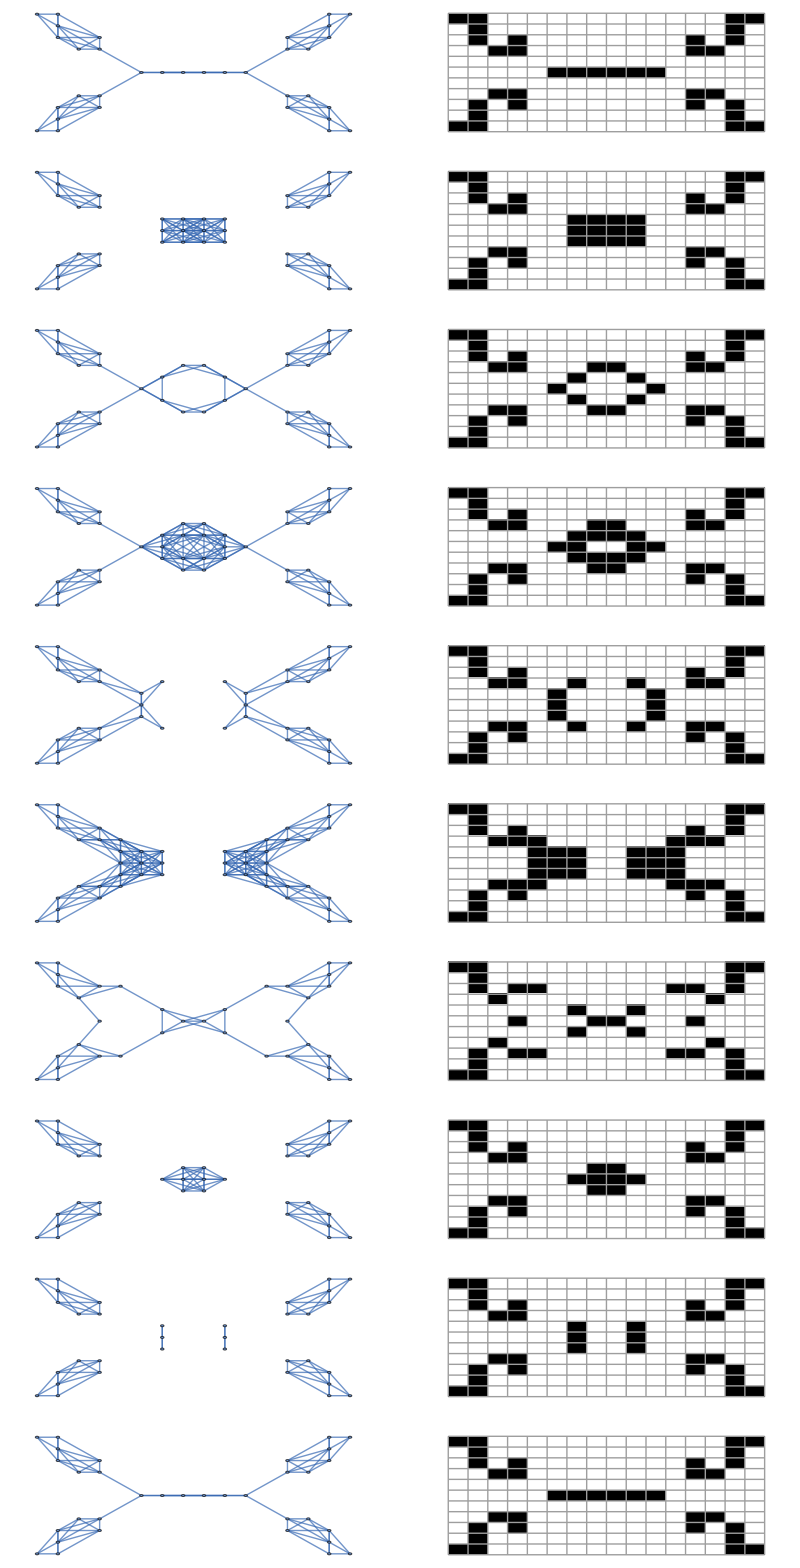
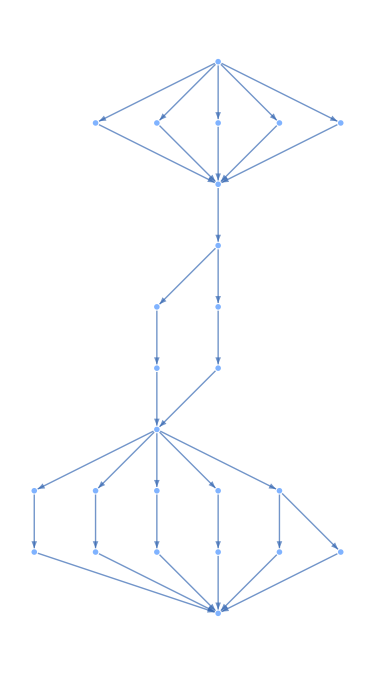

```mathematica
Row[{
GraphicsGrid[
Transpose[{NearestNeighborGraph[Position[Transpose[
Reverse[Normal[#]]],1], {All,2Sqrt[2]}]&/@CellularAutomaton["GameOfLife", {$LifeData["Worker bee"]["MatrixData"], 0}, 9], ArrayPlot[#, Mesh-> True]&/@CellularAutomaton["GameOfLife", {$LifeData["Worker bee"]["MatrixData"], 0}, 9]}]], GraphPlot[PatternsLayeredGraph[$LifeData["Worker bee"]], ImageSize-> {375, Automatic}]
}]
```

The criteria for separation of parts is whether the cells are in each other’s radius

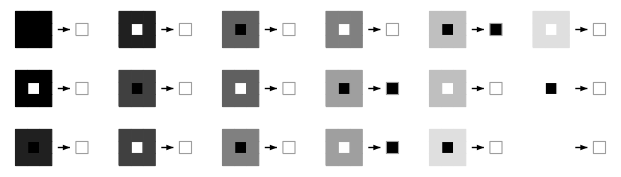

```mathematica
RulePlot[CellularAutomaton["GameOfLife"]]
```

```mathematica
Row[{
GraphicsGrid[
Transpose[{With[{ng = NearestNeighborGraph[Position[Transpose[
Reverse[Normal[#]]],1], {All,2Sqrt[2]}]}, HighlightGraph[ng, (Subgraph[ng,#]&/@ WeaklyConnectedComponents[ng])]]&/@CellularAutomaton["GameOfLife", {$LifeData["Worker bee"]["MatrixData"], 0}, 9], ArrayPlot[#, Mesh-> True]&/@CellularAutomaton["GameOfLife", {$LifeData["Worker bee"]["MatrixData"], 0}, 9]}]], GraphPlot[PatternsLayeredGraph[$LifeData["Worker bee"]], ImageSize-> {375, Automatic}]
}]
```

-Graphics--Graphics-

#### But how does it know where to draw the edges?

It runs each component. Then it runs the causal separation of the whole thing. It checks if any component is equal to any of the causal separations. If it is that means that there should be an edge from the previous component to the new one. If none, it defaults to just drawing edges from all previous to all next

```mathematica
IterateLife[ons_]:=Module[{cts},
cts=Counts[Catenate[
Outer[Plus,ons,$Neighborhood,1]]];
Union[
Intersection[Keys[Select[cts,#==2&]],ons],
Keys[Select[cts,#==3&]]
]
]
```

```mathematica
ArrayPlot[SparseArray[Thread[InitializeMultiwayLife[$LifeData["Worker bee"]["MatrixData"]]][1]["Data"]-> 1]]
```

-Graphics-

```mathematica
ArrayPlot[SparseArray[Thread[Map[MapAt[IterateLife,#,"Data"]&,InitializeMultiwayLife[$LifeData["Worker bee"]["MatrixData"]]][1]["Data"]->1]]]
```

-Graphics-

```mathematica
keep
```

<|9→<|Data→{{1,1},{1,11},{2,1},{2,2},{2,3},{2,9},{2,10},{2,11},{3,4},{3,8},{4,3},{4,4},{4,8},{4,9},{5,4},{5,5},{5,6},{5,7},{5,8},{6,5},{6,6},{6,7},{7,5},{7,6},{7,7}},InComponents→{8}|>,10→<|Data→{{10,5},{10,6},{10,7},{11,5},{11,6},{11,7},{12,4},{12,5},{12,6},{12,7},{12,8},{13,3},{13,4},{13,8},{13,9},{14,4},{14,8},{15,1},{15,2},{15,3},{15,9},{15,10},{15,11},{16,1},{16,11}},InComponents→{8}|>|>

```mathematica
sep
```

{{{10,5},{10,6},{10,7},{11,5},{11,6},{11,7},{12,4},{12,5},{12,6},{12,7},{12,8},{13,3},{13,4},{13,8},{13,9},{14,4},{14,8},{15,1},{15,2},{15,3},{15,9},{15,10},{15,11},{16,1},{16,11}},{{1,1},{1,11},{2,1},{2,2},{2,3},{2,9},{2,10},{2,11},{3,4},{3,8},{4,3},{4,4},{4,8},{4,9},{5,4},{5,5},{5,6},{5,7},{5,8},{6,5},{6,6},{6,7},{7,5},{7,6},{7,7}}}

```mathematica
IterateMultiwayLife[state_]:=Module[{
max=Max[Keys[state]](*,
frame,sep,keep,new*)
},
(*nextState=state;*)
nextState=Map[MapAt[IterateLife,#,"Data"]&,state];
frame=Apply[Union,#Data&/@Values[nextState]];
sep=CausalSeparation[frame];
keep=Select[nextState,MemberQ[sep,#Data]&];
new=Complement[sep,#Data&/@Values[keep]];
keep2=KeyValueMap[CompoundExpression[max++,
max->ReplacePart[#2,"InComponents"->{#1}]
]&,keep];
new2=Map[Function[pts,
CompoundExpression[max++,
max->Association[
"Data"->pts,
"InComponents"->Keys[Select[nextState,
IntersectingQ[pts,#Data]&]]
]
]],new];
Association[Join[keep2,new2]]
]
```

```mathematica
InitializeMultiwayLife[$LifeData["Worker bee"]["MatrixData"]]
```

<|1→<|Data→{{1,1},{1,11},{2,1},{2,2},{2,3},{2,9},{2,10},{2,11},{3,4},{3,8},{4,3},{4,4},{4,8},{4,9},{6,6},{7,6},{8,6},{9,6},{10,6},{11,6},{13,3},{13,4},{13,8},{13,9},{14,4},{14,8},{15,1},{15,2},{15,3},{15,9},{15,10},{15,11},{16,1},{16,11}},InComponents→{}|>|>

```mathematica
IterateMultiwayLife[InitializeMultiwayLife[$LifeData["Worker bee"]["MatrixData"]]]
```

<|2→<|Data→{{1,1},{2,1},{2,2},{2,3},{3,4},{4,3},{4,4}},InComponents→{1}|>,3→<|Data→{{1,11},{2,9},{2,10},{2,11},{3,8},{4,8},{4,9}},InComponents→{1}|>,4→<|Data→{{13,3},{13,4},{14,4},{15,1},{15,2},{15,3},{16,1}},InComponents→{1}|>,5→<|Data→{{13,8},{13,9},{14,8},{15,9},{15,10},{15,11},{16,11}},InComponents→{1}|>,6→<|Data→{{7,5},{7,6},{7,7},{8,5},{8,6},{8,7},{9,5},{9,6},{9,7},{10,5},{10,6},{10,7}},InComponents→{1}|>|>

```mathematica
IterateMultiwayLife[%]
```

<|11→<|Data→{{1,1},{1,11},{2,1},{2,2},{2,3},{2,9},{2,10},{2,11},{3,4},{3,8},{4,3},{4,4},{4,8},{4,9},{5,4},{5,5},{5,6},{5,7},{5,8},{6,5},{6,6},{6,7},{7,5},{7,6},{7,7}},InComponents→{9}|>,12→<|Data→{{10,5},{10,6},{10,7},{11,5},{11,6},{11,7},{12,4},{12,5},{12,6},{12,7},{12,8},{13,3},{13,4},{13,8},{13,9},{14,4},{14,8},{15,1},{15,2},{15,3},{15,9},{15,10},{15,11},{16,1},{16,11}},InComponents→{10}|>|>

```mathematica
nextState
```

<|1→<|Data→{{1,1},{1,11},{2,1},{2,2},{2,3},{2,9},{2,10},{2,11},{3,4},{3,8},{4,3},{4,4},{4,8},{4,9},{7,5},{7,6},{7,7},{8,5},{8,6},{8,7},{9,5},{9,6},{9,7},{10,5},{10,6},{10,7},{13,3},{13,4},{13,8},{13,9},{14,4},{14,8},{15,1},{15,2},{15,3},{15,9},{15,10},{15,11},{16,1},{16,11}},InComponents→{}|>|>

```mathematica
frame
```

{{1,1},{1,11},{2,1},{2,2},{2,3},{2,9},{2,10},{2,11},{3,4},{3,8},{4,3},{4,4},{4,8},{4,9},{7,5},{7,6},{7,7},{8,5},{8,6},{8,7},{9,5},{9,6},{9,7},{10,5},{10,6},{10,7},{13,3},{13,4},{13,8},{13,9},{14,4},{14,8},{15,1},{15,2},{15,3},{15,9},{15,10},{15,11},{16,1},{16,11}}

```mathematica
new
```

{{{1,1},{2,1},{2,2},{2,3},{3,4},{4,3},{4,4}},{{1,11},{2,9},{2,10},{2,11},{3,8},{4,8},{4,9}},{{13,3},{13,4},{14,4},{15,1},{15,2},{15,3},{16,1}},{{13,8},{13,9},{14,8},{15,9},{15,10},{15,11},{16,11}},{{7,5},{7,6},{7,7},{8,5},{8,6},{8,7},{9,5},{9,6},{9,7},{10,5},{10,6},{10,7}}}

```mathematica
new2
```

{2→<|Data→{{1,1},{2,1},{2,2},{2,3},{3,4},{4,3},{4,4}},InComponents→{1}|>,3→<|Data→{{1,11},{2,9},{2,10},{2,11},{3,8},{4,8},{4,9}},InComponents→{1}|>,4→<|Data→{{13,3},{13,4},{14,4},{15,1},{15,2},{15,3},{16,1}},InComponents→{1}|>,5→<|Data→{{13,8},{13,9},{14,8},{15,9},{15,10},{15,11},{16,11}},InComponents→{1}|>,6→<|Data→{{7,5},{7,6},{7,7},{8,5},{8,6},{8,7},{9,5},{9,6},{9,7},{10,5},{10,6},{10,7}},InComponents→{1}|>}

```mathematica
SimpleClosure[InitializeMultiwayLife[$LifeData["Worker bee"]["MatrixData"]], 9]
```

{<|1→<|Data→{{1,1},{1,11},{2,1},{2,2},{2,3},{2,9},{2,10},{2,11},{3,4},{3,8},{4,3},{4,4},{4,8},{4,9},{6,6},{7,6},{8,6},{9,6},{10,6},{11,6},{13,3},{13,4},{13,8},{13,9},{14,4},{14,8},{15,1},{15,2},{15,3},{15,9},{15,10},{15,11},{16,1},{16,11}},InComponents→{}|>|>,<|2→<|Data→{{1,1},{2,1},{2,2},{2,3},{3,4},{4,3},{4,4}},InComponents→{1}|>,3→<|Data→{{1,11},{2,9},{2,10},{2,11},{3,8},{4,8},{4,9}},InComponents→{1}|>,4→<|Data→{{13,3},{13,4},{14,4},{15,1},{15,2},{15,3},{16,1}},InComponents→{1}|>,5→<|Data→{{13,8},{13,9},{14,8},{15,9},{15,10},{15,11},{16,11}},InComponents→{1}|>,6→<|Data→{{7,5},{7,6},{7,7},{8,5},{8,6},{8,7},{9,5},{9,6},{9,7},{10,5},{10,6},{10,7}},InComponents→{1}|>|>,<|7→<|Data→{{1,1},{1,11},{2,1},{2,2},{2,3},{2,9},{2,10},{2,11},{3,4},{3,8},{4,3},{4,4},{4,8},{4,9},{6,6},{7,5},{7,7},{8,4},{8,8},{9,4},{9,8},{10,5},{10,7},{11,6},{13,3},{13,4},{13,8},{13,9},{14,4},{14,8},{15,1},{15,2},{15,3},{15,9},{15,10},{15,11},{16,1},{16,11}},InComponents→{2,3,4,5,6}|>|>,<|8→<|Data→{{1,1},{1,11},{2,1},{2,2},{2,3},{2,9},{2,10},{2,11},{3,4},{3,8},{4,3},{4,4},{4,8},{4,9},{6,6},{7,5},{7,6},{7,7},{8,4},{8,5},{8,7},{8,8},{9,4},{9,5},{9,7},{9,8},{10,5},{10,6},{10,7},{11,6},{13,3},{13,4},{13,8},{13,9},{14,4},{14,8},{15,1},{15,2},{15,3},{15,9},{15,10},{15,11},{16,1},{16,11}},InComponents→{7}|>|>,<|9→<|Data→{{1,1},{1,11},{2,1},{2,2},{2,3},{2,9},{2,10},{2,11},{3,4},{3,8},{4,3},{4,4},{4,8},{4,9},{6,5},{6,6},{6,7},{7,4},{7,8}},InComponents→{8}|>,10→<|Data→{{10,4},{10,8},{11,5},{11,6},{11,7},{13,3},{13,4},{13,8},{13,9},{14,4},{14,8},{15,1},{15,2},{15,3},{15,9},{15,10},{15,11},{16,1},{16,11}},InComponents→{8}|>|>,<|11→<|Data→{{1,1},{1,11},{2,1},{2,2},{2,3},{2,9},{2,10},{2,11},{3,4},{3,8},{4,3},{4,4},{4,8},{4,9},{5,4},{5,5},{5,6},{5,7},{5,8},{6,5},{6,6},{6,7},{7,5},{7,6},{7,7}},InComponents→{9}|>,12→<|Data→{{10,5},{10,6},{10,7},{11,5},{11,6},{11,7},{12,4},{12,5},{12,6},{12,7},{12,8},{13,3},{13,4},{13,8},{13,9},{14,4},{14,8},{15,1},{15,2},{15,3},{15,9},{15,10},{15,11},{16,1},{16,11}},InComponents→{10}|>|>,<|13→<|Data→{{1,1},{1,11},{2,1},{2,2},{2,3},{2,9},{2,10},{2,11},{3,4},{3,8},{4,3},{4,6},{4,9},{5,3},{5,9},{7,5},{7,7},{8,6},{9,6},{10,5},{10,7},{12,3},{12,9},{13,3},{13,6},{13,9},{14,4},{14,8},{15,1},{15,2},{15,3},{15,9},{15,10},{15,11},{16,1},{16,11}},InComponents→{11,12}|>|>,<|14→<|Data→{{1,1},{2,1},{2,2},{2,3},{3,4},{4,3},{4,4}},InComponents→{13}|>,15→<|Data→{{1,11},{2,9},{2,10},{2,11},{3,8},{4,8},{4,9}},InComponents→{13}|>,16→<|Data→{{13,3},{13,4},{14,4},{15,1},{15,2},{15,3},{16,1}},InComponents→{13}|>,17→<|Data→{{13,8},{13,9},{14,8},{15,9},{15,10},{15,11},{16,11}},InComponents→{13}|>,18→<|Data→{{7,6},{8,5},{8,6},{8,7},{9,5},{9,6},{9,7},{10,6}},InComponents→{13}|>|>,<|19→<|Data→{{1,1},{2,1},{2,2},{2,3},{3,4},{4,3},{4,4}},InComponents→{14}|>,20→<|Data→{{1,11},{2,9},{2,10},{2,11},{3,8},{4,8},{4,9}},InComponents→{15}|>,21→<|Data→{{13,3},{13,4},{14,4},{15,1},{15,2},{15,3},{16,1}},InComponents→{16}|>,22→<|Data→{{13,8},{13,9},{14,8},{15,9},{15,10},{15,11},{16,11}},InComponents→{17}|>,23→<|Data→{{7,5},{7,6},{7,7}},InComponents→{18}|>,24→<|Data→{{10,5},{10,6},{10,7}},InComponents→{18}|>|>,<|25→<|Data→{{1,1},{1,11},{2,1},{2,2},{2,3},{2,9},{2,10},{2,11},{3,4},{3,8},{4,3},{4,4},{4,8},{4,9},{6,6},{7,6},{8,6},{9,6},{10,6},{11,6},{13,3},{13,4},{13,8},{13,9},{14,4},{14,8},{15,1},{15,2},{15,3},{15,9},{15,10},{15,11},{16,1},{16,11}},InComponents→{19,20,21,22,23,24}|>|>}

```mathematica
LifeMultiwayGraph[seq_,
opts:OptionsPattern[Graph]
]:=Module[{(*merge,
strat,edges,vertices*)},
strat=Association[Apply[Union,
MapIndexed[Thread[#1->#2[[1]]
]&,Keys/@seq]]];
merge=Merge[seq,First];
vertices=Sort[Keys[strat]];
vertices=Association[
#->{strat[#],#,merge[#,"Data"]
}&/@vertices];
edges=Catenate[Catenate[
KeyValueMap[Function[{out,dat},
DirectedEdge[
vertices[#],
vertices[out]
]&/@dat["InComponents"]
],#]]&/@seq];
Graph[Values[vertices],edges,opts]
]
```

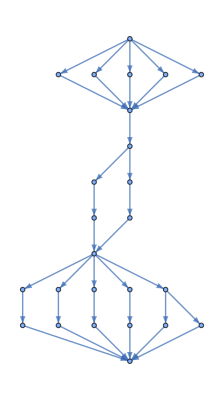

```mathematica
LifeMultiwayGraph[SimpleClosure[InitializeMultiwayLife[$LifeData["Worker bee"]["MatrixData"]], 9]]
```

### Is this pattern engineered?

Yep:

### Graph Analysis as a Quantitative Measure of Modularity

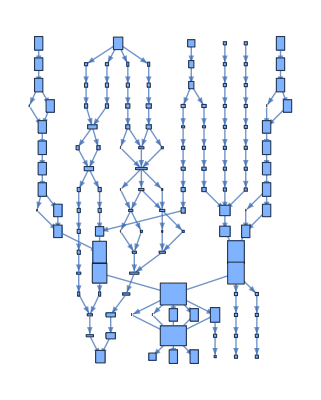

```mathematica
BoundingBoxLayeredGraph[$LifeData["Period-15 glider gun"]]
```

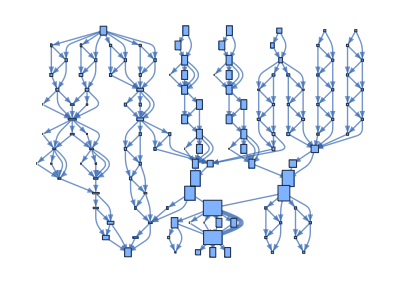

```mathematica
Function[g, Module[{vertices,edges,newEdges, toRemove},vertices=VertexList[g];
toRemove=Select[vertices,(VertexInDegree[g,#]==1&&VertexOutDegree[g,#]==1)&];newEdges=Flatten[Table[With[{in=First[Select[EdgeList[g],Last[#]==v&]],out=First[Select[EdgeList[g],First[#]==v&]]},If[in=!=Missing["NotAvailable"]&&out=!=Missing["NotAvailable"],{First[in]->Last[out]},{}]],{v,toRemove}],1];LayeredGraph[Complement[EdgeList[g],EdgeList[g,toRemove]]~Join~newEdges,
VertexShapeFunction->
Function[{pos, val, blah}, Rectangle[pos -Reverse[#] / 40 ,pos +Reverse[#] / 40]&@ (Subtract@@(Reverse@MinMax[#])&/@Transpose[Ramp[val[[-1]]]])]
]]][BoundingBoxLayeredGraph[$LifeData["Period-15 glider gun"]]]
```

The edge count here is then a measure of the complexity or  interactivity of the pattern

```mathematica
EdgeCount[]
```

238

### Examining modularity of progress

```mathematica
allimps = Table[Module[{p3=SortBy[Select[$LifeData,#Class==="Oscillator"&&#Period==i&]//Quiet,{#Year,-Times@@Dimensions[#MatrixData]}&],improvements},improvements=Union[FoldList[Function[{min,next},If[Times@@Dimensions[next["MatrixData"]]<Times@@Dimensions[min["MatrixData"]],next,min]],Values[p3]]]],{i, 2, 30}];
```

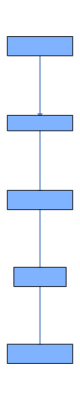
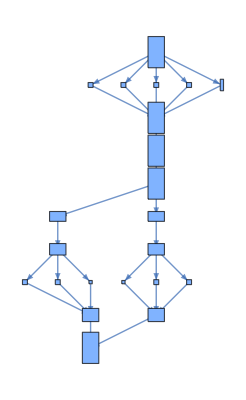
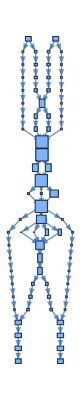
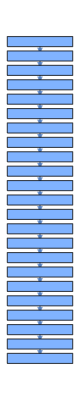
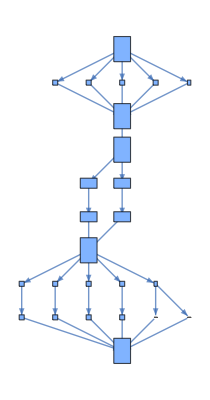
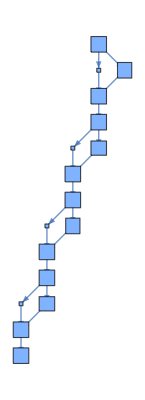
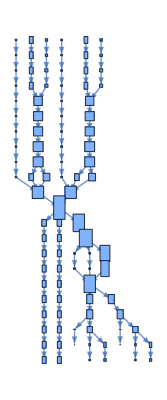
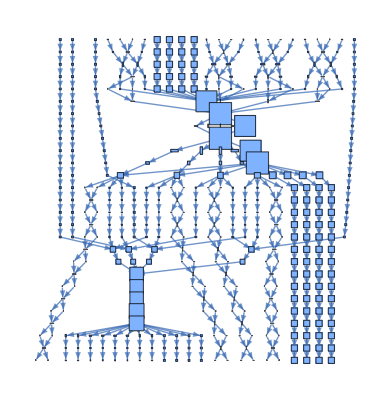
{-Graphics-Mold,-Graphics-Snacker,-Graphics-30P25,-Graphics-Champagne glass,-Graphics-Worker bee,-Graphics-Dinner table,-Graphics-p21 honey farm hassler,-Graphics-p26 pre-pulsar shuttle,-Graphics-Pulsar,-Graphics-Figure eight}

```mathematica
SeedRandom[1111];
Labeled[BoundingBoxLayeredGraph[#], #Name]&/@ RandomSample[Catenate[allimps], 10]
```

Looking at all vertex counts

```mathematica
ags = BoundingBoxLayeredGraph/@ Catenate[allimps];
```

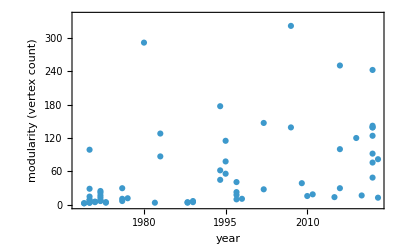

```mathematica
ListPlot[MapThread[{#2[["Year"]],VertexCount[#1]}&, {ags, Catenate[allimps]}], Frame->{True, True,False, False}, FrameLabel->{"year", "modularity (vertex count)"}]
```

With callouts

```mathematica
ListPlot[MapThread[Callout[{#2[["Year"]],VertexCount[#1]}, #2[["Name"]]]&, {ags, Catenate[allimps]}], Frame->{True, True,False, False}, FrameLabel->{"year", "modularity (vertex count)"}]
```

-Graphics-

Now vertex count per frame

```mathematica
ListPlot[MapThread[Callout[{#2[["Year"]],VertexCount[#1]/#2[["Period"]]}, #2[["Name"]]]&, {ags, Catenate[allimps]}], Frame->{True, True,False, False}, FrameLabel->{"year", "modularity (vertex count)"}]
```

-Graphics-

```mathematica
ListPlot[MapThread[Callout[{#2[["Year"]],VertexCount[#1]/(#2[["Period"]] + 1)}, #2[["Name"]]]&, {ags, Catenate[allimps]}], Frame->{True, True,False, False}, FrameLabel->{"year", "modularity (vertex count)"}]
```

-Graphics-

#### Looking for low-modularity patterns found by search

```mathematica
sinidxs = Select[Transpose[{ags, Catenate[allimps]}], VertexCount[#[[1]]] /( #[[2, "Period"]]+1 ) <= 1.1&-> "Index"]
```

{1,2,3,4,5,6,7,8,9,10,11,12,14,15,18,19,20,21,22,23,27,29,31,32,35,39,42,43,52,65}

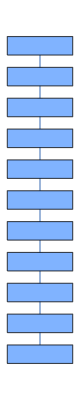
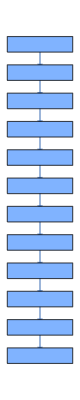
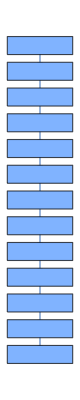
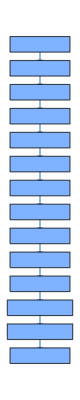
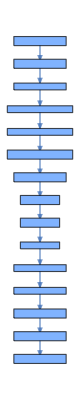
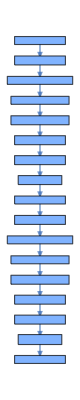
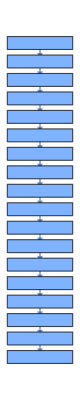
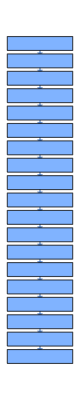
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ags[[Select[Transpose[{ags, Catenate[allimps]}], VertexCount[#[[1]]] / #[[2, "Period"]] <= 1.1&-> "Index"]]]
```

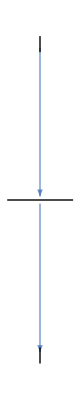
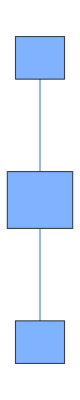
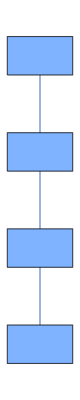
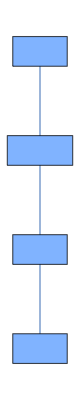
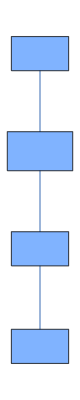
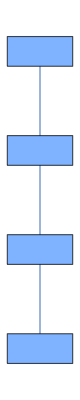
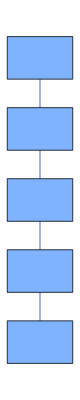
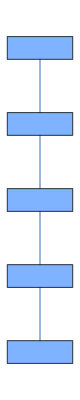
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ags[[Select[Transpose[{ags, Catenate[allimps]}], VertexCount[#[[1]]] /( #[[2, "Period"]]+1 )<= 1&-> "Index"]]]
```

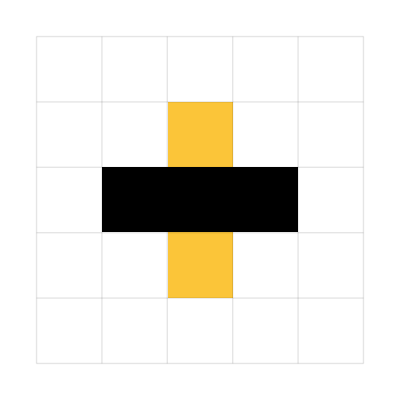
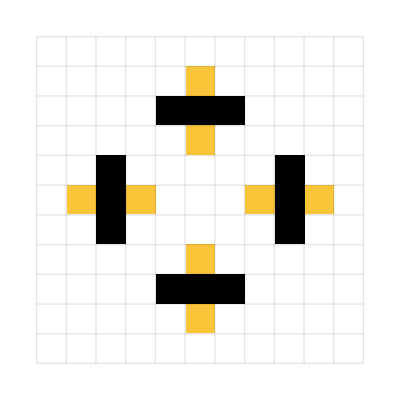
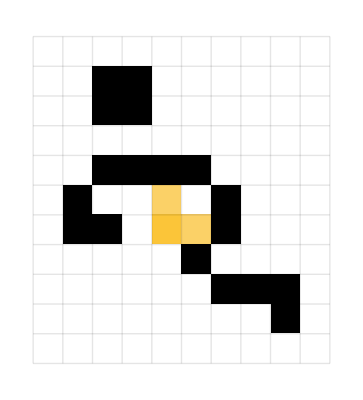
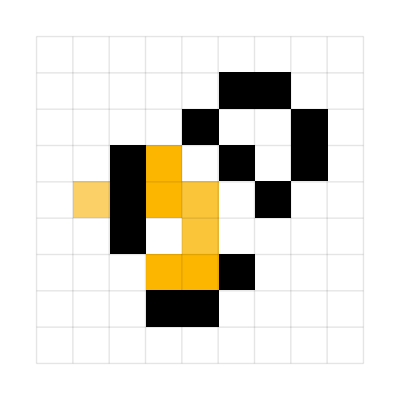
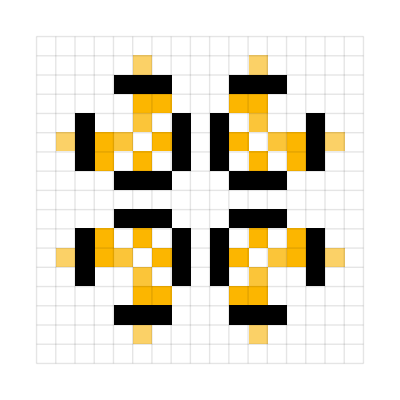
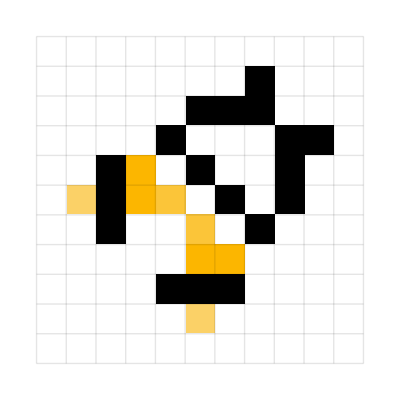
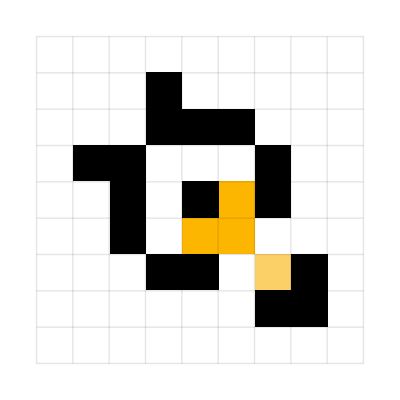
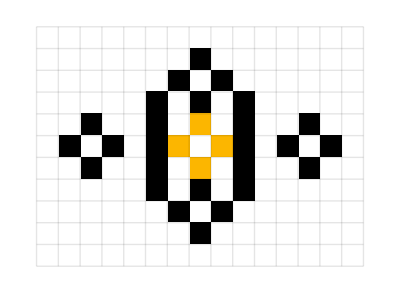
{-Graphics-Blinker,-Graphics-Traffic light,-Graphics-Cuphook,-Graphics-Jam,-Graphics-Pulsar,-Graphics-Pulsar quadrant,-Graphics-Trice tongs,-Graphics-Gray counter,-Graphics-Mazing,-Graphics-Mold,-Graphics-Monogram,-Graphics-Pinwheel,-Graphics-Octagon 2,-Graphics-Extremely impressive,-Graphics-$rats,-Graphics-Airforce,-Graphics-Burloaferimeter,-Graphics-Figure eight,-Graphics-Hertz oscillator,-Graphics-29P9,-Graphics-37P10.1,-Graphics-38P11.1,-Graphics-Mold on fire-spitting,-Graphics-53P13,-Graphics-Tumbler,-Graphics-Rob's p16,-Graphics-54P17.1,-Graphics-Merzenich's p18,-Graphics-Champagne glass,-Graphics-123P27.1}

```mathematica
Labeled[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData, 0}, #Period, ImageSize->Tiny], #Name]&/@ Catenate[allimps][[]]
```

```mathematica
Catenate[allimps][[sinidxs, "Name"]]
```

{Blinker,Traffic light,Cuphook,Jam,Pulsar,Pulsar quadrant,Trice tongs,Gray counter,Mazing,Mold,Monogram,Pinwheel,Octagon 2,Extremely impressive,$rats,Airforce,Burloaferimeter,Figure eight,Hertz oscillator,29P9,37P10.1,38P11.1,Mold on fire-spitting,53P13,Tumbler,Rob's p16,54P17.1,Merzenich's p18,Champagne glass,123P27.1}

#### Looking at the LifeWiki Descriptions and determining if discovered or invented

```mathematica
tab = List/@(#Name&/@Catenate[allimps][[]])
```

{{Blinker},{Traffic light},{Cuphook},{Jam},{Pulsar},{Pulsar quadrant},{Trice tongs},{Gray counter},{Mazing},{Mold},{Monogram},{Pinwheel},{Octagon 2},{Extremely impressive},{$rats},{Airforce},{Burloaferimeter},{Figure eight},{Hertz oscillator},{29P9},{37P10.1},{38P11.1},{Mold on fire-spitting},{53P13},{Tumbler},{Rob's p16},{54P17.1},{Merzenich's p18},{Champagne glass},{123P27.1}}

```mathematica
List
```

```mathematica
TableView[Dynamic[tab]]
```

$CellContext`tab

```mathematica
tab[[1, 2]] // Head
```

String

```mathematica
goodData = ;
```

```mathematica
goodData[[1]]
```

<|Pattern type→Spaceship,cells→{},Year of discovery→1989,Discovered by→Dean Hickerson,Period→4,Heat→125.5,Speed→c/4,Wiki→https://conwaylife.com/wiki/119P4H1V0,Name→119P4H1V0|>

```mathematica
scrapeData[[1]]
```

{{Pattern type,Stable reflector},{cells,Number of,98},{Angle,0°},{Colour,Colour-preserving},{Discovered by,Mitchell Riley},{Year of discovery,2023},{Outer-totalistic, rules},{Isotropic, rules},{Rules,Outer-totalistic, rules,# of rules,Isotropic},{Plaintext,zerodegreereflector202303.cells},{RLE,zerodegreereflector202303.rle},{Pattern files,Plaintext,zerodegreereflector202303.cells,RLE,zerodegreereflector202303.rle},{apgcode,xs98_y54a9r2p6o8ge2zy923y5o8gzxggy5ccy5qb8ehjzw3ialka4y133y619f023z66078a6zy2c453},{Identifiers,apgcode,xs98_y54a9r2p6o8ge2zy923y5o8gzxggy5ccy5qb8ehjzw3ialka4y133y619f023z66078a6zy2c453}}

#### Automating the process of getting descriptions from lifewiki

```mathematica
getinfo[name_]:= Module[{xml =Import[$LifeData["123P27.1"]["Wiki"], "XML"] },
StringReplace[StringRiffle[(FirstCase[xml, XMLElement["p", {___}, {___}],{},  Infinity]//.XMLElement[_, {___}, {s_String}]:> s)[[3]]], " . "-> ". "]
]
```

```mathematica
o = Import[$LifeData["123P27.1"]["Wiki"], "XML"];
```

```mathematica
StringReplace[StringRiffle[(FirstCase[o, XMLElement["p", {___}, {___}],{},  Infinity]//.XMLElement[_, {___}, {s_String}]:> s)[[3]]], " . "-> ". "]
```

123P27.1 is an unnamed period-27 oscillator. It was the first period 27 oscillator to be found, [1] and was discovered by Noam Elkies on November 12, 2002. [2] It is formed by a period-7 oscillator being phase shifted by a period-9 oscillator via a billiard table interaction.

```mathematica
FirstCase[o, XMLElement["p", {___}, {___}],{},Infinity]
```

{}

```mathematica
FirstCase[o, XMLElement["p", {___}, {___}], Infinity]/. XMLElement[_, {___}, {s_String}|s_String]:> s
```

∞

```mathematica
Cases[o, XMLElement["a",{___},
_]]
```

{}

```mathematica
Cases[o,
XMLElement["a",{___,"href"->x__,___},
_]:>x,Infinity]
```

{https://conwaylife.com,https://conwaylife.com/wiki/,https://conwaylife.com/book/,https://catagolue.hatsya.com/,https://conwaylife.com/forums/,https://discord.gg/BCuYCEn,http://golly.sourceforge.net/,#mw-head,#searchInput,/wiki/File:123p27.1.png,/w/images/7/75/123p27.1.gif,/w/images/5/5d/123p27.1.png,/wiki/Oscillator,/wiki/Category:Billiard_tables,/wiki/Cell,/wiki/Category:Patterns_with_between_120_and_129_cells,/wiki/Bounding_box,/wiki/Period#Oscillators,/wiki/Category:Oscillators_with_period_27,/wiki/Mod,/wiki/Category:Oscillators_with_mod_27,/wiki/Heat,/wiki/Category:Oscillators_with_heat_14,/wiki/Volatility,/wiki/Category:Oscillators_with_volatility_0.32,/wiki/Category:Oscillators_with_strict_volatility_0.05,/wiki/Kinetic_symmetry,/wiki/Category:Oscillators_with_n_symmetry,/wiki/Noam_Elkies,/wiki/Category:Patterns_found_in_2002,/wiki/Life-like_cellular_automaton,/wiki/Outer-totalistic,/wiki/Isotropic_non-totalistic,/wiki/Plaintext,https://www.conwaylife.com/patterns/123p27.1.cells,/wiki/RLE,https://www.conwaylife.com/patterns/123p27.1.rle,/wiki/Apgcode,https://catagolue.hatsya.com/object/xp27_06ic88c170v18k4ozkf0v5p1p5t445p6o3tgz11w1169m96p5klkwaabgzy712102egm95d/b3s23,/wiki/Pentadecathlon_ID,https://web.archive.org/web/30000101000000/http://pentadecathlon.com/objects/object-info.php?objid=123P27.1,/wiki/Category:Oscillators_with_period_27,/wiki/Oscillator,#cite_note-1,/wiki/Noam_Elkies,/wiki/Category:Patterns_found_in_2002,#cite_note-2,/wiki/Category:Oscillators_with_period_7,/wiki/Category:Oscillators_with_period_9,/wiki/LifeViewer,/wiki/Catagolue,https://catagolue.hatsya.com/object/xp27_mkid1e80g8gz1qaaw5l5kjcidicggzx1no3cjk44nkjgjkv0fpzy23452gv0sg622611/b3s23/,/wiki/56P27,/wiki/94P27.1,#cite_ref-1,/wiki/Jason_Summers,http://entropymine.com/jason/life/,#cite_ref-2,http://entropymine.com/jason/life/status.html,https://catagolue.hatsya.com/object/xp27_06ic88c170v18k4ozkf0v5p1p5t445p6o3tgz11w1169m96p5klkwaabgzy712102egm95d/b3s23,/wiki/Adam_P._Goucher,/wiki/Catagolue,https://web.archive.org/web/30000101000000/http://pentadecathlon.com/objects/object-info.php?objid=123P27.1,/wiki/Heinrich_Koenig,https://conwaylife.com/w/index.php?title=123P27.1&oldid=152273,/wiki/Special:Categories,/wiki/Category:Patterns,/wiki/Category:Oscillators_with_between_120_and_129_cells,/wiki/Category:Periodic_objects_with_minimum_population_between_120_and_129,/wiki/Category:Patterns_with_between_120_and_129_cells,/wiki/Category:Patterns_found_by_Noam_Elkies,/wiki/Category:Patterns_found_in_2002,/wiki/Category:Oscillators,/wiki/Category:Billiard_tables,/wiki/Category:Oscillators_with_period_27,/wiki/Category:Oscillators_with_mod_27,/wiki/Category:Oscillators_with_heat_14,/wiki/Category:Oscillators_with_volatility_0.32,/wiki/Category:Oscillators_with_strict_volatility_0.05,/wiki/Category:Oscillators_with_n_symmetry,/wiki/Category:Unnamed_periodic_objects,/wiki/Category:Pages_that_link_to_Jason_Summers%27_pattern_collections,/wiki/Category:Pages_citing_websites,/wiki/Category:Pages_needing_cleanup,/wiki/Category:Pages_that_link_to_Adam_P._Goucher%27s_Catagolue,/wiki/Category:Articles_using_EmbedViewer_with_no_pname,/wiki/Category:Pages_that_link_to_Heinrich_Koenig%27s_Game_of_Life_Object_Catalogs,/w/index.php?title=Special:CreateAccount&returnto=123P27.1,/w/index.php?title=Special:UserLogin&returnto=123P27.1,/wiki/123P27.1,/w/index.php?title=Talk:123P27.1&action=edit&redlink=1,/wiki/123P27.1,/w/index.php?title=123P27.1&action=edit,/w/index.php?title=123P27.1&action=history,/wiki/Main_Page,/wiki/Main_Page,/wiki/ConwayLife.com:About,/wiki/LifeWiki:Editor_pages,/wiki/Tutorials,https://conwaylife.com/forums/viewforum.php?f=16,/wiki/Special:RecentChanges,/wiki/Special:Random,/wiki/LifeWiki:Life_links,/wiki/Special:WhatLinksHere/123P27.1,/wiki/Special:RecentChangesLinked/123P27.1,/wiki/Special:SpecialPages,javascript:print();,/w/index.php?title=123P27.1&oldid=152273,/w/index.php?title=123P27.1&action=info,http://www.gnu.org/copyleft/fdl.html,/wiki/LifeWiki:Privacy_policy,/wiki/LifeWiki:About,/wiki/LifeWiki:General_disclaimer,http://www.gnu.org/copyleft/fdl.html,https://www.mediawiki.org/}

```mathematica
Position[o, XMLElement["p",{},{XMLElement["b",{},{"123P27.1"}],"is an unnamed",XMLElement["span",{"style"->"white-space: nowrap"},{XMLElement["a",{"href"->"/wiki/Category:Oscillators_with_period_27","title"->"Category:Oscillators with period 27"},{"period-27"}]}],XMLElement["a",{"href"->"/wiki/Oscillator","title"->"Oscillator"},{"oscillator"}],". It was the first period 27 oscillator to be found,",XMLElement["sup",{"id"->"cite_ref-1","class"->"reference"},{XMLElement["a",{"href"->"#cite_note-1"},{"[1]"}]}],"and was discovered by",XMLElement["a",{"href"->"/wiki/Noam_Elkies","title"->"Noam Elkies"},{"Noam Elkies"}],"on November 12,",XMLElement["a",{"href"->"/wiki/Category:Patterns_found_in_2002","title"->"Category:Patterns found in 2002"},{"2002"}],".",XMLElement["sup",{"id"->"cite_ref-2","class"->"reference"},{XMLElement["a",{"href"->"#cite_note-2"},{"[2]"}]}],"It is formed by a",XMLElement["span",{"style"->"white-space: nowrap"},{XMLElement["a",{"href"->"/wiki/Category:Oscillators_with_period_7","title"->"Category:Oscillators with period 7"},{"period-7"}]}],"oscillator being phase shifted by a",XMLElement["span",{"style"->"white-space: nowrap"},{XMLElement["a",{"href"->"/wiki/Category:Oscillators_with_period_9","title"->"Category:Oscillators with period 9"},{"period-9"}]}],"oscillator via a billiard table interaction."}]]
```

{{2,3,2,3,3,3,5,3,7,3,1,3,2}}

```mathematica
o
```

XMLObject[Document][{XMLObject[Doctype][html]},XMLElement[html,{class→client-nojs,lang→en,dir→ltr},{XMLElement[head,{},{XMLElement[meta,{charset→UTF-8},{}],XMLElement[title,{},{123P27.1 - LifeWiki}],XMLElement[script,{},{document.documentElement.className="client-js";RLCONF={"wgBreakFrames":!1,"wgSeparatorTransformTable":["",""],"wgDigitTransformTable":["",""],"wgDefaultDateFormat":"dmy","wgMonthNames":["","January","February","March","April","May","June","July","August","September","October","November","December"],"wgRequestId":"7b0e3f015ae40391581e2659","wgCSPNonce":!1,"wgCanonicalNamespace":"","wgCanonicalSpecialPageName":!1,"wgNamespaceNumber":0,"wgPageName":"123P27.1","wgTitle":"123P27.1","wgCurRevisionId":152273,"wgRevisionId":152273,"wgArticleId":2459,"wgIsArticle":!0,"wgIsRedirect":!1,"wgAction":"view","wgUserName":null,"wgUserGroups":["*"],"wgCategories":["Pages that link to Jason Summers' pattern collections","Pages citing websites","Pages needing cleanup","Pages that link to Adam P. Goucher's Catagolue","Articles using EmbedViewer with no pname","Pages that link to Heinrich Koenig's Game of Life Object Catalogs","Patterns","Oscillators with between 120 and 129 cells", "Periodic objects with minimum population between 120 and 129","Patterns with between 120 and 129 cells","Patterns found by Noam Elkies","Patterns found in 2002","Oscillators","Billiard tables","Oscillators with period 27","Oscillators with mod 27","Oscillators with heat 14","Oscillators with volatility 0.32","Oscillators with strict volatility 0.05","Oscillators with n symmetry","Unnamed periodic objects"],"wgPageContentLanguage":"en","wgPageContentModel":"wikitext","wgRelevantPageName":"123P27.1","wgRelevantArticleId":2459,"wgIsProbablyEditable":!1,"wgRelevantPageIsProbablyEditable":!1,"wgRestrictionEdit":[],"wgRestrictionMove":[]};RLSTATE={"site.styles":"ready","noscript":"ready","user.styles":"ready","user":"ready","user.options":"loading","ext.cite.styles":"ready","skins.vector.styles.legacy":"ready"};RLPAGEMODULES=["ext.cite.ux-enhancements","site","mediawiki.page.ready","skins.vector.legacy.js"];}],XMLElement[script,{},{(RLQ=window.RLQ||[]).push(function(){mw.loader.implement("user.options@1hzgi",function($,jQuery,require,module){/*@nomin*/mw.user.tokens.set({"patrolToken":"+\\","watchToken":"+\\","csrfToken":"+\\"}); });});}],XMLElement[link,{rel→stylesheet,href→/w/load.php?lang=en&modules=ext.cite.styles%7Cskins.vector.styles.legacy&only=styles&skin=vector},{}],XMLElement[script,{async→,src→/w/load.php?lang=en&modules=startup&only=scripts&raw=1&skin=vector},{}],XMLElement[meta,{name→ResourceLoaderDynamicStyles,content→},{}],XMLElement[link,{rel→stylesheet,href→/w/load.php?lang=en&modules=site.styles&only=styles&skin=vector},{}],XMLElement[meta,{name→generator,content→MediaWiki 1.37.1},{}],XMLElement[meta,{name→format-detection,content→telephone=no},{}],XMLElement[link,{rel→shortcut icon,href→/favicon.ico},{}],XMLElement[link,{rel→search,type→application/opensearchdescription+xml,href→/w/opensearch_desc.php,title→LifeWiki (en)},{}],XMLElement[link,{rel→EditURI,type→application/rsd+xml,href→https://conwaylife.com/w/api.php?action=rsd},{}],XMLElement[link,{rel→license,href→http://www.gnu.org/copyleft/fdl.html},{}],XMLElement[link,{rel→alternate,type→application/atom+xml,title→LifeWiki Atom feed,href→/w/index.php?title=Special:RecentChanges&feed=atom},{}],XMLElement[script,{type→text/javascript,src→https://conwaylife.com/js/lv-plugin.js},{}]}],XMLElement[body,{class→mediawiki ltr sitedir-ltr mw-hide-empty-elt ns-0 ns-subject page-123P27_1 rootpage-123P27_1 skin-vector action-view skin-vector-legacy},{XMLElement[div,{id→mw-page-base,class→noprint},{}],XMLElement[div,{id→mw-head-base,class→noprint},{}],XMLElement[div,{id→content,class→mw-body,role→main},{XMLElement[a,{id→top},{}],XMLElement[div,{id→siteNotice},{XMLElement[div,{id→localNotice,lang→en,dir→ltr},{XMLElement[div,{id→cwl_navbar,class→plainlinks},{XMLElement[a,{rel→nofollow,class→external text,href→https://conwaylife.com},{Home}], • ,XMLElement[b,{},{XMLElement[a,{rel→nofollow,class→external text,href→https://conwaylife.com/wiki/},{LifeWiki}]}], • ,XMLElement[a,{rel→nofollow,class→external text,href→https://conwaylife.com/book/},{Book}], • ,XMLElement[a,{rel→nofollow,class→external text,href→https://catagolue.hatsya.com/},{Catagolue}], • ,XMLElement[a,{rel→nofollow,class→external text,href→https://conwaylife.com/forums/},{Forums}], • ,XMLElement[a,{rel→nofollow,class→external text,href→https://discord.gg/BCuYCEn},{Discord}], • ,XMLElement[a,{rel→nofollow,class→external text,href→http://golly.sourceforge.net/},{Golly}]}]}]}],XMLElement[div,{class→mw-indicators},{}],XMLElement[h1,{id→firstHeading,class→firstHeading},{123P27.1}],XMLElement[div,{id→bodyContent,class→vector-body},{XMLElement[div,{id→siteSub,class→noprint},{From LifeWiki}],XMLElement[div,{id→contentSub},{}],XMLElement[div,{id→contentSub2},{}],XMLElement[div,{id→jump-to-nav},{}],XMLElement[a,{class→mw-jump-link,href→#mw-head},{Jump to navigation}],XMLElement[a,{class→mw-jump-link,href→#searchInput},{Jump to search}],XMLElement[div,{id→mw-content-text,class→mw-body-content mw-content-ltr,lang→en,dir→ltr},{XMLElement[div,{class→mw-parser-output},{XMLElement[table,{class→infobox},{XMLElement[tbody,{},{XMLElement[tr,{},{XMLElement[td,{colspan→2,class→infobox_head},{123P27.1}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,class→infobox_img},{XMLElement[table,{class→img_border,cellpadding→0},{XMLElement[tbody,{},{XMLElement[tr,{},{XMLElement[td,{},{XMLElement[div,{class→rle},{XMLElement[div,{class→codebox},{XMLElement[div,{style→display:none;},{XMLElement[code,{},{#O Noam Elkies, November 12, 2002 #C The first period 27 oscillator to be found. x = 20, y = 22, rule = b3/s23 b2ob2o14b$2bobobob2o10b$bo2bobobo11b$ob2o2bobobo9b$o9b3obo5b$b3o9b2o5b $3bobobo2b2o3b2o3b$5bobobo2b2o3bo2b$4b2obo2b2o2b2obo2b$3bo3bobo2bobobo 3b$4b3o2bo2bo6bo$7b2o3bo2b5o$6bo2b4obo5b$5bob2o3bobo2b3o$6bo2b3o2bo4bo $7b2o5bob2o2b$9b3o2bobo3b$9bo2bobobo3b$10b5ob2o2b$15bo2bob$9bob4o2b2ob $9b2obo! #C [[ THUMBSIZE 2 THEME 6 GRID GRIDMAJOR 0 SUPPRESS THUMBLAUNCH ]] #C [[ AUTOSTART ]] #C [[ GPS 27/2 THUMBSIZE 2 ZOOM 10 ]]}]}]}],XMLElement[canvas,{width→200,height→300,style→margin-left:1px;},{XMLElement[noscript,{},{XMLElement[a,{href→/wiki/File:123p27.1.png,class→image,title→123P27.1 image},{XMLElement[img,{alt→123P27.1 image,src→/w/images/5/5d/123p27.1.png,decoding→async,width→89,height→97},{}]}]}]}]}]}]}]}]}]}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,class→infobox_animlink},{XMLElement[a,{href→/w/images/7/75/123p27.1.gif,class→internal,title→123p27.1.gif},{View animated image}]}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,class→infobox_animlink},{XMLElement[a,{href→/w/images/5/5d/123p27.1.png,class→internal,title→123p27.1.png},{View static image}]}]}],XMLElement[tr,{},{XMLElement[th,{valign→top},{Pattern type}],XMLElement[td,{},{XMLElement[a,{href→/wiki/Oscillator,title→Oscillator},{Oscillator}]}]}],XMLElement[tr,{},{XMLElement[th,{},{Oscillator type}],XMLElement[td,{},{XMLElement[a,{href→/wiki/Category:Billiard_tables,title→Category:Billiard tables},{Billiard table}]}]}],XMLElement[tr,{},{XMLElement[th,{},{Number of,XMLElement[a,{href→/wiki/Cell,title→Cell},{cells}]}],XMLElement[td,{},{XMLElement[span,{style→white-space: nowrap},{XMLElement[a,{href→/wiki/Category:Patterns_with_between_120_and_129_cells,title→Category:Patterns with between 120 and 129 cells},{123}]}]}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/Bounding_box,title→Bounding box},{Bounding box}]}],XMLElement[td,{},{XMLElement[span,{style→white-space: nowrap},{20 × 22}]}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→height:3px;},{}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→background-color:#A7A8C1;height:2px;},{}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→height:3px;},{}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/Period#Oscillators,title→Period},{Period}]}],XMLElement[td,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_period_27,title→Category:Oscillators with period 27},{27}],(,XMLElement[a,{href→/wiki/Mod,title→Mod},{mod}],:,XMLElement[a,{href→/wiki/Category:Oscillators_with_mod_27,title→Category:Oscillators with mod 27},{27}],)}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/Heat,title→Heat},{Heat}]}],XMLElement[td,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_heat_14,title→Category:Oscillators with heat 14},{14.4}]}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/Volatility,title→Volatility},{Volatility}]}],XMLElement[td,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_volatility_0.32,title→Category:Oscillators with volatility 0.32},{0.32}],|,XMLElement[a,{href→/wiki/Category:Oscillators_with_strict_volatility_0.05,title→Category:Oscillators with strict volatility 0.05},{0.05}]}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/Kinetic_symmetry,title→Kinetic symmetry},{Kinetic symmetry}]}],XMLElement[td,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_n_symmetry,title→Category:Oscillators with n symmetry},{n}]}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→height:3px;},{}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→background-color:#A7A8C1;height:2px;},{}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→height:3px;},{}]}],XMLElement[tr,{},{XMLElement[th,{valign→top},{Discovered by}],XMLElement[td,{},{XMLElement[span,{style→white-space: nowrap},{XMLElement[a,{href→/wiki/Noam_Elkies,title→Noam Elkies},{Noam Elkies}]}]}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[span,{style→white-space: nowrap},{Year of discovery}]}],XMLElement[td,{},{XMLElement[a,{href→/wiki/Category:Patterns_found_in_2002,title→Category:Patterns found in 2002},{2002}]}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→height:3px;},{}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→background-color:#A7A8C1;height:2px;},{}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2},{XMLElement[table,{class→infobox_table collapsible collapsed,style→width:100%},{XMLElement[tbody,{},{XMLElement[tr,{},{XMLElement[th,{colspan→2,class→infobox_subhead},{XMLElement[a,{href→/wiki/Life-like_cellular_automaton,title→Life-like cellular automaton},{Rules}]}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/Outer-totalistic,class→mw-redirect,title→Outer-totalistic},{Outer-totalistic}], rules}],XMLElement[td,{style→text-align:right;},{B3/S23 – B38/S2378}]}],XMLElement[tr,{},{XMLElement[th,{},{# of rules}],XMLElement[td,{style→text-align:right;},{2,XMLElement[sup,{},{3}],= 8}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/Isotropic_non-totalistic,class→mw-redirect,title→Isotropic non-totalistic},{Isotropic}], rules}],XMLElement[td,{style→text-align:right;},{B3/S2-n3-a – B36cn7c8/S234aeqrw5-r678}]}]}]}]}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→height:3px;},{}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→background-color:#A7A8C1;height:2px;},{}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2},{XMLElement[table,{class→infobox_table collapsible collapsed,style→width:100%},{XMLElement[tbody,{},{XMLElement[tr,{},{XMLElement[th,{colspan→2,class→infobox_subhead},{Pattern files}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/Plaintext,title→Plaintext},{Plaintext}]}],XMLElement[td,{style→text-align:right;},{XMLElement[a,{rel→nofollow,class→external text,href→https://www.conwaylife.com/patterns/123p27.1.cells},{123p27.1.cells}]}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/RLE,class→mw-redirect,title→RLE},{RLE}]}],XMLElement[td,{style→text-align:right;},{XMLElement[a,{rel→nofollow,class→external text,href→https://www.conwaylife.com/patterns/123p27.1.rle},{123p27.1.rle}]}]}]}]}]}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→height:3px;},{}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→background-color:#A7A8C1;height:2px;},{}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2},{XMLElement[table,{class→infobox_table collapsible collapsed,style→width:100%},{XMLElement[tbody,{},{XMLElement[tr,{},{XMLElement[th,{colspan→2,class→infobox_subhead},{Identifiers}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/Apgcode,title→Apgcode},{apgcode}]}],XMLElement[td,{style→text-align:right; word-break: break-all; padding-left: 1.5em,valign→middle},{XMLElement[a,{rel→nofollow,class→external text,href→https://catagolue.hatsya.com/object/xp27_06ic88c170v18k4ozkf0v5p1p5t445p6o3tgz11w1169m96p5klkwaabgzy712102egm95d/b3s23},{xp27_06ic88c170v18k4ozkf0v5p1p5t445p6o3tgz11w1169m96p5klkwaabgzy712102egm95d}]}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/Pentadecathlon_ID,class→mw-redirect,title→Pentadecathlon ID},{Pentadecathlon ID}]}],XMLElement[td,{style→text-align:right;,valign→middle},{XMLElement[a,{rel→nofollow,class→external text,href→https://web.archive.org/web/30000101000000/http://pentadecathlon.com/objects/object-info.php?objid=123P27.1},{123P27.1}]}]}]}]}]}]}]}]}],XMLElement[p,{},{XMLElement[b,{},{123P27.1}],is an unnamed,XMLElement[span,{style→white-space: nowrap},{XMLElement[a,{href→/wiki/Category:Oscillators_with_period_27,title→Category:Oscillators with period 27},{period-27}]}],XMLElement[a,{href→/wiki/Oscillator,title→Oscillator},{oscillator}],. It was the first period 27 oscillator to be found,,XMLElement[sup,{id→cite_ref-1,class→reference},{XMLElement[a,{href→#cite_note-1},{[1]}]}],and was discovered by,XMLElement[a,{href→/wiki/Noam_Elkies,title→Noam Elkies},{Noam Elkies}],on November 12,,XMLElement[a,{href→/wiki/Category:Patterns_found_in_2002,title→Category:Patterns found in 2002},{2002}],.,XMLElement[sup,{id→cite_ref-2,class→reference},{XMLElement[a,{href→#cite_note-2},{[2]}]}],It is formed by a,XMLElement[span,{style→white-space: nowrap},{XMLElement[a,{href→/wiki/Category:Oscillators_with_period_7,title→Category:Oscillators with period 7},{period-7}]}],oscillator being phase shifted by a,XMLElement[span,{style→white-space: nowrap},{XMLElement[a,{href→/wiki/Category:Oscillators_with_period_9,title→Category:Oscillators with period 9},{period-9}]}],oscillator via a billiard table interaction.}],XMLElement[table,{class→toccolours,style→margin-left: auto; margin-right: auto; width: fit-content; width:300px;},{XMLElement[tbody,{},{XMLElement[tr,{},{XMLElement[td,{align→center},{XMLElement[div,{class→rle},{XMLElement[div,{class→codebox},{XMLElement[div,{style→display:none;},{XMLElement[code,{},{x = 20, y = 22, rule = B3/S23 b2ob2o$2bobobob2o$bo2bobobo$ob2o2bobobo$o9b3obo$b3o9b2o$3bobobo2b2o3b2o$5bobobo2b2o3bo$4b2obo2b2o2b2obo$3bo3bobo2bobobo$4b3o2bo2bo6bo$7b2o3bo2b5o$6bo2b4obo$5bob2o3bobo2b3o$6bo2b3o2bo4bo$7b2o5bob2o$9b3o2bobo$9bo2bobobo$10b5ob2o$15bo$10b4obo$10bo2b2o! #C [[ THUMBSIZE 2 THEME 6 GRID GRIDMAJOR 0 SUPPRESS THUMBLAUNCH ]] #C [[ HEIGHT 560 THUMBSIZE 2 ZOOM 16 GPS 27/2 AUTOSTART LOOP 27 ]]}]}]}],XMLElement[canvas,{width→200,height→300,style→margin-left:1px;},{XMLElement[noscript,{},{XMLElement[div,{style→border-width:1px;border-color:#888888;border-style:solid;padding:8px;},{Please enable Javascript to view this LifeViewer.}]}]}]}]}]}],XMLElement[tr,{},{XMLElement[td,{align→center},{A stator reduction to 120 cells.,XMLElement[br,{},{}],XMLElement[small,{},{(click above to open ,XMLElement[a,{href→/wiki/LifeViewer,title→LifeViewer},{LifeViewer}],)}],XMLElement[br,{},{}],XMLElement[b,{},{XMLElement[a,{href→/wiki/Catagolue,title→Catagolue},{Catagolue}]}],: ,XMLElement[a,{rel→nofollow,class→external text,href→https://catagolue.hatsya.com/object/xp27_mkid1e80g8gz1qaaw5l5kjcidicggzx1no3cjk44nkjgjkv0fpzy23452gv0sg622611/b3s23/},{here}]}]}]}]}],XMLElement[h2,{},{XMLElement[span,{class→mw-headline,id→See_also},{See also}]}],XMLElement[ul,{},{XMLElement[li,{},{XMLElement[a,{href→/wiki/56P27,title→56P27},{56P27}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/94P27.1,title→94P27.1},{94P27.1}]}]}],XMLElement[h2,{},{XMLElement[span,{class→mw-headline,id→References},{References}]}],XMLElement[div,{class→mw-references-wrap},{XMLElement[ol,{class→references},{XMLElement[li,{id→cite_note-1},{XMLElement[span,{class→mw-cite-backlink},{XMLElement[a,{href→#cite_ref-1},{↑}]}],XMLElement[span,{class→reference-text},{XMLElement[a,{href→/wiki/Jason_Summers,title→Jason Summers},{Jason Summers}],',XMLElement[a,{rel→nofollow,class→external text,href→http://entropymine.com/jason/life/},{jslife pattern collection}],. Retrieved on April 9, 2009.}]}],XMLElement[li,{id→cite_note-2},{XMLElement[span,{class→mw-cite-backlink},{XMLElement[a,{href→#cite_ref-2},{↑}]}],XMLElement[span,{class→reference-text},{",XMLElement[a,{rel→nofollow,class→external text,href→http://entropymine.com/jason/life/status.html},{Game of Life Status page}],". Retrieved on April 9, 2009.}]}]}]}],XMLElement[h2,{},{XMLElement[span,{class→mw-headline,id→External_links},{External links}]}],XMLElement[ul,{},{XMLElement[li,{},{XMLElement[a,{rel→nofollow,class→external text,href→https://catagolue.hatsya.com/object/xp27_06ic88c170v18k4ozkf0v5p1p5t445p6o3tgz11w1169m96p5klkwaabgzy712102egm95d/b3s23},{123P27.1}],at,XMLElement[a,{href→/wiki/Adam_P._Goucher,title→Adam P. Goucher},{Adam P. Goucher}],'s,XMLElement[a,{href→/wiki/Catagolue,title→Catagolue},{Catagolue}]}]}],XMLElement[ul,{},{XMLElement[li,{},{XMLElement[a,{rel→nofollow,class→external text,href→https://web.archive.org/web/30000101000000/http://pentadecathlon.com/objects/object-info.php?objid=123P27.1},{123P27.1}],at,XMLElement[a,{href→/wiki/Heinrich_Koenig,title→Heinrich Koenig},{Heinrich Koenig}],'s Game of Life Object Catalogs}]}]}],XMLElement[div,{class→printfooter},{Retrieved from ",XMLElement[a,{dir→ltr,href→https://conwaylife.com/w/index.php?title=123P27.1&oldid=152273},{https://conwaylife.com/w/index.php?title=123P27.1&oldid=152273}],"}]}],XMLElement[div,{id→catlinks,class→catlinks,data-mw→interface},{XMLElement[div,{id→mw-normal-catlinks,class→mw-normal-catlinks},{XMLElement[a,{href→/wiki/Special:Categories,title→Special:Categories},{Categories}],:,XMLElement[ul,{},{XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Patterns,title→Category:Patterns},{Patterns}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_between_120_and_129_cells,title→Category:Oscillators with between 120 and 129 cells},{Oscillators with between 120 and 129 cells}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Periodic_objects_with_minimum_population_between_120_and_129,title→Category:Periodic objects with minimum population between 120 and 129},{Periodic objects with minimum population between 120 and 129}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Patterns_with_between_120_and_129_cells,title→Category:Patterns with between 120 and 129 cells},{Patterns with between 120 and 129 cells}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Patterns_found_by_Noam_Elkies,title→Category:Patterns found by Noam Elkies},{Patterns found by Noam Elkies}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Patterns_found_in_2002,title→Category:Patterns found in 2002},{Patterns found in 2002}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Oscillators,title→Category:Oscillators},{Oscillators}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Billiard_tables,title→Category:Billiard tables},{Billiard tables}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_period_27,title→Category:Oscillators with period 27},{Oscillators with period 27}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_mod_27,title→Category:Oscillators with mod 27},{Oscillators with mod 27}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_heat_14,title→Category:Oscillators with heat 14},{Oscillators with heat 14}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_volatility_0.32,title→Category:Oscillators with volatility 0.32},{Oscillators with volatility 0.32}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_strict_volatility_0.05,title→Category:Oscillators with strict volatility 0.05},{Oscillators with strict volatility 0.05}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_n_symmetry,title→Category:Oscillators with n symmetry},{Oscillators with n symmetry}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Unnamed_periodic_objects,title→Category:Unnamed periodic objects},{Unnamed periodic objects}]}]}]}],XMLElement[div,{id→mw-hidden-catlinks,class→mw-hidden-catlinks mw-hidden-cats-hidden},{Hidden categories:,XMLElement[ul,{},{XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Pages_that_link_to_Jason_Summers%27_pattern_collections,title→Category:Pages that link to Jason Summers' pattern collections},{Pages that link to Jason Summers' pattern collections}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Pages_citing_websites,title→Category:Pages citing websites},{Pages citing websites}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Pages_needing_cleanup,title→Category:Pages needing cleanup},{Pages needing cleanup}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Pages_that_link_to_Adam_P._Goucher%27s_Catagolue,title→Category:Pages that link to Adam P. Goucher's Catagolue},{Pages that link to Adam P. Goucher's Catagolue}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Articles_using_EmbedViewer_with_no_pname,title→Category:Articles using EmbedViewer with no pname},{Articles using EmbedViewer with no pname}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Pages_that_link_to_Heinrich_Koenig%27s_Game_of_Life_Object_Catalogs,title→Category:Pages that link to Heinrich Koenig's Game of Life Object Catalogs},{Pages that link to Heinrich Koenig's Game of Life Object Catalogs}]}]}]}]}]}]}],XMLElement[div,{id→mw-navigation},{XMLElement[h2,{},{Navigation menu}],XMLElement[div,{id→mw-head},{XMLElement[nav,{id→p-personal,class→mw-portlet mw-portlet-personal vector-user-menu-legacy vector-menu,aria-labelledby→p-personal-label,role→navigation},{XMLElement[h3,{id→p-personal-label,class→vector-menu-heading},{XMLElement[span,{},{Personal tools}]}],XMLElement[div,{class→vector-menu-content},{XMLElement[ul,{class→vector-menu-content-list},{XMLElement[li,{id→pt-createaccount,class→mw-list-item},{XMLElement[a,{href→/w/index.php?title=Special:CreateAccount&returnto=123P27.1,title→You are encouraged to create an account and log in; however, it is not mandatory},{Create account}]}],XMLElement[li,{id→pt-login,class→mw-list-item},{XMLElement[a,{href→/w/index.php?title=Special:UserLogin&returnto=123P27.1,title→You are encouraged to log in; however, it is not mandatory [o],accesskey→o},{Log in}]}]}]}]}],XMLElement[div,{id→left-navigation},{XMLElement[nav,{id→p-namespaces,class→mw-portlet mw-portlet-namespaces vector-menu vector-menu-tabs,aria-labelledby→p-namespaces-label,role→navigation},{XMLElement[h3,{id→p-namespaces-label,class→vector-menu-heading},{XMLElement[span,{},{Namespaces}]}],XMLElement[div,{class→vector-menu-content},{XMLElement[ul,{class→vector-menu-content-list},{XMLElement[li,{id→ca-nstab-main,class→selected mw-list-item},{XMLElement[a,{href→/wiki/123P27.1,title→View the content page [c],accesskey→c},{Page}]}],XMLElement[li,{id→ca-talk,class→new mw-list-item},{XMLElement[a,{href→/w/index.php?title=Talk:123P27.1&action=edit&redlink=1,rel→discussion,title→Discussion about the content page (page does not exist) [t],accesskey→t},{Discussion}]}]}]}]}],XMLElement[nav,{id→p-variants,class→mw-portlet mw-portlet-variants emptyPortlet vector-menu-dropdown-noicon vector-menu vector-menu-dropdown,aria-labelledby→p-variants-label,role→navigation},{XMLElement[input,{type→checkbox,id→p-variants-checkbox,role→button,aria-haspopup→true,data-event-name→ui.dropdown-p-variants,class→vector-menu-checkbox,aria-labelledby→p-variants-label},{}],XMLElement[h3,{id→p-variants-label,class→vector-menu-heading},{XMLElement[span,{},{Variants}],XMLElement[span,{class→vector-menu-checkbox-expanded},{expanded}],XMLElement[span,{class→vector-menu-checkbox-collapsed},{collapsed}]}],XMLElement[div,{class→vector-menu-content},{XMLElement[ul,{class→vector-menu-content-list},{}]}]}]}],XMLElement[div,{id→right-navigation},{XMLElement[nav,{id→p-views,class→mw-portlet mw-portlet-views vector-menu vector-menu-tabs,aria-labelledby→p-views-label,role→navigation},{XMLElement[h3,{id→p-views-label,class→vector-menu-heading},{XMLElement[span,{},{Views}]}],XMLElement[div,{class→vector-menu-content},{XMLElement[ul,{class→vector-menu-content-list},{XMLElement[li,{id→ca-view,class→selected mw-list-item},{XMLElement[a,{href→/wiki/123P27.1},{Read}]}],XMLElement[li,{id→ca-viewsource,class→mw-list-item},{XMLElement[a,{href→/w/index.php?title=123P27.1&action=edit,title→This page is protected. You can view its source [e],accesskey→e},{View source}]}],XMLElement[li,{id→ca-history,class→mw-list-item},{XMLElement[a,{href→/w/index.php?title=123P27.1&action=history,title→Past revisions of this page [h],accesskey→h},{View history}]}]}]}]}],XMLElement[nav,{id→p-cactions,class→mw-portlet mw-portlet-cactions emptyPortlet vector-menu-dropdown-noicon vector-menu vector-menu-dropdown,aria-labelledby→p-cactions-label,role→navigation,title→More options},{XMLElement[input,{type→checkbox,id→p-cactions-checkbox,role→button,aria-haspopup→true,data-event-name→ui.dropdown-p-cactions,class→vector-menu-checkbox,aria-labelledby→p-cactions-label},{}],XMLElement[h3,{id→p-cactions-label,class→vector-menu-heading},{XMLElement[span,{},{More}],XMLElement[span,{class→vector-menu-checkbox-expanded},{expanded}],XMLElement[span,{class→vector-menu-checkbox-collapsed},{collapsed}]}],XMLElement[div,{class→vector-menu-content},{XMLElement[ul,{class→vector-menu-content-list},{}]}]}],XMLElement[div,{id→p-search,role→search,class→vector-search-box},{XMLElement[div,{},{XMLElement[h3,{},{XMLElement[label,{for→searchInput},{Search}]}],XMLElement[form,{action→/w/index.php,id→searchform},{XMLElement[div,{id→simpleSearch,data-search-loc→header-navigation},{XMLElement[input,{type→search,name→search,placeholder→Search LifeWiki,autocapitalize→sentences,title→Search LifeWiki [f],accesskey→f,id→searchInput},{}],XMLElement[input,{type→hidden,name→title,value→Special:Search},{}],XMLElement[input,{type→submit,name→fulltext,value→Search,title→Search the pages for this text,id→mw-searchButton,class→searchButton mw-fallbackSearchButton},{}],XMLElement[input,{type→submit,name→go,value→Go,title→Go to a page with this exact name if it exists,id→searchButton,class→searchButton},{}]}]}]}]}]}]}],XMLElement[div,{id→mw-panel},{XMLElement[div,{id→p-logo,role→banner},{XMLElement[a,{class→mw-wiki-logo,href→/wiki/Main_Page,title→Visit the main page},{}]}],XMLElement[nav,{id→p-navigation,class→mw-portlet mw-portlet-navigation vector-menu vector-menu-portal portal,aria-labelledby→p-navigation-label,role→navigation},{XMLElement[h3,{id→p-navigation-label,class→vector-menu-heading},{XMLElement[span,{},{Navigation}]}],XMLElement[div,{class→vector-menu-content},{XMLElement[ul,{class→vector-menu-content-list},{XMLElement[li,{id→n-Wiki-home,class→mw-list-item},{XMLElement[a,{href→/wiki/Main_Page},{Wiki home}]}],XMLElement[li,{id→n-ConwayLife.com,class→mw-list-item},{XMLElement[a,{href→/wiki/ConwayLife.com:About},{ConwayLife.com}]}],XMLElement[li,{id→n-How-to-contribute,class→mw-list-item},{XMLElement[a,{href→/wiki/LifeWiki:Editor_pages},{How to contribute}]}],XMLElement[li,{id→n-Tutorials,class→mw-list-item},{XMLElement[a,{href→/wiki/Tutorials},{Tutorials}]}],XMLElement[li,{id→n-LifeWiki-discussion,class→mw-list-item},{XMLElement[a,{href→https://conwaylife.com/forums/viewforum.php?f=16,rel→nofollow},{LifeWiki discussion}]}],XMLElement[li,{id→n-Recent-changes,class→mw-list-item},{XMLElement[a,{href→/wiki/Special:RecentChanges},{Recent changes}]}],XMLElement[li,{id→n-randompage,class→mw-list-item},{XMLElement[a,{href→/wiki/Special:Random,title→Load a random page [x],accesskey→x},{Random page}]}],XMLElement[li,{id→n-Links,class→mw-list-item},{XMLElement[a,{href→/wiki/LifeWiki:Life_links},{Links}]}]}]}]}],XMLElement[nav,{id→p-tb,class→mw-portlet mw-portlet-tb vector-menu vector-menu-portal portal,aria-labelledby→p-tb-label,role→navigation},{XMLElement[h3,{id→p-tb-label,class→vector-menu-heading},{XMLElement[span,{},{Tools}]}],XMLElement[div,{class→vector-menu-content},{XMLElement[ul,{class→vector-menu-content-list},{XMLElement[li,{id→t-whatlinkshere,class→mw-list-item},{XMLElement[a,{href→/wiki/Special:WhatLinksHere/123P27.1,title→A list of all wiki pages that link here [j],accesskey→j},{What links here}]}],XMLElement[li,{id→t-recentchangeslinked,class→mw-list-item},{XMLElement[a,{href→/wiki/Special:RecentChangesLinked/123P27.1,rel→nofollow,title→Recent changes in pages linked from this page [k],accesskey→k},{Related changes}]}],XMLElement[li,{id→t-specialpages,class→mw-list-item},{XMLElement[a,{href→/wiki/Special:SpecialPages,title→A list of all special pages [q],accesskey→q},{Special pages}]}],XMLElement[li,{id→t-print,class→mw-list-item},{XMLElement[a,{href→javascript:print();,rel→alternate,title→Printable version of this page [p],accesskey→p},{Printable version}]}],XMLElement[li,{id→t-permalink,class→mw-list-item},{XMLElement[a,{href→/w/index.php?title=123P27.1&oldid=152273,title→Permanent link to this revision of the page},{Permanent link}]}],XMLElement[li,{id→t-info,class→mw-list-item},{XMLElement[a,{href→/w/index.php?title=123P27.1&action=info,title→More information about this page},{Page information}]}]}]}]}]}]}],XMLElement[footer,{id→footer,class→mw-footer,role→contentinfo},{XMLElement[ul,{id→footer-info},{XMLElement[li,{id→footer-info-lastmod},{This page was last edited on 7 August 2024, at 19:53.}],XMLElement[li,{id→footer-info-copyright},{Content is available under,XMLElement[a,{class→external,rel→nofollow,href→http://www.gnu.org/copyleft/fdl.html},{GNU Free Documentation License 1.2}],unless otherwise noted.}]}],XMLElement[ul,{id→footer-places},{XMLElement[li,{id→footer-places-privacy},{XMLElement[a,{href→/wiki/LifeWiki:Privacy_policy,title→LifeWiki:Privacy policy},{Privacy policy}]}],XMLElement[li,{id→footer-places-about},{XMLElement[a,{href→/wiki/LifeWiki:About,title→LifeWiki:About},{About LifeWiki}]}],XMLElement[li,{id→footer-places-disclaimer},{XMLElement[a,{href→/wiki/LifeWiki:General_disclaimer,title→LifeWiki:General disclaimer},{Disclaimers}]}]}],XMLElement[ul,{id→footer-icons,class→noprint},{XMLElement[li,{id→footer-copyrightico},{XMLElement[a,{href→http://www.gnu.org/copyleft/fdl.html},{XMLElement[img,{src→/w/resources/assets/licenses/gnu-fdl.png,alt→GNU Free Documentation License 1.2,width→88,height→31,loading→lazy},{}]}]}],XMLElement[li,{id→footer-poweredbyico},{XMLElement[a,{href→https://www.mediawiki.org/},{XMLElement[img,{src→/w/resources/assets/poweredby_mediawiki_88x31.png,alt→Powered by MediaWiki,srcset→/w/resources/assets/poweredby_mediawiki_132x47.png 1.5x, /w/resources/assets/poweredby_mediawiki_176x62.png 2x,width→88,height→31,loading→lazy},{}]}]}]}]}],XMLElement[script,{},{(RLQ=window.RLQ||[]).push(function(){mw.config.set({"wgPageParseReport":{"limitreport":{"cputime":"0.088","walltime":"0.117","ppvisitednodes":{"value":1575,"limit":1000000},"postexpandincludesize":{"value":24376,"limit":2097152},"templateargumentsize":{"value":4679,"limit":2097152},"expansiondepth":{"value":18,"limit":40},"expensivefunctioncount":{"value":2,"limit":100},"unstrip-depth":{"value":1,"limit":20},"unstrip-size":{"value":2159,"limit":5000000},"timingprofile":["100.00% 78.641 1 -total"," 67.99% 53.465 1 Template:Oscillator"," 15.90% 12.506 1 Template:InfoboxStart"," 13.67% 10.754 1 Template:PatternPopulationAndBoundingBox"," 11.95% 9.399 1 Template:Cite_web"," 11.85% 9.318 2 LV:Viewer"," 7.17% 5.636 1 Template:PatternIdentifiers"," 6.64% 5.223 2 Template:Pluralize"," 6.32% 4.967 1 RLE:123p27.1"," 5.98% 4.700 1 Template:Cells"]},"cachereport":{"timestamp":"20240809214500","ttl":86400,"transientcontent":false}}});mw.config.set({"wgBackendResponseTime":236});});}]}]}],{}]

```mathematica
(o[[#]]&@@@Position[o, "123P27.1"])[[1]]
```

XMLElement[html,{class→client-nojs,lang→en,dir→ltr},{XMLElement[head,{},{XMLElement[meta,{charset→UTF-8},{}],XMLElement[title,{},{123P27.1 - LifeWiki}],XMLElement[script,{},{document.documentElement.className="client-js";RLCONF={"wgBreakFrames":!1,"wgSeparatorTransformTable":["",""],"wgDigitTransformTable":["",""],"wgDefaultDateFormat":"dmy","wgMonthNames":["","January","February","March","April","May","June","July","August","September","October","November","December"],"wgRequestId":"7b0e3f015ae40391581e2659","wgCSPNonce":!1,"wgCanonicalNamespace":"","wgCanonicalSpecialPageName":!1,"wgNamespaceNumber":0,"wgPageName":"123P27.1","wgTitle":"123P27.1","wgCurRevisionId":152273,"wgRevisionId":152273,"wgArticleId":2459,"wgIsArticle":!0,"wgIsRedirect":!1,"wgAction":"view","wgUserName":null,"wgUserGroups":["*"],"wgCategories":["Pages that link to Jason Summers' pattern collections","Pages citing websites","Pages needing cleanup","Pages that link to Adam P. Goucher's Catagolue","Articles using EmbedViewer with no pname","Pages that link to Heinrich Koenig's Game of Life Object Catalogs","Patterns","Oscillators with between 120 and 129 cells", "Periodic objects with minimum population between 120 and 129","Patterns with between 120 and 129 cells","Patterns found by Noam Elkies","Patterns found in 2002","Oscillators","Billiard tables","Oscillators with period 27","Oscillators with mod 27","Oscillators with heat 14","Oscillators with volatility 0.32","Oscillators with strict volatility 0.05","Oscillators with n symmetry","Unnamed periodic objects"],"wgPageContentLanguage":"en","wgPageContentModel":"wikitext","wgRelevantPageName":"123P27.1","wgRelevantArticleId":2459,"wgIsProbablyEditable":!1,"wgRelevantPageIsProbablyEditable":!1,"wgRestrictionEdit":[],"wgRestrictionMove":[]};RLSTATE={"site.styles":"ready","noscript":"ready","user.styles":"ready","user":"ready","user.options":"loading","ext.cite.styles":"ready","skins.vector.styles.legacy":"ready"};RLPAGEMODULES=["ext.cite.ux-enhancements","site","mediawiki.page.ready","skins.vector.legacy.js"];}],XMLElement[script,{},{(RLQ=window.RLQ||[]).push(function(){mw.loader.implement("user.options@1hzgi",function($,jQuery,require,module){/*@nomin*/mw.user.tokens.set({"patrolToken":"+\\","watchToken":"+\\","csrfToken":"+\\"}); });});}],XMLElement[link,{rel→stylesheet,href→/w/load.php?lang=en&modules=ext.cite.styles%7Cskins.vector.styles.legacy&only=styles&skin=vector},{}],XMLElement[script,{async→,src→/w/load.php?lang=en&modules=startup&only=scripts&raw=1&skin=vector},{}],XMLElement[meta,{name→ResourceLoaderDynamicStyles,content→},{}],XMLElement[link,{rel→stylesheet,href→/w/load.php?lang=en&modules=site.styles&only=styles&skin=vector},{}],XMLElement[meta,{name→generator,content→MediaWiki 1.37.1},{}],XMLElement[meta,{name→format-detection,content→telephone=no},{}],XMLElement[link,{rel→shortcut icon,href→/favicon.ico},{}],XMLElement[link,{rel→search,type→application/opensearchdescription+xml,href→/w/opensearch_desc.php,title→LifeWiki (en)},{}],XMLElement[link,{rel→EditURI,type→application/rsd+xml,href→https://conwaylife.com/w/api.php?action=rsd},{}],XMLElement[link,{rel→license,href→http://www.gnu.org/copyleft/fdl.html},{}],XMLElement[link,{rel→alternate,type→application/atom+xml,title→LifeWiki Atom feed,href→/w/index.php?title=Special:RecentChanges&feed=atom},{}],XMLElement[script,{type→text/javascript,src→https://conwaylife.com/js/lv-plugin.js},{}]}],XMLElement[body,{class→mediawiki ltr sitedir-ltr mw-hide-empty-elt ns-0 ns-subject page-123P27_1 rootpage-123P27_1 skin-vector action-view skin-vector-legacy},{XMLElement[div,{id→mw-page-base,class→noprint},{}],XMLElement[div,{id→mw-head-base,class→noprint},{}],XMLElement[div,{id→content,class→mw-body,role→main},{XMLElement[a,{id→top},{}],XMLElement[div,{id→siteNotice},{XMLElement[div,{id→localNotice,lang→en,dir→ltr},{XMLElement[div,{id→cwl_navbar,class→plainlinks},{XMLElement[a,{rel→nofollow,class→external text,href→https://conwaylife.com},{Home}], • ,XMLElement[b,{},{XMLElement[a,{rel→nofollow,class→external text,href→https://conwaylife.com/wiki/},{LifeWiki}]}], • ,XMLElement[a,{rel→nofollow,class→external text,href→https://conwaylife.com/book/},{Book}], • ,XMLElement[a,{rel→nofollow,class→external text,href→https://catagolue.hatsya.com/},{Catagolue}], • ,XMLElement[a,{rel→nofollow,class→external text,href→https://conwaylife.com/forums/},{Forums}], • ,XMLElement[a,{rel→nofollow,class→external text,href→https://discord.gg/BCuYCEn},{Discord}], • ,XMLElement[a,{rel→nofollow,class→external text,href→http://golly.sourceforge.net/},{Golly}]}]}]}],XMLElement[div,{class→mw-indicators},{}],XMLElement[h1,{id→firstHeading,class→firstHeading},{123P27.1}],XMLElement[div,{id→bodyContent,class→vector-body},{XMLElement[div,{id→siteSub,class→noprint},{From LifeWiki}],XMLElement[div,{id→contentSub},{}],XMLElement[div,{id→contentSub2},{}],XMLElement[div,{id→jump-to-nav},{}],XMLElement[a,{class→mw-jump-link,href→#mw-head},{Jump to navigation}],XMLElement[a,{class→mw-jump-link,href→#searchInput},{Jump to search}],XMLElement[div,{id→mw-content-text,class→mw-body-content mw-content-ltr,lang→en,dir→ltr},{XMLElement[div,{class→mw-parser-output},{XMLElement[table,{class→infobox},{XMLElement[tbody,{},{XMLElement[tr,{},{XMLElement[td,{colspan→2,class→infobox_head},{123P27.1}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,class→infobox_img},{XMLElement[table,{class→img_border,cellpadding→0},{XMLElement[tbody,{},{XMLElement[tr,{},{XMLElement[td,{},{XMLElement[div,{class→rle},{XMLElement[div,{class→codebox},{XMLElement[div,{style→display:none;},{XMLElement[code,{},{#O Noam Elkies, November 12, 2002 #C The first period 27 oscillator to be found. x = 20, y = 22, rule = b3/s23 b2ob2o14b$2bobobob2o10b$bo2bobobo11b$ob2o2bobobo9b$o9b3obo5b$b3o9b2o5b $3bobobo2b2o3b2o3b$5bobobo2b2o3bo2b$4b2obo2b2o2b2obo2b$3bo3bobo2bobobo 3b$4b3o2bo2bo6bo$7b2o3bo2b5o$6bo2b4obo5b$5bob2o3bobo2b3o$6bo2b3o2bo4bo $7b2o5bob2o2b$9b3o2bobo3b$9bo2bobobo3b$10b5ob2o2b$15bo2bob$9bob4o2b2ob $9b2obo! #C [[ THUMBSIZE 2 THEME 6 GRID GRIDMAJOR 0 SUPPRESS THUMBLAUNCH ]] #C [[ AUTOSTART ]] #C [[ GPS 27/2 THUMBSIZE 2 ZOOM 10 ]]}]}]}],XMLElement[canvas,{width→200,height→300,style→margin-left:1px;},{XMLElement[noscript,{},{XMLElement[a,{href→/wiki/File:123p27.1.png,class→image,title→123P27.1 image},{XMLElement[img,{alt→123P27.1 image,src→/w/images/5/5d/123p27.1.png,decoding→async,width→89,height→97},{}]}]}]}]}]}]}]}]}]}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,class→infobox_animlink},{XMLElement[a,{href→/w/images/7/75/123p27.1.gif,class→internal,title→123p27.1.gif},{View animated image}]}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,class→infobox_animlink},{XMLElement[a,{href→/w/images/5/5d/123p27.1.png,class→internal,title→123p27.1.png},{View static image}]}]}],XMLElement[tr,{},{XMLElement[th,{valign→top},{Pattern type}],XMLElement[td,{},{XMLElement[a,{href→/wiki/Oscillator,title→Oscillator},{Oscillator}]}]}],XMLElement[tr,{},{XMLElement[th,{},{Oscillator type}],XMLElement[td,{},{XMLElement[a,{href→/wiki/Category:Billiard_tables,title→Category:Billiard tables},{Billiard table}]}]}],XMLElement[tr,{},{XMLElement[th,{},{Number of,XMLElement[a,{href→/wiki/Cell,title→Cell},{cells}]}],XMLElement[td,{},{XMLElement[span,{style→white-space: nowrap},{XMLElement[a,{href→/wiki/Category:Patterns_with_between_120_and_129_cells,title→Category:Patterns with between 120 and 129 cells},{123}]}]}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/Bounding_box,title→Bounding box},{Bounding box}]}],XMLElement[td,{},{XMLElement[span,{style→white-space: nowrap},{20 × 22}]}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→height:3px;},{}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→background-color:#A7A8C1;height:2px;},{}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→height:3px;},{}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/Period#Oscillators,title→Period},{Period}]}],XMLElement[td,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_period_27,title→Category:Oscillators with period 27},{27}],(,XMLElement[a,{href→/wiki/Mod,title→Mod},{mod}],:,XMLElement[a,{href→/wiki/Category:Oscillators_with_mod_27,title→Category:Oscillators with mod 27},{27}],)}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/Heat,title→Heat},{Heat}]}],XMLElement[td,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_heat_14,title→Category:Oscillators with heat 14},{14.4}]}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/Volatility,title→Volatility},{Volatility}]}],XMLElement[td,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_volatility_0.32,title→Category:Oscillators with volatility 0.32},{0.32}],|,XMLElement[a,{href→/wiki/Category:Oscillators_with_strict_volatility_0.05,title→Category:Oscillators with strict volatility 0.05},{0.05}]}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/Kinetic_symmetry,title→Kinetic symmetry},{Kinetic symmetry}]}],XMLElement[td,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_n_symmetry,title→Category:Oscillators with n symmetry},{n}]}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→height:3px;},{}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→background-color:#A7A8C1;height:2px;},{}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→height:3px;},{}]}],XMLElement[tr,{},{XMLElement[th,{valign→top},{Discovered by}],XMLElement[td,{},{XMLElement[span,{style→white-space: nowrap},{XMLElement[a,{href→/wiki/Noam_Elkies,title→Noam Elkies},{Noam Elkies}]}]}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[span,{style→white-space: nowrap},{Year of discovery}]}],XMLElement[td,{},{XMLElement[a,{href→/wiki/Category:Patterns_found_in_2002,title→Category:Patterns found in 2002},{2002}]}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→height:3px;},{}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→background-color:#A7A8C1;height:2px;},{}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2},{XMLElement[table,{class→infobox_table collapsible collapsed,style→width:100%},{XMLElement[tbody,{},{XMLElement[tr,{},{XMLElement[th,{colspan→2,class→infobox_subhead},{XMLElement[a,{href→/wiki/Life-like_cellular_automaton,title→Life-like cellular automaton},{Rules}]}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/Outer-totalistic,class→mw-redirect,title→Outer-totalistic},{Outer-totalistic}], rules}],XMLElement[td,{style→text-align:right;},{B3/S23 – B38/S2378}]}],XMLElement[tr,{},{XMLElement[th,{},{# of rules}],XMLElement[td,{style→text-align:right;},{2,XMLElement[sup,{},{3}],= 8}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/Isotropic_non-totalistic,class→mw-redirect,title→Isotropic non-totalistic},{Isotropic}], rules}],XMLElement[td,{style→text-align:right;},{B3/S2-n3-a – B36cn7c8/S234aeqrw5-r678}]}]}]}]}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→height:3px;},{}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→background-color:#A7A8C1;height:2px;},{}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2},{XMLElement[table,{class→infobox_table collapsible collapsed,style→width:100%},{XMLElement[tbody,{},{XMLElement[tr,{},{XMLElement[th,{colspan→2,class→infobox_subhead},{Pattern files}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/Plaintext,title→Plaintext},{Plaintext}]}],XMLElement[td,{style→text-align:right;},{XMLElement[a,{rel→nofollow,class→external text,href→https://www.conwaylife.com/patterns/123p27.1.cells},{123p27.1.cells}]}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/RLE,class→mw-redirect,title→RLE},{RLE}]}],XMLElement[td,{style→text-align:right;},{XMLElement[a,{rel→nofollow,class→external text,href→https://www.conwaylife.com/patterns/123p27.1.rle},{123p27.1.rle}]}]}]}]}]}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→height:3px;},{}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→background-color:#A7A8C1;height:2px;},{}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2},{XMLElement[table,{class→infobox_table collapsible collapsed,style→width:100%},{XMLElement[tbody,{},{XMLElement[tr,{},{XMLElement[th,{colspan→2,class→infobox_subhead},{Identifiers}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/Apgcode,title→Apgcode},{apgcode}]}],XMLElement[td,{style→text-align:right; word-break: break-all; padding-left: 1.5em,valign→middle},{XMLElement[a,{rel→nofollow,class→external text,href→https://catagolue.hatsya.com/object/xp27_06ic88c170v18k4ozkf0v5p1p5t445p6o3tgz11w1169m96p5klkwaabgzy712102egm95d/b3s23},{xp27_06ic88c170v18k4ozkf0v5p1p5t445p6o3tgz11w1169m96p5klkwaabgzy712102egm95d}]}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/Pentadecathlon_ID,class→mw-redirect,title→Pentadecathlon ID},{Pentadecathlon ID}]}],XMLElement[td,{style→text-align:right;,valign→middle},{XMLElement[a,{rel→nofollow,class→external text,href→https://web.archive.org/web/30000101000000/http://pentadecathlon.com/objects/object-info.php?objid=123P27.1},{123P27.1}]}]}]}]}]}]}]}]}],XMLElement[p,{},{XMLElement[b,{},{123P27.1}],is an unnamed,XMLElement[span,{style→white-space: nowrap},{XMLElement[a,{href→/wiki/Category:Oscillators_with_period_27,title→Category:Oscillators with period 27},{period-27}]}],XMLElement[a,{href→/wiki/Oscillator,title→Oscillator},{oscillator}],. It was the first period 27 oscillator to be found,,XMLElement[sup,{id→cite_ref-1,class→reference},{XMLElement[a,{href→#cite_note-1},{[1]}]}],and was discovered by,XMLElement[a,{href→/wiki/Noam_Elkies,title→Noam Elkies},{Noam Elkies}],on November 12,,XMLElement[a,{href→/wiki/Category:Patterns_found_in_2002,title→Category:Patterns found in 2002},{2002}],.,XMLElement[sup,{id→cite_ref-2,class→reference},{XMLElement[a,{href→#cite_note-2},{[2]}]}],It is formed by a,XMLElement[span,{style→white-space: nowrap},{XMLElement[a,{href→/wiki/Category:Oscillators_with_period_7,title→Category:Oscillators with period 7},{period-7}]}],oscillator being phase shifted by a,XMLElement[span,{style→white-space: nowrap},{XMLElement[a,{href→/wiki/Category:Oscillators_with_period_9,title→Category:Oscillators with period 9},{period-9}]}],oscillator via a billiard table interaction.}],XMLElement[table,{class→toccolours,style→margin-left: auto; margin-right: auto; width: fit-content; width:300px;},{XMLElement[tbody,{},{XMLElement[tr,{},{XMLElement[td,{align→center},{XMLElement[div,{class→rle},{XMLElement[div,{class→codebox},{XMLElement[div,{style→display:none;},{XMLElement[code,{},{x = 20, y = 22, rule = B3/S23 b2ob2o$2bobobob2o$bo2bobobo$ob2o2bobobo$o9b3obo$b3o9b2o$3bobobo2b2o3b2o$5bobobo2b2o3bo$4b2obo2b2o2b2obo$3bo3bobo2bobobo$4b3o2bo2bo6bo$7b2o3bo2b5o$6bo2b4obo$5bob2o3bobo2b3o$6bo2b3o2bo4bo$7b2o5bob2o$9b3o2bobo$9bo2bobobo$10b5ob2o$15bo$10b4obo$10bo2b2o! #C [[ THUMBSIZE 2 THEME 6 GRID GRIDMAJOR 0 SUPPRESS THUMBLAUNCH ]] #C [[ HEIGHT 560 THUMBSIZE 2 ZOOM 16 GPS 27/2 AUTOSTART LOOP 27 ]]}]}]}],XMLElement[canvas,{width→200,height→300,style→margin-left:1px;},{XMLElement[noscript,{},{XMLElement[div,{style→border-width:1px;border-color:#888888;border-style:solid;padding:8px;},{Please enable Javascript to view this LifeViewer.}]}]}]}]}]}],XMLElement[tr,{},{XMLElement[td,{align→center},{A stator reduction to 120 cells.,XMLElement[br,{},{}],XMLElement[small,{},{(click above to open ,XMLElement[a,{href→/wiki/LifeViewer,title→LifeViewer},{LifeViewer}],)}],XMLElement[br,{},{}],XMLElement[b,{},{XMLElement[a,{href→/wiki/Catagolue,title→Catagolue},{Catagolue}]}],: ,XMLElement[a,{rel→nofollow,class→external text,href→https://catagolue.hatsya.com/object/xp27_mkid1e80g8gz1qaaw5l5kjcidicggzx1no3cjk44nkjgjkv0fpzy23452gv0sg622611/b3s23/},{here}]}]}]}]}],XMLElement[h2,{},{XMLElement[span,{class→mw-headline,id→See_also},{See also}]}],XMLElement[ul,{},{XMLElement[li,{},{XMLElement[a,{href→/wiki/56P27,title→56P27},{56P27}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/94P27.1,title→94P27.1},{94P27.1}]}]}],XMLElement[h2,{},{XMLElement[span,{class→mw-headline,id→References},{References}]}],XMLElement[div,{class→mw-references-wrap},{XMLElement[ol,{class→references},{XMLElement[li,{id→cite_note-1},{XMLElement[span,{class→mw-cite-backlink},{XMLElement[a,{href→#cite_ref-1},{↑}]}],XMLElement[span,{class→reference-text},{XMLElement[a,{href→/wiki/Jason_Summers,title→Jason Summers},{Jason Summers}],',XMLElement[a,{rel→nofollow,class→external text,href→http://entropymine.com/jason/life/},{jslife pattern collection}],. Retrieved on April 9, 2009.}]}],XMLElement[li,{id→cite_note-2},{XMLElement[span,{class→mw-cite-backlink},{XMLElement[a,{href→#cite_ref-2},{↑}]}],XMLElement[span,{class→reference-text},{",XMLElement[a,{rel→nofollow,class→external text,href→http://entropymine.com/jason/life/status.html},{Game of Life Status page}],". Retrieved on April 9, 2009.}]}]}]}],XMLElement[h2,{},{XMLElement[span,{class→mw-headline,id→External_links},{External links}]}],XMLElement[ul,{},{XMLElement[li,{},{XMLElement[a,{rel→nofollow,class→external text,href→https://catagolue.hatsya.com/object/xp27_06ic88c170v18k4ozkf0v5p1p5t445p6o3tgz11w1169m96p5klkwaabgzy712102egm95d/b3s23},{123P27.1}],at,XMLElement[a,{href→/wiki/Adam_P._Goucher,title→Adam P. Goucher},{Adam P. Goucher}],'s,XMLElement[a,{href→/wiki/Catagolue,title→Catagolue},{Catagolue}]}]}],XMLElement[ul,{},{XMLElement[li,{},{XMLElement[a,{rel→nofollow,class→external text,href→https://web.archive.org/web/30000101000000/http://pentadecathlon.com/objects/object-info.php?objid=123P27.1},{123P27.1}],at,XMLElement[a,{href→/wiki/Heinrich_Koenig,title→Heinrich Koenig},{Heinrich Koenig}],'s Game of Life Object Catalogs}]}]}],XMLElement[div,{class→printfooter},{Retrieved from ",XMLElement[a,{dir→ltr,href→https://conwaylife.com/w/index.php?title=123P27.1&oldid=152273},{https://conwaylife.com/w/index.php?title=123P27.1&oldid=152273}],"}]}],XMLElement[div,{id→catlinks,class→catlinks,data-mw→interface},{XMLElement[div,{id→mw-normal-catlinks,class→mw-normal-catlinks},{XMLElement[a,{href→/wiki/Special:Categories,title→Special:Categories},{Categories}],:,XMLElement[ul,{},{XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Patterns,title→Category:Patterns},{Patterns}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_between_120_and_129_cells,title→Category:Oscillators with between 120 and 129 cells},{Oscillators with between 120 and 129 cells}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Periodic_objects_with_minimum_population_between_120_and_129,title→Category:Periodic objects with minimum population between 120 and 129},{Periodic objects with minimum population between 120 and 129}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Patterns_with_between_120_and_129_cells,title→Category:Patterns with between 120 and 129 cells},{Patterns with between 120 and 129 cells}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Patterns_found_by_Noam_Elkies,title→Category:Patterns found by Noam Elkies},{Patterns found by Noam Elkies}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Patterns_found_in_2002,title→Category:Patterns found in 2002},{Patterns found in 2002}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Oscillators,title→Category:Oscillators},{Oscillators}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Billiard_tables,title→Category:Billiard tables},{Billiard tables}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_period_27,title→Category:Oscillators with period 27},{Oscillators with period 27}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_mod_27,title→Category:Oscillators with mod 27},{Oscillators with mod 27}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_heat_14,title→Category:Oscillators with heat 14},{Oscillators with heat 14}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_volatility_0.32,title→Category:Oscillators with volatility 0.32},{Oscillators with volatility 0.32}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_strict_volatility_0.05,title→Category:Oscillators with strict volatility 0.05},{Oscillators with strict volatility 0.05}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_n_symmetry,title→Category:Oscillators with n symmetry},{Oscillators with n symmetry}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Unnamed_periodic_objects,title→Category:Unnamed periodic objects},{Unnamed periodic objects}]}]}]}],XMLElement[div,{id→mw-hidden-catlinks,class→mw-hidden-catlinks mw-hidden-cats-hidden},{Hidden categories:,XMLElement[ul,{},{XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Pages_that_link_to_Jason_Summers%27_pattern_collections,title→Category:Pages that link to Jason Summers' pattern collections},{Pages that link to Jason Summers' pattern collections}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Pages_citing_websites,title→Category:Pages citing websites},{Pages citing websites}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Pages_needing_cleanup,title→Category:Pages needing cleanup},{Pages needing cleanup}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Pages_that_link_to_Adam_P._Goucher%27s_Catagolue,title→Category:Pages that link to Adam P. Goucher's Catagolue},{Pages that link to Adam P. Goucher's Catagolue}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Articles_using_EmbedViewer_with_no_pname,title→Category:Articles using EmbedViewer with no pname},{Articles using EmbedViewer with no pname}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Pages_that_link_to_Heinrich_Koenig%27s_Game_of_Life_Object_Catalogs,title→Category:Pages that link to Heinrich Koenig's Game of Life Object Catalogs},{Pages that link to Heinrich Koenig's Game of Life Object Catalogs}]}]}]}]}]}]}],XMLElement[div,{id→mw-navigation},{XMLElement[h2,{},{Navigation menu}],XMLElement[div,{id→mw-head},{XMLElement[nav,{id→p-personal,class→mw-portlet mw-portlet-personal vector-user-menu-legacy vector-menu,aria-labelledby→p-personal-label,role→navigation},{XMLElement[h3,{id→p-personal-label,class→vector-menu-heading},{XMLElement[span,{},{Personal tools}]}],XMLElement[div,{class→vector-menu-content},{XMLElement[ul,{class→vector-menu-content-list},{XMLElement[li,{id→pt-createaccount,class→mw-list-item},{XMLElement[a,{href→/w/index.php?title=Special:CreateAccount&returnto=123P27.1,title→You are encouraged to create an account and log in; however, it is not mandatory},{Create account}]}],XMLElement[li,{id→pt-login,class→mw-list-item},{XMLElement[a,{href→/w/index.php?title=Special:UserLogin&returnto=123P27.1,title→You are encouraged to log in; however, it is not mandatory [o],accesskey→o},{Log in}]}]}]}]}],XMLElement[div,{id→left-navigation},{XMLElement[nav,{id→p-namespaces,class→mw-portlet mw-portlet-namespaces vector-menu vector-menu-tabs,aria-labelledby→p-namespaces-label,role→navigation},{XMLElement[h3,{id→p-namespaces-label,class→vector-menu-heading},{XMLElement[span,{},{Namespaces}]}],XMLElement[div,{class→vector-menu-content},{XMLElement[ul,{class→vector-menu-content-list},{XMLElement[li,{id→ca-nstab-main,class→selected mw-list-item},{XMLElement[a,{href→/wiki/123P27.1,title→View the content page [c],accesskey→c},{Page}]}],XMLElement[li,{id→ca-talk,class→new mw-list-item},{XMLElement[a,{href→/w/index.php?title=Talk:123P27.1&action=edit&redlink=1,rel→discussion,title→Discussion about the content page (page does not exist) [t],accesskey→t},{Discussion}]}]}]}]}],XMLElement[nav,{id→p-variants,class→mw-portlet mw-portlet-variants emptyPortlet vector-menu-dropdown-noicon vector-menu vector-menu-dropdown,aria-labelledby→p-variants-label,role→navigation},{XMLElement[input,{type→checkbox,id→p-variants-checkbox,role→button,aria-haspopup→true,data-event-name→ui.dropdown-p-variants,class→vector-menu-checkbox,aria-labelledby→p-variants-label},{}],XMLElement[h3,{id→p-variants-label,class→vector-menu-heading},{XMLElement[span,{},{Variants}],XMLElement[span,{class→vector-menu-checkbox-expanded},{expanded}],XMLElement[span,{class→vector-menu-checkbox-collapsed},{collapsed}]}],XMLElement[div,{class→vector-menu-content},{XMLElement[ul,{class→vector-menu-content-list},{}]}]}]}],XMLElement[div,{id→right-navigation},{XMLElement[nav,{id→p-views,class→mw-portlet mw-portlet-views vector-menu vector-menu-tabs,aria-labelledby→p-views-label,role→navigation},{XMLElement[h3,{id→p-views-label,class→vector-menu-heading},{XMLElement[span,{},{Views}]}],XMLElement[div,{class→vector-menu-content},{XMLElement[ul,{class→vector-menu-content-list},{XMLElement[li,{id→ca-view,class→selected mw-list-item},{XMLElement[a,{href→/wiki/123P27.1},{Read}]}],XMLElement[li,{id→ca-viewsource,class→mw-list-item},{XMLElement[a,{href→/w/index.php?title=123P27.1&action=edit,title→This page is protected. You can view its source [e],accesskey→e},{View source}]}],XMLElement[li,{id→ca-history,class→mw-list-item},{XMLElement[a,{href→/w/index.php?title=123P27.1&action=history,title→Past revisions of this page [h],accesskey→h},{View history}]}]}]}]}],XMLElement[nav,{id→p-cactions,class→mw-portlet mw-portlet-cactions emptyPortlet vector-menu-dropdown-noicon vector-menu vector-menu-dropdown,aria-labelledby→p-cactions-label,role→navigation,title→More options},{XMLElement[input,{type→checkbox,id→p-cactions-checkbox,role→button,aria-haspopup→true,data-event-name→ui.dropdown-p-cactions,class→vector-menu-checkbox,aria-labelledby→p-cactions-label},{}],XMLElement[h3,{id→p-cactions-label,class→vector-menu-heading},{XMLElement[span,{},{More}],XMLElement[span,{class→vector-menu-checkbox-expanded},{expanded}],XMLElement[span,{class→vector-menu-checkbox-collapsed},{collapsed}]}],XMLElement[div,{class→vector-menu-content},{XMLElement[ul,{class→vector-menu-content-list},{}]}]}],XMLElement[div,{id→p-search,role→search,class→vector-search-box},{XMLElement[div,{},{XMLElement[h3,{},{XMLElement[label,{for→searchInput},{Search}]}],XMLElement[form,{action→/w/index.php,id→searchform},{XMLElement[div,{id→simpleSearch,data-search-loc→header-navigation},{XMLElement[input,{type→search,name→search,placeholder→Search LifeWiki,autocapitalize→sentences,title→Search LifeWiki [f],accesskey→f,id→searchInput},{}],XMLElement[input,{type→hidden,name→title,value→Special:Search},{}],XMLElement[input,{type→submit,name→fulltext,value→Search,title→Search the pages for this text,id→mw-searchButton,class→searchButton mw-fallbackSearchButton},{}],XMLElement[input,{type→submit,name→go,value→Go,title→Go to a page with this exact name if it exists,id→searchButton,class→searchButton},{}]}]}]}]}]}]}],XMLElement[div,{id→mw-panel},{XMLElement[div,{id→p-logo,role→banner},{XMLElement[a,{class→mw-wiki-logo,href→/wiki/Main_Page,title→Visit the main page},{}]}],XMLElement[nav,{id→p-navigation,class→mw-portlet mw-portlet-navigation vector-menu vector-menu-portal portal,aria-labelledby→p-navigation-label,role→navigation},{XMLElement[h3,{id→p-navigation-label,class→vector-menu-heading},{XMLElement[span,{},{Navigation}]}],XMLElement[div,{class→vector-menu-content},{XMLElement[ul,{class→vector-menu-content-list},{XMLElement[li,{id→n-Wiki-home,class→mw-list-item},{XMLElement[a,{href→/wiki/Main_Page},{Wiki home}]}],XMLElement[li,{id→n-ConwayLife.com,class→mw-list-item},{XMLElement[a,{href→/wiki/ConwayLife.com:About},{ConwayLife.com}]}],XMLElement[li,{id→n-How-to-contribute,class→mw-list-item},{XMLElement[a,{href→/wiki/LifeWiki:Editor_pages},{How to contribute}]}],XMLElement[li,{id→n-Tutorials,class→mw-list-item},{XMLElement[a,{href→/wiki/Tutorials},{Tutorials}]}],XMLElement[li,{id→n-LifeWiki-discussion,class→mw-list-item},{XMLElement[a,{href→https://conwaylife.com/forums/viewforum.php?f=16,rel→nofollow},{LifeWiki discussion}]}],XMLElement[li,{id→n-Recent-changes,class→mw-list-item},{XMLElement[a,{href→/wiki/Special:RecentChanges},{Recent changes}]}],XMLElement[li,{id→n-randompage,class→mw-list-item},{XMLElement[a,{href→/wiki/Special:Random,title→Load a random page [x],accesskey→x},{Random page}]}],XMLElement[li,{id→n-Links,class→mw-list-item},{XMLElement[a,{href→/wiki/LifeWiki:Life_links},{Links}]}]}]}]}],XMLElement[nav,{id→p-tb,class→mw-portlet mw-portlet-tb vector-menu vector-menu-portal portal,aria-labelledby→p-tb-label,role→navigation},{XMLElement[h3,{id→p-tb-label,class→vector-menu-heading},{XMLElement[span,{},{Tools}]}],XMLElement[div,{class→vector-menu-content},{XMLElement[ul,{class→vector-menu-content-list},{XMLElement[li,{id→t-whatlinkshere,class→mw-list-item},{XMLElement[a,{href→/wiki/Special:WhatLinksHere/123P27.1,title→A list of all wiki pages that link here [j],accesskey→j},{What links here}]}],XMLElement[li,{id→t-recentchangeslinked,class→mw-list-item},{XMLElement[a,{href→/wiki/Special:RecentChangesLinked/123P27.1,rel→nofollow,title→Recent changes in pages linked from this page [k],accesskey→k},{Related changes}]}],XMLElement[li,{id→t-specialpages,class→mw-list-item},{XMLElement[a,{href→/wiki/Special:SpecialPages,title→A list of all special pages [q],accesskey→q},{Special pages}]}],XMLElement[li,{id→t-print,class→mw-list-item},{XMLElement[a,{href→javascript:print();,rel→alternate,title→Printable version of this page [p],accesskey→p},{Printable version}]}],XMLElement[li,{id→t-permalink,class→mw-list-item},{XMLElement[a,{href→/w/index.php?title=123P27.1&oldid=152273,title→Permanent link to this revision of the page},{Permanent link}]}],XMLElement[li,{id→t-info,class→mw-list-item},{XMLElement[a,{href→/w/index.php?title=123P27.1&action=info,title→More information about this page},{Page information}]}]}]}]}]}]}],XMLElement[footer,{id→footer,class→mw-footer,role→contentinfo},{XMLElement[ul,{id→footer-info},{XMLElement[li,{id→footer-info-lastmod},{This page was last edited on 7 August 2024, at 19:53.}],XMLElement[li,{id→footer-info-copyright},{Content is available under,XMLElement[a,{class→external,rel→nofollow,href→http://www.gnu.org/copyleft/fdl.html},{GNU Free Documentation License 1.2}],unless otherwise noted.}]}],XMLElement[ul,{id→footer-places},{XMLElement[li,{id→footer-places-privacy},{XMLElement[a,{href→/wiki/LifeWiki:Privacy_policy,title→LifeWiki:Privacy policy},{Privacy policy}]}],XMLElement[li,{id→footer-places-about},{XMLElement[a,{href→/wiki/LifeWiki:About,title→LifeWiki:About},{About LifeWiki}]}],XMLElement[li,{id→footer-places-disclaimer},{XMLElement[a,{href→/wiki/LifeWiki:General_disclaimer,title→LifeWiki:General disclaimer},{Disclaimers}]}]}],XMLElement[ul,{id→footer-icons,class→noprint},{XMLElement[li,{id→footer-copyrightico},{XMLElement[a,{href→http://www.gnu.org/copyleft/fdl.html},{XMLElement[img,{src→/w/resources/assets/licenses/gnu-fdl.png,alt→GNU Free Documentation License 1.2,width→88,height→31,loading→lazy},{}]}]}],XMLElement[li,{id→footer-poweredbyico},{XMLElement[a,{href→https://www.mediawiki.org/},{XMLElement[img,{src→/w/resources/assets/poweredby_mediawiki_88x31.png,alt→Powered by MediaWiki,srcset→/w/resources/assets/poweredby_mediawiki_132x47.png 1.5x, /w/resources/assets/poweredby_mediawiki_176x62.png 2x,width→88,height→31,loading→lazy},{}]}]}]}]}],XMLElement[script,{},{(RLQ=window.RLQ||[]).push(function(){mw.config.set({"wgPageParseReport":{"limitreport":{"cputime":"0.088","walltime":"0.117","ppvisitednodes":{"value":1575,"limit":1000000},"postexpandincludesize":{"value":24376,"limit":2097152},"templateargumentsize":{"value":4679,"limit":2097152},"expansiondepth":{"value":18,"limit":40},"expensivefunctioncount":{"value":2,"limit":100},"unstrip-depth":{"value":1,"limit":20},"unstrip-size":{"value":2159,"limit":5000000},"timingprofile":["100.00% 78.641 1 -total"," 67.99% 53.465 1 Template:Oscillator"," 15.90% 12.506 1 Template:InfoboxStart"," 13.67% 10.754 1 Template:PatternPopulationAndBoundingBox"," 11.95% 9.399 1 Template:Cite_web"," 11.85% 9.318 2 LV:Viewer"," 7.17% 5.636 1 Template:PatternIdentifiers"," 6.64% 5.223 2 Template:Pluralize"," 6.32% 4.967 1 RLE:123p27.1"," 5.98% 4.700 1 Template:Cells"]},"cachereport":{"timestamp":"20240809214500","ttl":86400,"transientcontent":false}}});mw.config.set({"wgBackendResponseTime":236});});}]}]}]

```mathematica
o[[2, 3, 2, 3]]
```

{XMLElement[div,{id→mw-page-base,class→noprint},{}],XMLElement[div,{id→mw-head-base,class→noprint},{}],XMLElement[div,{id→content,class→mw-body,role→main},{XMLElement[a,{id→top},{}],XMLElement[div,{id→siteNotice},{XMLElement[div,{id→localNotice,lang→en,dir→ltr},{XMLElement[div,{id→cwl_navbar,class→plainlinks},{XMLElement[a,{rel→nofollow,class→external text,href→https://conwaylife.com},{Home}], • ,XMLElement[b,{},{XMLElement[a,{rel→nofollow,class→external text,href→https://conwaylife.com/wiki/},{LifeWiki}]}], • ,XMLElement[a,{rel→nofollow,class→external text,href→https://conwaylife.com/book/},{Book}], • ,XMLElement[a,{rel→nofollow,class→external text,href→https://catagolue.hatsya.com/},{Catagolue}], • ,XMLElement[a,{rel→nofollow,class→external text,href→https://conwaylife.com/forums/},{Forums}], • ,XMLElement[a,{rel→nofollow,class→external text,href→https://discord.gg/BCuYCEn},{Discord}], • ,XMLElement[a,{rel→nofollow,class→external text,href→http://golly.sourceforge.net/},{Golly}]}]}]}],XMLElement[div,{class→mw-indicators},{}],XMLElement[h1,{id→firstHeading,class→firstHeading},{123P27.1}],XMLElement[div,{id→bodyContent,class→vector-body},{XMLElement[div,{id→siteSub,class→noprint},{From LifeWiki}],XMLElement[div,{id→contentSub},{}],XMLElement[div,{id→contentSub2},{}],XMLElement[div,{id→jump-to-nav},{}],XMLElement[a,{class→mw-jump-link,href→#mw-head},{Jump to navigation}],XMLElement[a,{class→mw-jump-link,href→#searchInput},{Jump to search}],XMLElement[div,{id→mw-content-text,class→mw-body-content mw-content-ltr,lang→en,dir→ltr},{XMLElement[div,{class→mw-parser-output},{XMLElement[table,{class→infobox},{XMLElement[tbody,{},{XMLElement[tr,{},{XMLElement[td,{colspan→2,class→infobox_head},{123P27.1}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,class→infobox_img},{XMLElement[table,{class→img_border,cellpadding→0},{XMLElement[tbody,{},{XMLElement[tr,{},{XMLElement[td,{},{XMLElement[div,{class→rle},{XMLElement[div,{class→codebox},{XMLElement[div,{style→display:none;},{XMLElement[code,{},{#O Noam Elkies, November 12, 2002 #C The first period 27 oscillator to be found. x = 20, y = 22, rule = b3/s23 b2ob2o14b$2bobobob2o10b$bo2bobobo11b$ob2o2bobobo9b$o9b3obo5b$b3o9b2o5b $3bobobo2b2o3b2o3b$5bobobo2b2o3bo2b$4b2obo2b2o2b2obo2b$3bo3bobo2bobobo 3b$4b3o2bo2bo6bo$7b2o3bo2b5o$6bo2b4obo5b$5bob2o3bobo2b3o$6bo2b3o2bo4bo $7b2o5bob2o2b$9b3o2bobo3b$9bo2bobobo3b$10b5ob2o2b$15bo2bob$9bob4o2b2ob $9b2obo! #C [[ THUMBSIZE 2 THEME 6 GRID GRIDMAJOR 0 SUPPRESS THUMBLAUNCH ]] #C [[ AUTOSTART ]] #C [[ GPS 27/2 THUMBSIZE 2 ZOOM 10 ]]}]}]}],XMLElement[canvas,{width→200,height→300,style→margin-left:1px;},{XMLElement[noscript,{},{XMLElement[a,{href→/wiki/File:123p27.1.png,class→image,title→123P27.1 image},{XMLElement[img,{alt→123P27.1 image,src→/w/images/5/5d/123p27.1.png,decoding→async,width→89,height→97},{}]}]}]}]}]}]}]}]}]}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,class→infobox_animlink},{XMLElement[a,{href→/w/images/7/75/123p27.1.gif,class→internal,title→123p27.1.gif},{View animated image}]}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,class→infobox_animlink},{XMLElement[a,{href→/w/images/5/5d/123p27.1.png,class→internal,title→123p27.1.png},{View static image}]}]}],XMLElement[tr,{},{XMLElement[th,{valign→top},{Pattern type}],XMLElement[td,{},{XMLElement[a,{href→/wiki/Oscillator,title→Oscillator},{Oscillator}]}]}],XMLElement[tr,{},{XMLElement[th,{},{Oscillator type}],XMLElement[td,{},{XMLElement[a,{href→/wiki/Category:Billiard_tables,title→Category:Billiard tables},{Billiard table}]}]}],XMLElement[tr,{},{XMLElement[th,{},{Number of,XMLElement[a,{href→/wiki/Cell,title→Cell},{cells}]}],XMLElement[td,{},{XMLElement[span,{style→white-space: nowrap},{XMLElement[a,{href→/wiki/Category:Patterns_with_between_120_and_129_cells,title→Category:Patterns with between 120 and 129 cells},{123}]}]}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/Bounding_box,title→Bounding box},{Bounding box}]}],XMLElement[td,{},{XMLElement[span,{style→white-space: nowrap},{20 × 22}]}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→height:3px;},{}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→background-color:#A7A8C1;height:2px;},{}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→height:3px;},{}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/Period#Oscillators,title→Period},{Period}]}],XMLElement[td,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_period_27,title→Category:Oscillators with period 27},{27}],(,XMLElement[a,{href→/wiki/Mod,title→Mod},{mod}],:,XMLElement[a,{href→/wiki/Category:Oscillators_with_mod_27,title→Category:Oscillators with mod 27},{27}],)}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/Heat,title→Heat},{Heat}]}],XMLElement[td,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_heat_14,title→Category:Oscillators with heat 14},{14.4}]}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/Volatility,title→Volatility},{Volatility}]}],XMLElement[td,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_volatility_0.32,title→Category:Oscillators with volatility 0.32},{0.32}],|,XMLElement[a,{href→/wiki/Category:Oscillators_with_strict_volatility_0.05,title→Category:Oscillators with strict volatility 0.05},{0.05}]}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/Kinetic_symmetry,title→Kinetic symmetry},{Kinetic symmetry}]}],XMLElement[td,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_n_symmetry,title→Category:Oscillators with n symmetry},{n}]}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→height:3px;},{}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→background-color:#A7A8C1;height:2px;},{}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→height:3px;},{}]}],XMLElement[tr,{},{XMLElement[th,{valign→top},{Discovered by}],XMLElement[td,{},{XMLElement[span,{style→white-space: nowrap},{XMLElement[a,{href→/wiki/Noam_Elkies,title→Noam Elkies},{Noam Elkies}]}]}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[span,{style→white-space: nowrap},{Year of discovery}]}],XMLElement[td,{},{XMLElement[a,{href→/wiki/Category:Patterns_found_in_2002,title→Category:Patterns found in 2002},{2002}]}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→height:3px;},{}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→background-color:#A7A8C1;height:2px;},{}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2},{XMLElement[table,{class→infobox_table collapsible collapsed,style→width:100%},{XMLElement[tbody,{},{XMLElement[tr,{},{XMLElement[th,{colspan→2,class→infobox_subhead},{XMLElement[a,{href→/wiki/Life-like_cellular_automaton,title→Life-like cellular automaton},{Rules}]}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/Outer-totalistic,class→mw-redirect,title→Outer-totalistic},{Outer-totalistic}], rules}],XMLElement[td,{style→text-align:right;},{B3/S23 – B38/S2378}]}],XMLElement[tr,{},{XMLElement[th,{},{# of rules}],XMLElement[td,{style→text-align:right;},{2,XMLElement[sup,{},{3}],= 8}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/Isotropic_non-totalistic,class→mw-redirect,title→Isotropic non-totalistic},{Isotropic}], rules}],XMLElement[td,{style→text-align:right;},{B3/S2-n3-a – B36cn7c8/S234aeqrw5-r678}]}]}]}]}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→height:3px;},{}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→background-color:#A7A8C1;height:2px;},{}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2},{XMLElement[table,{class→infobox_table collapsible collapsed,style→width:100%},{XMLElement[tbody,{},{XMLElement[tr,{},{XMLElement[th,{colspan→2,class→infobox_subhead},{Pattern files}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/Plaintext,title→Plaintext},{Plaintext}]}],XMLElement[td,{style→text-align:right;},{XMLElement[a,{rel→nofollow,class→external text,href→https://www.conwaylife.com/patterns/123p27.1.cells},{123p27.1.cells}]}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/RLE,class→mw-redirect,title→RLE},{RLE}]}],XMLElement[td,{style→text-align:right;},{XMLElement[a,{rel→nofollow,class→external text,href→https://www.conwaylife.com/patterns/123p27.1.rle},{123p27.1.rle}]}]}]}]}]}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→height:3px;},{}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→background-color:#A7A8C1;height:2px;},{}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2},{XMLElement[table,{class→infobox_table collapsible collapsed,style→width:100%},{XMLElement[tbody,{},{XMLElement[tr,{},{XMLElement[th,{colspan→2,class→infobox_subhead},{Identifiers}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/Apgcode,title→Apgcode},{apgcode}]}],XMLElement[td,{style→text-align:right; word-break: break-all; padding-left: 1.5em,valign→middle},{XMLElement[a,{rel→nofollow,class→external text,href→https://catagolue.hatsya.com/object/xp27_06ic88c170v18k4ozkf0v5p1p5t445p6o3tgz11w1169m96p5klkwaabgzy712102egm95d/b3s23},{xp27_06ic88c170v18k4ozkf0v5p1p5t445p6o3tgz11w1169m96p5klkwaabgzy712102egm95d}]}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/Pentadecathlon_ID,class→mw-redirect,title→Pentadecathlon ID},{Pentadecathlon ID}]}],XMLElement[td,{style→text-align:right;,valign→middle},{XMLElement[a,{rel→nofollow,class→external text,href→https://web.archive.org/web/30000101000000/http://pentadecathlon.com/objects/object-info.php?objid=123P27.1},{123P27.1}]}]}]}]}]}]}]}]}],XMLElement[p,{},{XMLElement[b,{},{123P27.1}],is an unnamed,XMLElement[span,{style→white-space: nowrap},{XMLElement[a,{href→/wiki/Category:Oscillators_with_period_27,title→Category:Oscillators with period 27},{period-27}]}],XMLElement[a,{href→/wiki/Oscillator,title→Oscillator},{oscillator}],. It was the first period 27 oscillator to be found,,XMLElement[sup,{id→cite_ref-1,class→reference},{XMLElement[a,{href→#cite_note-1},{[1]}]}],and was discovered by,XMLElement[a,{href→/wiki/Noam_Elkies,title→Noam Elkies},{Noam Elkies}],on November 12,,XMLElement[a,{href→/wiki/Category:Patterns_found_in_2002,title→Category:Patterns found in 2002},{2002}],.,XMLElement[sup,{id→cite_ref-2,class→reference},{XMLElement[a,{href→#cite_note-2},{[2]}]}],It is formed by a,XMLElement[span,{style→white-space: nowrap},{XMLElement[a,{href→/wiki/Category:Oscillators_with_period_7,title→Category:Oscillators with period 7},{period-7}]}],oscillator being phase shifted by a,XMLElement[span,{style→white-space: nowrap},{XMLElement[a,{href→/wiki/Category:Oscillators_with_period_9,title→Category:Oscillators with period 9},{period-9}]}],oscillator via a billiard table interaction.}],XMLElement[table,{class→toccolours,style→margin-left: auto; margin-right: auto; width: fit-content; width:300px;},{XMLElement[tbody,{},{XMLElement[tr,{},{XMLElement[td,{align→center},{XMLElement[div,{class→rle},{XMLElement[div,{class→codebox},{XMLElement[div,{style→display:none;},{XMLElement[code,{},{x = 20, y = 22, rule = B3/S23 b2ob2o$2bobobob2o$bo2bobobo$ob2o2bobobo$o9b3obo$b3o9b2o$3bobobo2b2o3b2o$5bobobo2b2o3bo$4b2obo2b2o2b2obo$3bo3bobo2bobobo$4b3o2bo2bo6bo$7b2o3bo2b5o$6bo2b4obo$5bob2o3bobo2b3o$6bo2b3o2bo4bo$7b2o5bob2o$9b3o2bobo$9bo2bobobo$10b5ob2o$15bo$10b4obo$10bo2b2o! #C [[ THUMBSIZE 2 THEME 6 GRID GRIDMAJOR 0 SUPPRESS THUMBLAUNCH ]] #C [[ HEIGHT 560 THUMBSIZE 2 ZOOM 16 GPS 27/2 AUTOSTART LOOP 27 ]]}]}]}],XMLElement[canvas,{width→200,height→300,style→margin-left:1px;},{XMLElement[noscript,{},{XMLElement[div,{style→border-width:1px;border-color:#888888;border-style:solid;padding:8px;},{Please enable Javascript to view this LifeViewer.}]}]}]}]}]}],XMLElement[tr,{},{XMLElement[td,{align→center},{A stator reduction to 120 cells.,XMLElement[br,{},{}],XMLElement[small,{},{(click above to open ,XMLElement[a,{href→/wiki/LifeViewer,title→LifeViewer},{LifeViewer}],)}],XMLElement[br,{},{}],XMLElement[b,{},{XMLElement[a,{href→/wiki/Catagolue,title→Catagolue},{Catagolue}]}],: ,XMLElement[a,{rel→nofollow,class→external text,href→https://catagolue.hatsya.com/object/xp27_mkid1e80g8gz1qaaw5l5kjcidicggzx1no3cjk44nkjgjkv0fpzy23452gv0sg622611/b3s23/},{here}]}]}]}]}],XMLElement[h2,{},{XMLElement[span,{class→mw-headline,id→See_also},{See also}]}],XMLElement[ul,{},{XMLElement[li,{},{XMLElement[a,{href→/wiki/56P27,title→56P27},{56P27}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/94P27.1,title→94P27.1},{94P27.1}]}]}],XMLElement[h2,{},{XMLElement[span,{class→mw-headline,id→References},{References}]}],XMLElement[div,{class→mw-references-wrap},{XMLElement[ol,{class→references},{XMLElement[li,{id→cite_note-1},{XMLElement[span,{class→mw-cite-backlink},{XMLElement[a,{href→#cite_ref-1},{↑}]}],XMLElement[span,{class→reference-text},{XMLElement[a,{href→/wiki/Jason_Summers,title→Jason Summers},{Jason Summers}],',XMLElement[a,{rel→nofollow,class→external text,href→http://entropymine.com/jason/life/},{jslife pattern collection}],. Retrieved on April 9, 2009.}]}],XMLElement[li,{id→cite_note-2},{XMLElement[span,{class→mw-cite-backlink},{XMLElement[a,{href→#cite_ref-2},{↑}]}],XMLElement[span,{class→reference-text},{",XMLElement[a,{rel→nofollow,class→external text,href→http://entropymine.com/jason/life/status.html},{Game of Life Status page}],". Retrieved on April 9, 2009.}]}]}]}],XMLElement[h2,{},{XMLElement[span,{class→mw-headline,id→External_links},{External links}]}],XMLElement[ul,{},{XMLElement[li,{},{XMLElement[a,{rel→nofollow,class→external text,href→https://catagolue.hatsya.com/object/xp27_06ic88c170v18k4ozkf0v5p1p5t445p6o3tgz11w1169m96p5klkwaabgzy712102egm95d/b3s23},{123P27.1}],at,XMLElement[a,{href→/wiki/Adam_P._Goucher,title→Adam P. Goucher},{Adam P. Goucher}],'s,XMLElement[a,{href→/wiki/Catagolue,title→Catagolue},{Catagolue}]}]}],XMLElement[ul,{},{XMLElement[li,{},{XMLElement[a,{rel→nofollow,class→external text,href→https://web.archive.org/web/30000101000000/http://pentadecathlon.com/objects/object-info.php?objid=123P27.1},{123P27.1}],at,XMLElement[a,{href→/wiki/Heinrich_Koenig,title→Heinrich Koenig},{Heinrich Koenig}],'s Game of Life Object Catalogs}]}]}],XMLElement[div,{class→printfooter},{Retrieved from ",XMLElement[a,{dir→ltr,href→https://conwaylife.com/w/index.php?title=123P27.1&oldid=152273},{https://conwaylife.com/w/index.php?title=123P27.1&oldid=152273}],"}]}],XMLElement[div,{id→catlinks,class→catlinks,data-mw→interface},{XMLElement[div,{id→mw-normal-catlinks,class→mw-normal-catlinks},{XMLElement[a,{href→/wiki/Special:Categories,title→Special:Categories},{Categories}],:,XMLElement[ul,{},{XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Patterns,title→Category:Patterns},{Patterns}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_between_120_and_129_cells,title→Category:Oscillators with between 120 and 129 cells},{Oscillators with between 120 and 129 cells}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Periodic_objects_with_minimum_population_between_120_and_129,title→Category:Periodic objects with minimum population between 120 and 129},{Periodic objects with minimum population between 120 and 129}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Patterns_with_between_120_and_129_cells,title→Category:Patterns with between 120 and 129 cells},{Patterns with between 120 and 129 cells}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Patterns_found_by_Noam_Elkies,title→Category:Patterns found by Noam Elkies},{Patterns found by Noam Elkies}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Patterns_found_in_2002,title→Category:Patterns found in 2002},{Patterns found in 2002}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Oscillators,title→Category:Oscillators},{Oscillators}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Billiard_tables,title→Category:Billiard tables},{Billiard tables}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_period_27,title→Category:Oscillators with period 27},{Oscillators with period 27}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_mod_27,title→Category:Oscillators with mod 27},{Oscillators with mod 27}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_heat_14,title→Category:Oscillators with heat 14},{Oscillators with heat 14}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_volatility_0.32,title→Category:Oscillators with volatility 0.32},{Oscillators with volatility 0.32}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_strict_volatility_0.05,title→Category:Oscillators with strict volatility 0.05},{Oscillators with strict volatility 0.05}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_n_symmetry,title→Category:Oscillators with n symmetry},{Oscillators with n symmetry}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Unnamed_periodic_objects,title→Category:Unnamed periodic objects},{Unnamed periodic objects}]}]}]}],XMLElement[div,{id→mw-hidden-catlinks,class→mw-hidden-catlinks mw-hidden-cats-hidden},{Hidden categories:,XMLElement[ul,{},{XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Pages_that_link_to_Jason_Summers%27_pattern_collections,title→Category:Pages that link to Jason Summers' pattern collections},{Pages that link to Jason Summers' pattern collections}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Pages_citing_websites,title→Category:Pages citing websites},{Pages citing websites}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Pages_needing_cleanup,title→Category:Pages needing cleanup},{Pages needing cleanup}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Pages_that_link_to_Adam_P._Goucher%27s_Catagolue,title→Category:Pages that link to Adam P. Goucher's Catagolue},{Pages that link to Adam P. Goucher's Catagolue}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Articles_using_EmbedViewer_with_no_pname,title→Category:Articles using EmbedViewer with no pname},{Articles using EmbedViewer with no pname}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Pages_that_link_to_Heinrich_Koenig%27s_Game_of_Life_Object_Catalogs,title→Category:Pages that link to Heinrich Koenig's Game of Life Object Catalogs},{Pages that link to Heinrich Koenig's Game of Life Object Catalogs}]}]}]}]}]}]}],XMLElement[div,{id→mw-navigation},{XMLElement[h2,{},{Navigation menu}],XMLElement[div,{id→mw-head},{XMLElement[nav,{id→p-personal,class→mw-portlet mw-portlet-personal vector-user-menu-legacy vector-menu,aria-labelledby→p-personal-label,role→navigation},{XMLElement[h3,{id→p-personal-label,class→vector-menu-heading},{XMLElement[span,{},{Personal tools}]}],XMLElement[div,{class→vector-menu-content},{XMLElement[ul,{class→vector-menu-content-list},{XMLElement[li,{id→pt-createaccount,class→mw-list-item},{XMLElement[a,{href→/w/index.php?title=Special:CreateAccount&returnto=123P27.1,title→You are encouraged to create an account and log in; however, it is not mandatory},{Create account}]}],XMLElement[li,{id→pt-login,class→mw-list-item},{XMLElement[a,{href→/w/index.php?title=Special:UserLogin&returnto=123P27.1,title→You are encouraged to log in; however, it is not mandatory [o],accesskey→o},{Log in}]}]}]}]}],XMLElement[div,{id→left-navigation},{XMLElement[nav,{id→p-namespaces,class→mw-portlet mw-portlet-namespaces vector-menu vector-menu-tabs,aria-labelledby→p-namespaces-label,role→navigation},{XMLElement[h3,{id→p-namespaces-label,class→vector-menu-heading},{XMLElement[span,{},{Namespaces}]}],XMLElement[div,{class→vector-menu-content},{XMLElement[ul,{class→vector-menu-content-list},{XMLElement[li,{id→ca-nstab-main,class→selected mw-list-item},{XMLElement[a,{href→/wiki/123P27.1,title→View the content page [c],accesskey→c},{Page}]}],XMLElement[li,{id→ca-talk,class→new mw-list-item},{XMLElement[a,{href→/w/index.php?title=Talk:123P27.1&action=edit&redlink=1,rel→discussion,title→Discussion about the content page (page does not exist) [t],accesskey→t},{Discussion}]}]}]}]}],XMLElement[nav,{id→p-variants,class→mw-portlet mw-portlet-variants emptyPortlet vector-menu-dropdown-noicon vector-menu vector-menu-dropdown,aria-labelledby→p-variants-label,role→navigation},{XMLElement[input,{type→checkbox,id→p-variants-checkbox,role→button,aria-haspopup→true,data-event-name→ui.dropdown-p-variants,class→vector-menu-checkbox,aria-labelledby→p-variants-label},{}],XMLElement[h3,{id→p-variants-label,class→vector-menu-heading},{XMLElement[span,{},{Variants}],XMLElement[span,{class→vector-menu-checkbox-expanded},{expanded}],XMLElement[span,{class→vector-menu-checkbox-collapsed},{collapsed}]}],XMLElement[div,{class→vector-menu-content},{XMLElement[ul,{class→vector-menu-content-list},{}]}]}]}],XMLElement[div,{id→right-navigation},{XMLElement[nav,{id→p-views,class→mw-portlet mw-portlet-views vector-menu vector-menu-tabs,aria-labelledby→p-views-label,role→navigation},{XMLElement[h3,{id→p-views-label,class→vector-menu-heading},{XMLElement[span,{},{Views}]}],XMLElement[div,{class→vector-menu-content},{XMLElement[ul,{class→vector-menu-content-list},{XMLElement[li,{id→ca-view,class→selected mw-list-item},{XMLElement[a,{href→/wiki/123P27.1},{Read}]}],XMLElement[li,{id→ca-viewsource,class→mw-list-item},{XMLElement[a,{href→/w/index.php?title=123P27.1&action=edit,title→This page is protected. You can view its source [e],accesskey→e},{View source}]}],XMLElement[li,{id→ca-history,class→mw-list-item},{XMLElement[a,{href→/w/index.php?title=123P27.1&action=history,title→Past revisions of this page [h],accesskey→h},{View history}]}]}]}]}],XMLElement[nav,{id→p-cactions,class→mw-portlet mw-portlet-cactions emptyPortlet vector-menu-dropdown-noicon vector-menu vector-menu-dropdown,aria-labelledby→p-cactions-label,role→navigation,title→More options},{XMLElement[input,{type→checkbox,id→p-cactions-checkbox,role→button,aria-haspopup→true,data-event-name→ui.dropdown-p-cactions,class→vector-menu-checkbox,aria-labelledby→p-cactions-label},{}],XMLElement[h3,{id→p-cactions-label,class→vector-menu-heading},{XMLElement[span,{},{More}],XMLElement[span,{class→vector-menu-checkbox-expanded},{expanded}],XMLElement[span,{class→vector-menu-checkbox-collapsed},{collapsed}]}],XMLElement[div,{class→vector-menu-content},{XMLElement[ul,{class→vector-menu-content-list},{}]}]}],XMLElement[div,{id→p-search,role→search,class→vector-search-box},{XMLElement[div,{},{XMLElement[h3,{},{XMLElement[label,{for→searchInput},{Search}]}],XMLElement[form,{action→/w/index.php,id→searchform},{XMLElement[div,{id→simpleSearch,data-search-loc→header-navigation},{XMLElement[input,{type→search,name→search,placeholder→Search LifeWiki,autocapitalize→sentences,title→Search LifeWiki [f],accesskey→f,id→searchInput},{}],XMLElement[input,{type→hidden,name→title,value→Special:Search},{}],XMLElement[input,{type→submit,name→fulltext,value→Search,title→Search the pages for this text,id→mw-searchButton,class→searchButton mw-fallbackSearchButton},{}],XMLElement[input,{type→submit,name→go,value→Go,title→Go to a page with this exact name if it exists,id→searchButton,class→searchButton},{}]}]}]}]}]}]}],XMLElement[div,{id→mw-panel},{XMLElement[div,{id→p-logo,role→banner},{XMLElement[a,{class→mw-wiki-logo,href→/wiki/Main_Page,title→Visit the main page},{}]}],XMLElement[nav,{id→p-navigation,class→mw-portlet mw-portlet-navigation vector-menu vector-menu-portal portal,aria-labelledby→p-navigation-label,role→navigation},{XMLElement[h3,{id→p-navigation-label,class→vector-menu-heading},{XMLElement[span,{},{Navigation}]}],XMLElement[div,{class→vector-menu-content},{XMLElement[ul,{class→vector-menu-content-list},{XMLElement[li,{id→n-Wiki-home,class→mw-list-item},{XMLElement[a,{href→/wiki/Main_Page},{Wiki home}]}],XMLElement[li,{id→n-ConwayLife.com,class→mw-list-item},{XMLElement[a,{href→/wiki/ConwayLife.com:About},{ConwayLife.com}]}],XMLElement[li,{id→n-How-to-contribute,class→mw-list-item},{XMLElement[a,{href→/wiki/LifeWiki:Editor_pages},{How to contribute}]}],XMLElement[li,{id→n-Tutorials,class→mw-list-item},{XMLElement[a,{href→/wiki/Tutorials},{Tutorials}]}],XMLElement[li,{id→n-LifeWiki-discussion,class→mw-list-item},{XMLElement[a,{href→https://conwaylife.com/forums/viewforum.php?f=16,rel→nofollow},{LifeWiki discussion}]}],XMLElement[li,{id→n-Recent-changes,class→mw-list-item},{XMLElement[a,{href→/wiki/Special:RecentChanges},{Recent changes}]}],XMLElement[li,{id→n-randompage,class→mw-list-item},{XMLElement[a,{href→/wiki/Special:Random,title→Load a random page [x],accesskey→x},{Random page}]}],XMLElement[li,{id→n-Links,class→mw-list-item},{XMLElement[a,{href→/wiki/LifeWiki:Life_links},{Links}]}]}]}]}],XMLElement[nav,{id→p-tb,class→mw-portlet mw-portlet-tb vector-menu vector-menu-portal portal,aria-labelledby→p-tb-label,role→navigation},{XMLElement[h3,{id→p-tb-label,class→vector-menu-heading},{XMLElement[span,{},{Tools}]}],XMLElement[div,{class→vector-menu-content},{XMLElement[ul,{class→vector-menu-content-list},{XMLElement[li,{id→t-whatlinkshere,class→mw-list-item},{XMLElement[a,{href→/wiki/Special:WhatLinksHere/123P27.1,title→A list of all wiki pages that link here [j],accesskey→j},{What links here}]}],XMLElement[li,{id→t-recentchangeslinked,class→mw-list-item},{XMLElement[a,{href→/wiki/Special:RecentChangesLinked/123P27.1,rel→nofollow,title→Recent changes in pages linked from this page [k],accesskey→k},{Related changes}]}],XMLElement[li,{id→t-specialpages,class→mw-list-item},{XMLElement[a,{href→/wiki/Special:SpecialPages,title→A list of all special pages [q],accesskey→q},{Special pages}]}],XMLElement[li,{id→t-print,class→mw-list-item},{XMLElement[a,{href→javascript:print();,rel→alternate,title→Printable version of this page [p],accesskey→p},{Printable version}]}],XMLElement[li,{id→t-permalink,class→mw-list-item},{XMLElement[a,{href→/w/index.php?title=123P27.1&oldid=152273,title→Permanent link to this revision of the page},{Permanent link}]}],XMLElement[li,{id→t-info,class→mw-list-item},{XMLElement[a,{href→/w/index.php?title=123P27.1&action=info,title→More information about this page},{Page information}]}]}]}]}]}]}],XMLElement[footer,{id→footer,class→mw-footer,role→contentinfo},{XMLElement[ul,{id→footer-info},{XMLElement[li,{id→footer-info-lastmod},{This page was last edited on 7 August 2024, at 19:53.}],XMLElement[li,{id→footer-info-copyright},{Content is available under,XMLElement[a,{class→external,rel→nofollow,href→http://www.gnu.org/copyleft/fdl.html},{GNU Free Documentation License 1.2}],unless otherwise noted.}]}],XMLElement[ul,{id→footer-places},{XMLElement[li,{id→footer-places-privacy},{XMLElement[a,{href→/wiki/LifeWiki:Privacy_policy,title→LifeWiki:Privacy policy},{Privacy policy}]}],XMLElement[li,{id→footer-places-about},{XMLElement[a,{href→/wiki/LifeWiki:About,title→LifeWiki:About},{About LifeWiki}]}],XMLElement[li,{id→footer-places-disclaimer},{XMLElement[a,{href→/wiki/LifeWiki:General_disclaimer,title→LifeWiki:General disclaimer},{Disclaimers}]}]}],XMLElement[ul,{id→footer-icons,class→noprint},{XMLElement[li,{id→footer-copyrightico},{XMLElement[a,{href→http://www.gnu.org/copyleft/fdl.html},{XMLElement[img,{src→/w/resources/assets/licenses/gnu-fdl.png,alt→GNU Free Documentation License 1.2,width→88,height→31,loading→lazy},{}]}]}],XMLElement[li,{id→footer-poweredbyico},{XMLElement[a,{href→https://www.mediawiki.org/},{XMLElement[img,{src→/w/resources/assets/poweredby_mediawiki_88x31.png,alt→Powered by MediaWiki,srcset→/w/resources/assets/poweredby_mediawiki_132x47.png 1.5x, /w/resources/assets/poweredby_mediawiki_176x62.png 2x,width→88,height→31,loading→lazy},{}]}]}]}]}],XMLElement[script,{},{(RLQ=window.RLQ||[]).push(function(){mw.config.set({"wgPageParseReport":{"limitreport":{"cputime":"0.088","walltime":"0.117","ppvisitednodes":{"value":1575,"limit":1000000},"postexpandincludesize":{"value":24376,"limit":2097152},"templateargumentsize":{"value":4679,"limit":2097152},"expansiondepth":{"value":18,"limit":40},"expensivefunctioncount":{"value":2,"limit":100},"unstrip-depth":{"value":1,"limit":20},"unstrip-size":{"value":2159,"limit":5000000},"timingprofile":["100.00% 78.641 1 -total"," 67.99% 53.465 1 Template:Oscillator"," 15.90% 12.506 1 Template:InfoboxStart"," 13.67% 10.754 1 Template:PatternPopulationAndBoundingBox"," 11.95% 9.399 1 Template:Cite_web"," 11.85% 9.318 2 LV:Viewer"," 7.17% 5.636 1 Template:PatternIdentifiers"," 6.64% 5.223 2 Template:Pluralize"," 6.32% 4.967 1 RLE:123p27.1"," 5.98% 4.700 1 Template:Cells"]},"cachereport":{"timestamp":"20240809214500","ttl":86400,"transientcontent":false}}});mw.config.set({"wgBackendResponseTime":236});});}]}

```mathematica
o[#]&@ {"Declaration","Comment","Document","Doctype","ProcessingInstruction","CDATASection"}[[4]]
```

XMLObject[Document][{XMLObject[Doctype][html]},XMLElement[html,{class→client-nojs,lang→en,dir→ltr},{XMLElement[head,{},{XMLElement[meta,{charset→UTF-8},{}],XMLElement[title,{},{123P27.1 - LifeWiki}],XMLElement[script,{},{document.documentElement.className="client-js";RLCONF={"wgBreakFrames":!1,"wgSeparatorTransformTable":["",""],"wgDigitTransformTable":["",""],"wgDefaultDateFormat":"dmy","wgMonthNames":["","January","February","March","April","May","June","July","August","September","October","November","December"],"wgRequestId":"7b0e3f015ae40391581e2659","wgCSPNonce":!1,"wgCanonicalNamespace":"","wgCanonicalSpecialPageName":!1,"wgNamespaceNumber":0,"wgPageName":"123P27.1","wgTitle":"123P27.1","wgCurRevisionId":152273,"wgRevisionId":152273,"wgArticleId":2459,"wgIsArticle":!0,"wgIsRedirect":!1,"wgAction":"view","wgUserName":null,"wgUserGroups":["*"],"wgCategories":["Pages that link to Jason Summers' pattern collections","Pages citing websites","Pages needing cleanup","Pages that link to Adam P. Goucher's Catagolue","Articles using EmbedViewer with no pname","Pages that link to Heinrich Koenig's Game of Life Object Catalogs","Patterns","Oscillators with between 120 and 129 cells", "Periodic objects with minimum population between 120 and 129","Patterns with between 120 and 129 cells","Patterns found by Noam Elkies","Patterns found in 2002","Oscillators","Billiard tables","Oscillators with period 27","Oscillators with mod 27","Oscillators with heat 14","Oscillators with volatility 0.32","Oscillators with strict volatility 0.05","Oscillators with n symmetry","Unnamed periodic objects"],"wgPageContentLanguage":"en","wgPageContentModel":"wikitext","wgRelevantPageName":"123P27.1","wgRelevantArticleId":2459,"wgIsProbablyEditable":!1,"wgRelevantPageIsProbablyEditable":!1,"wgRestrictionEdit":[],"wgRestrictionMove":[]};RLSTATE={"site.styles":"ready","noscript":"ready","user.styles":"ready","user":"ready","user.options":"loading","ext.cite.styles":"ready","skins.vector.styles.legacy":"ready"};RLPAGEMODULES=["ext.cite.ux-enhancements","site","mediawiki.page.ready","skins.vector.legacy.js"];}],XMLElement[script,{},{(RLQ=window.RLQ||[]).push(function(){mw.loader.implement("user.options@1hzgi",function($,jQuery,require,module){/*@nomin*/mw.user.tokens.set({"patrolToken":"+\\","watchToken":"+\\","csrfToken":"+\\"}); });});}],XMLElement[link,{rel→stylesheet,href→/w/load.php?lang=en&modules=ext.cite.styles%7Cskins.vector.styles.legacy&only=styles&skin=vector},{}],XMLElement[script,{async→,src→/w/load.php?lang=en&modules=startup&only=scripts&raw=1&skin=vector},{}],XMLElement[meta,{name→ResourceLoaderDynamicStyles,content→},{}],XMLElement[link,{rel→stylesheet,href→/w/load.php?lang=en&modules=site.styles&only=styles&skin=vector},{}],XMLElement[meta,{name→generator,content→MediaWiki 1.37.1},{}],XMLElement[meta,{name→format-detection,content→telephone=no},{}],XMLElement[link,{rel→shortcut icon,href→/favicon.ico},{}],XMLElement[link,{rel→search,type→application/opensearchdescription+xml,href→/w/opensearch_desc.php,title→LifeWiki (en)},{}],XMLElement[link,{rel→EditURI,type→application/rsd+xml,href→https://conwaylife.com/w/api.php?action=rsd},{}],XMLElement[link,{rel→license,href→http://www.gnu.org/copyleft/fdl.html},{}],XMLElement[link,{rel→alternate,type→application/atom+xml,title→LifeWiki Atom feed,href→/w/index.php?title=Special:RecentChanges&feed=atom},{}],XMLElement[script,{type→text/javascript,src→https://conwaylife.com/js/lv-plugin.js},{}]}],XMLElement[body,{class→mediawiki ltr sitedir-ltr mw-hide-empty-elt ns-0 ns-subject page-123P27_1 rootpage-123P27_1 skin-vector action-view skin-vector-legacy},{XMLElement[div,{id→mw-page-base,class→noprint},{}],XMLElement[div,{id→mw-head-base,class→noprint},{}],XMLElement[div,{id→content,class→mw-body,role→main},{XMLElement[a,{id→top},{}],XMLElement[div,{id→siteNotice},{XMLElement[div,{id→localNotice,lang→en,dir→ltr},{XMLElement[div,{id→cwl_navbar,class→plainlinks},{XMLElement[a,{rel→nofollow,class→external text,href→https://conwaylife.com},{Home}], • ,XMLElement[b,{},{XMLElement[a,{rel→nofollow,class→external text,href→https://conwaylife.com/wiki/},{LifeWiki}]}], • ,XMLElement[a,{rel→nofollow,class→external text,href→https://conwaylife.com/book/},{Book}], • ,XMLElement[a,{rel→nofollow,class→external text,href→https://catagolue.hatsya.com/},{Catagolue}], • ,XMLElement[a,{rel→nofollow,class→external text,href→https://conwaylife.com/forums/},{Forums}], • ,XMLElement[a,{rel→nofollow,class→external text,href→https://discord.gg/BCuYCEn},{Discord}], • ,XMLElement[a,{rel→nofollow,class→external text,href→http://golly.sourceforge.net/},{Golly}]}]}]}],XMLElement[div,{class→mw-indicators},{}],XMLElement[h1,{id→firstHeading,class→firstHeading},{123P27.1}],XMLElement[div,{id→bodyContent,class→vector-body},{XMLElement[div,{id→siteSub,class→noprint},{From LifeWiki}],XMLElement[div,{id→contentSub},{}],XMLElement[div,{id→contentSub2},{}],XMLElement[div,{id→jump-to-nav},{}],XMLElement[a,{class→mw-jump-link,href→#mw-head},{Jump to navigation}],XMLElement[a,{class→mw-jump-link,href→#searchInput},{Jump to search}],XMLElement[div,{id→mw-content-text,class→mw-body-content mw-content-ltr,lang→en,dir→ltr},{XMLElement[div,{class→mw-parser-output},{XMLElement[table,{class→infobox},{XMLElement[tbody,{},{XMLElement[tr,{},{XMLElement[td,{colspan→2,class→infobox_head},{123P27.1}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,class→infobox_img},{XMLElement[table,{class→img_border,cellpadding→0},{XMLElement[tbody,{},{XMLElement[tr,{},{XMLElement[td,{},{XMLElement[div,{class→rle},{XMLElement[div,{class→codebox},{XMLElement[div,{style→display:none;},{XMLElement[code,{},{#O Noam Elkies, November 12, 2002 #C The first period 27 oscillator to be found. x = 20, y = 22, rule = b3/s23 b2ob2o14b$2bobobob2o10b$bo2bobobo11b$ob2o2bobobo9b$o9b3obo5b$b3o9b2o5b $3bobobo2b2o3b2o3b$5bobobo2b2o3bo2b$4b2obo2b2o2b2obo2b$3bo3bobo2bobobo 3b$4b3o2bo2bo6bo$7b2o3bo2b5o$6bo2b4obo5b$5bob2o3bobo2b3o$6bo2b3o2bo4bo $7b2o5bob2o2b$9b3o2bobo3b$9bo2bobobo3b$10b5ob2o2b$15bo2bob$9bob4o2b2ob $9b2obo! #C [[ THUMBSIZE 2 THEME 6 GRID GRIDMAJOR 0 SUPPRESS THUMBLAUNCH ]] #C [[ AUTOSTART ]] #C [[ GPS 27/2 THUMBSIZE 2 ZOOM 10 ]]}]}]}],XMLElement[canvas,{width→200,height→300,style→margin-left:1px;},{XMLElement[noscript,{},{XMLElement[a,{href→/wiki/File:123p27.1.png,class→image,title→123P27.1 image},{XMLElement[img,{alt→123P27.1 image,src→/w/images/5/5d/123p27.1.png,decoding→async,width→89,height→97},{}]}]}]}]}]}]}]}]}]}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,class→infobox_animlink},{XMLElement[a,{href→/w/images/7/75/123p27.1.gif,class→internal,title→123p27.1.gif},{View animated image}]}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,class→infobox_animlink},{XMLElement[a,{href→/w/images/5/5d/123p27.1.png,class→internal,title→123p27.1.png},{View static image}]}]}],XMLElement[tr,{},{XMLElement[th,{valign→top},{Pattern type}],XMLElement[td,{},{XMLElement[a,{href→/wiki/Oscillator,title→Oscillator},{Oscillator}]}]}],XMLElement[tr,{},{XMLElement[th,{},{Oscillator type}],XMLElement[td,{},{XMLElement[a,{href→/wiki/Category:Billiard_tables,title→Category:Billiard tables},{Billiard table}]}]}],XMLElement[tr,{},{XMLElement[th,{},{Number of,XMLElement[a,{href→/wiki/Cell,title→Cell},{cells}]}],XMLElement[td,{},{XMLElement[span,{style→white-space: nowrap},{XMLElement[a,{href→/wiki/Category:Patterns_with_between_120_and_129_cells,title→Category:Patterns with between 120 and 129 cells},{123}]}]}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/Bounding_box,title→Bounding box},{Bounding box}]}],XMLElement[td,{},{XMLElement[span,{style→white-space: nowrap},{20 × 22}]}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→height:3px;},{}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→background-color:#A7A8C1;height:2px;},{}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→height:3px;},{}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/Period#Oscillators,title→Period},{Period}]}],XMLElement[td,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_period_27,title→Category:Oscillators with period 27},{27}],(,XMLElement[a,{href→/wiki/Mod,title→Mod},{mod}],:,XMLElement[a,{href→/wiki/Category:Oscillators_with_mod_27,title→Category:Oscillators with mod 27},{27}],)}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/Heat,title→Heat},{Heat}]}],XMLElement[td,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_heat_14,title→Category:Oscillators with heat 14},{14.4}]}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/Volatility,title→Volatility},{Volatility}]}],XMLElement[td,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_volatility_0.32,title→Category:Oscillators with volatility 0.32},{0.32}],|,XMLElement[a,{href→/wiki/Category:Oscillators_with_strict_volatility_0.05,title→Category:Oscillators with strict volatility 0.05},{0.05}]}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/Kinetic_symmetry,title→Kinetic symmetry},{Kinetic symmetry}]}],XMLElement[td,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_n_symmetry,title→Category:Oscillators with n symmetry},{n}]}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→height:3px;},{}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→background-color:#A7A8C1;height:2px;},{}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→height:3px;},{}]}],XMLElement[tr,{},{XMLElement[th,{valign→top},{Discovered by}],XMLElement[td,{},{XMLElement[span,{style→white-space: nowrap},{XMLElement[a,{href→/wiki/Noam_Elkies,title→Noam Elkies},{Noam Elkies}]}]}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[span,{style→white-space: nowrap},{Year of discovery}]}],XMLElement[td,{},{XMLElement[a,{href→/wiki/Category:Patterns_found_in_2002,title→Category:Patterns found in 2002},{2002}]}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→height:3px;},{}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→background-color:#A7A8C1;height:2px;},{}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2},{XMLElement[table,{class→infobox_table collapsible collapsed,style→width:100%},{XMLElement[tbody,{},{XMLElement[tr,{},{XMLElement[th,{colspan→2,class→infobox_subhead},{XMLElement[a,{href→/wiki/Life-like_cellular_automaton,title→Life-like cellular automaton},{Rules}]}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/Outer-totalistic,class→mw-redirect,title→Outer-totalistic},{Outer-totalistic}], rules}],XMLElement[td,{style→text-align:right;},{B3/S23 – B38/S2378}]}],XMLElement[tr,{},{XMLElement[th,{},{# of rules}],XMLElement[td,{style→text-align:right;},{2,XMLElement[sup,{},{3}],= 8}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/Isotropic_non-totalistic,class→mw-redirect,title→Isotropic non-totalistic},{Isotropic}], rules}],XMLElement[td,{style→text-align:right;},{B3/S2-n3-a – B36cn7c8/S234aeqrw5-r678}]}]}]}]}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→height:3px;},{}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→background-color:#A7A8C1;height:2px;},{}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2},{XMLElement[table,{class→infobox_table collapsible collapsed,style→width:100%},{XMLElement[tbody,{},{XMLElement[tr,{},{XMLElement[th,{colspan→2,class→infobox_subhead},{Pattern files}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/Plaintext,title→Plaintext},{Plaintext}]}],XMLElement[td,{style→text-align:right;},{XMLElement[a,{rel→nofollow,class→external text,href→https://www.conwaylife.com/patterns/123p27.1.cells},{123p27.1.cells}]}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/RLE,class→mw-redirect,title→RLE},{RLE}]}],XMLElement[td,{style→text-align:right;},{XMLElement[a,{rel→nofollow,class→external text,href→https://www.conwaylife.com/patterns/123p27.1.rle},{123p27.1.rle}]}]}]}]}]}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→height:3px;},{}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2,style→background-color:#A7A8C1;height:2px;},{}]}],XMLElement[tr,{},{XMLElement[td,{colspan→2},{XMLElement[table,{class→infobox_table collapsible collapsed,style→width:100%},{XMLElement[tbody,{},{XMLElement[tr,{},{XMLElement[th,{colspan→2,class→infobox_subhead},{Identifiers}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/Apgcode,title→Apgcode},{apgcode}]}],XMLElement[td,{style→text-align:right; word-break: break-all; padding-left: 1.5em,valign→middle},{XMLElement[a,{rel→nofollow,class→external text,href→https://catagolue.hatsya.com/object/xp27_06ic88c170v18k4ozkf0v5p1p5t445p6o3tgz11w1169m96p5klkwaabgzy712102egm95d/b3s23},{xp27_06ic88c170v18k4ozkf0v5p1p5t445p6o3tgz11w1169m96p5klkwaabgzy712102egm95d}]}]}],XMLElement[tr,{},{XMLElement[th,{},{XMLElement[a,{href→/wiki/Pentadecathlon_ID,class→mw-redirect,title→Pentadecathlon ID},{Pentadecathlon ID}]}],XMLElement[td,{style→text-align:right;,valign→middle},{XMLElement[a,{rel→nofollow,class→external text,href→https://web.archive.org/web/30000101000000/http://pentadecathlon.com/objects/object-info.php?objid=123P27.1},{123P27.1}]}]}]}]}]}]}]}]}],XMLElement[p,{},{XMLElement[b,{},{123P27.1}],is an unnamed,XMLElement[span,{style→white-space: nowrap},{XMLElement[a,{href→/wiki/Category:Oscillators_with_period_27,title→Category:Oscillators with period 27},{period-27}]}],XMLElement[a,{href→/wiki/Oscillator,title→Oscillator},{oscillator}],. It was the first period 27 oscillator to be found,,XMLElement[sup,{id→cite_ref-1,class→reference},{XMLElement[a,{href→#cite_note-1},{[1]}]}],and was discovered by,XMLElement[a,{href→/wiki/Noam_Elkies,title→Noam Elkies},{Noam Elkies}],on November 12,,XMLElement[a,{href→/wiki/Category:Patterns_found_in_2002,title→Category:Patterns found in 2002},{2002}],.,XMLElement[sup,{id→cite_ref-2,class→reference},{XMLElement[a,{href→#cite_note-2},{[2]}]}],It is formed by a,XMLElement[span,{style→white-space: nowrap},{XMLElement[a,{href→/wiki/Category:Oscillators_with_period_7,title→Category:Oscillators with period 7},{period-7}]}],oscillator being phase shifted by a,XMLElement[span,{style→white-space: nowrap},{XMLElement[a,{href→/wiki/Category:Oscillators_with_period_9,title→Category:Oscillators with period 9},{period-9}]}],oscillator via a billiard table interaction.}],XMLElement[table,{class→toccolours,style→margin-left: auto; margin-right: auto; width: fit-content; width:300px;},{XMLElement[tbody,{},{XMLElement[tr,{},{XMLElement[td,{align→center},{XMLElement[div,{class→rle},{XMLElement[div,{class→codebox},{XMLElement[div,{style→display:none;},{XMLElement[code,{},{x = 20, y = 22, rule = B3/S23 b2ob2o$2bobobob2o$bo2bobobo$ob2o2bobobo$o9b3obo$b3o9b2o$3bobobo2b2o3b2o$5bobobo2b2o3bo$4b2obo2b2o2b2obo$3bo3bobo2bobobo$4b3o2bo2bo6bo$7b2o3bo2b5o$6bo2b4obo$5bob2o3bobo2b3o$6bo2b3o2bo4bo$7b2o5bob2o$9b3o2bobo$9bo2bobobo$10b5ob2o$15bo$10b4obo$10bo2b2o! #C [[ THUMBSIZE 2 THEME 6 GRID GRIDMAJOR 0 SUPPRESS THUMBLAUNCH ]] #C [[ HEIGHT 560 THUMBSIZE 2 ZOOM 16 GPS 27/2 AUTOSTART LOOP 27 ]]}]}]}],XMLElement[canvas,{width→200,height→300,style→margin-left:1px;},{XMLElement[noscript,{},{XMLElement[div,{style→border-width:1px;border-color:#888888;border-style:solid;padding:8px;},{Please enable Javascript to view this LifeViewer.}]}]}]}]}]}],XMLElement[tr,{},{XMLElement[td,{align→center},{A stator reduction to 120 cells.,XMLElement[br,{},{}],XMLElement[small,{},{(click above to open ,XMLElement[a,{href→/wiki/LifeViewer,title→LifeViewer},{LifeViewer}],)}],XMLElement[br,{},{}],XMLElement[b,{},{XMLElement[a,{href→/wiki/Catagolue,title→Catagolue},{Catagolue}]}],: ,XMLElement[a,{rel→nofollow,class→external text,href→https://catagolue.hatsya.com/object/xp27_mkid1e80g8gz1qaaw5l5kjcidicggzx1no3cjk44nkjgjkv0fpzy23452gv0sg622611/b3s23/},{here}]}]}]}]}],XMLElement[h2,{},{XMLElement[span,{class→mw-headline,id→See_also},{See also}]}],XMLElement[ul,{},{XMLElement[li,{},{XMLElement[a,{href→/wiki/56P27,title→56P27},{56P27}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/94P27.1,title→94P27.1},{94P27.1}]}]}],XMLElement[h2,{},{XMLElement[span,{class→mw-headline,id→References},{References}]}],XMLElement[div,{class→mw-references-wrap},{XMLElement[ol,{class→references},{XMLElement[li,{id→cite_note-1},{XMLElement[span,{class→mw-cite-backlink},{XMLElement[a,{href→#cite_ref-1},{↑}]}],XMLElement[span,{class→reference-text},{XMLElement[a,{href→/wiki/Jason_Summers,title→Jason Summers},{Jason Summers}],',XMLElement[a,{rel→nofollow,class→external text,href→http://entropymine.com/jason/life/},{jslife pattern collection}],. Retrieved on April 9, 2009.}]}],XMLElement[li,{id→cite_note-2},{XMLElement[span,{class→mw-cite-backlink},{XMLElement[a,{href→#cite_ref-2},{↑}]}],XMLElement[span,{class→reference-text},{",XMLElement[a,{rel→nofollow,class→external text,href→http://entropymine.com/jason/life/status.html},{Game of Life Status page}],". Retrieved on April 9, 2009.}]}]}]}],XMLElement[h2,{},{XMLElement[span,{class→mw-headline,id→External_links},{External links}]}],XMLElement[ul,{},{XMLElement[li,{},{XMLElement[a,{rel→nofollow,class→external text,href→https://catagolue.hatsya.com/object/xp27_06ic88c170v18k4ozkf0v5p1p5t445p6o3tgz11w1169m96p5klkwaabgzy712102egm95d/b3s23},{123P27.1}],at,XMLElement[a,{href→/wiki/Adam_P._Goucher,title→Adam P. Goucher},{Adam P. Goucher}],'s,XMLElement[a,{href→/wiki/Catagolue,title→Catagolue},{Catagolue}]}]}],XMLElement[ul,{},{XMLElement[li,{},{XMLElement[a,{rel→nofollow,class→external text,href→https://web.archive.org/web/30000101000000/http://pentadecathlon.com/objects/object-info.php?objid=123P27.1},{123P27.1}],at,XMLElement[a,{href→/wiki/Heinrich_Koenig,title→Heinrich Koenig},{Heinrich Koenig}],'s Game of Life Object Catalogs}]}]}],XMLElement[div,{class→printfooter},{Retrieved from ",XMLElement[a,{dir→ltr,href→https://conwaylife.com/w/index.php?title=123P27.1&oldid=152273},{https://conwaylife.com/w/index.php?title=123P27.1&oldid=152273}],"}]}],XMLElement[div,{id→catlinks,class→catlinks,data-mw→interface},{XMLElement[div,{id→mw-normal-catlinks,class→mw-normal-catlinks},{XMLElement[a,{href→/wiki/Special:Categories,title→Special:Categories},{Categories}],:,XMLElement[ul,{},{XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Patterns,title→Category:Patterns},{Patterns}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_between_120_and_129_cells,title→Category:Oscillators with between 120 and 129 cells},{Oscillators with between 120 and 129 cells}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Periodic_objects_with_minimum_population_between_120_and_129,title→Category:Periodic objects with minimum population between 120 and 129},{Periodic objects with minimum population between 120 and 129}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Patterns_with_between_120_and_129_cells,title→Category:Patterns with between 120 and 129 cells},{Patterns with between 120 and 129 cells}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Patterns_found_by_Noam_Elkies,title→Category:Patterns found by Noam Elkies},{Patterns found by Noam Elkies}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Patterns_found_in_2002,title→Category:Patterns found in 2002},{Patterns found in 2002}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Oscillators,title→Category:Oscillators},{Oscillators}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Billiard_tables,title→Category:Billiard tables},{Billiard tables}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_period_27,title→Category:Oscillators with period 27},{Oscillators with period 27}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_mod_27,title→Category:Oscillators with mod 27},{Oscillators with mod 27}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_heat_14,title→Category:Oscillators with heat 14},{Oscillators with heat 14}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_volatility_0.32,title→Category:Oscillators with volatility 0.32},{Oscillators with volatility 0.32}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_strict_volatility_0.05,title→Category:Oscillators with strict volatility 0.05},{Oscillators with strict volatility 0.05}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Oscillators_with_n_symmetry,title→Category:Oscillators with n symmetry},{Oscillators with n symmetry}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Unnamed_periodic_objects,title→Category:Unnamed periodic objects},{Unnamed periodic objects}]}]}]}],XMLElement[div,{id→mw-hidden-catlinks,class→mw-hidden-catlinks mw-hidden-cats-hidden},{Hidden categories:,XMLElement[ul,{},{XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Pages_that_link_to_Jason_Summers%27_pattern_collections,title→Category:Pages that link to Jason Summers' pattern collections},{Pages that link to Jason Summers' pattern collections}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Pages_citing_websites,title→Category:Pages citing websites},{Pages citing websites}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Pages_needing_cleanup,title→Category:Pages needing cleanup},{Pages needing cleanup}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Pages_that_link_to_Adam_P._Goucher%27s_Catagolue,title→Category:Pages that link to Adam P. Goucher's Catagolue},{Pages that link to Adam P. Goucher's Catagolue}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Articles_using_EmbedViewer_with_no_pname,title→Category:Articles using EmbedViewer with no pname},{Articles using EmbedViewer with no pname}]}],XMLElement[li,{},{XMLElement[a,{href→/wiki/Category:Pages_that_link_to_Heinrich_Koenig%27s_Game_of_Life_Object_Catalogs,title→Category:Pages that link to Heinrich Koenig's Game of Life Object Catalogs},{Pages that link to Heinrich Koenig's Game of Life Object Catalogs}]}]}]}]}]}]}],XMLElement[div,{id→mw-navigation},{XMLElement[h2,{},{Navigation menu}],XMLElement[div,{id→mw-head},{XMLElement[nav,{id→p-personal,class→mw-portlet mw-portlet-personal vector-user-menu-legacy vector-menu,aria-labelledby→p-personal-label,role→navigation},{XMLElement[h3,{id→p-personal-label,class→vector-menu-heading},{XMLElement[span,{},{Personal tools}]}],XMLElement[div,{class→vector-menu-content},{XMLElement[ul,{class→vector-menu-content-list},{XMLElement[li,{id→pt-createaccount,class→mw-list-item},{XMLElement[a,{href→/w/index.php?title=Special:CreateAccount&returnto=123P27.1,title→You are encouraged to create an account and log in; however, it is not mandatory},{Create account}]}],XMLElement[li,{id→pt-login,class→mw-list-item},{XMLElement[a,{href→/w/index.php?title=Special:UserLogin&returnto=123P27.1,title→You are encouraged to log in; however, it is not mandatory [o],accesskey→o},{Log in}]}]}]}]}],XMLElement[div,{id→left-navigation},{XMLElement[nav,{id→p-namespaces,class→mw-portlet mw-portlet-namespaces vector-menu vector-menu-tabs,aria-labelledby→p-namespaces-label,role→navigation},{XMLElement[h3,{id→p-namespaces-label,class→vector-menu-heading},{XMLElement[span,{},{Namespaces}]}],XMLElement[div,{class→vector-menu-content},{XMLElement[ul,{class→vector-menu-content-list},{XMLElement[li,{id→ca-nstab-main,class→selected mw-list-item},{XMLElement[a,{href→/wiki/123P27.1,title→View the content page [c],accesskey→c},{Page}]}],XMLElement[li,{id→ca-talk,class→new mw-list-item},{XMLElement[a,{href→/w/index.php?title=Talk:123P27.1&action=edit&redlink=1,rel→discussion,title→Discussion about the content page (page does not exist) [t],accesskey→t},{Discussion}]}]}]}]}],XMLElement[nav,{id→p-variants,class→mw-portlet mw-portlet-variants emptyPortlet vector-menu-dropdown-noicon vector-menu vector-menu-dropdown,aria-labelledby→p-variants-label,role→navigation},{XMLElement[input,{type→checkbox,id→p-variants-checkbox,role→button,aria-haspopup→true,data-event-name→ui.dropdown-p-variants,class→vector-menu-checkbox,aria-labelledby→p-variants-label},{}],XMLElement[h3,{id→p-variants-label,class→vector-menu-heading},{XMLElement[span,{},{Variants}],XMLElement[span,{class→vector-menu-checkbox-expanded},{expanded}],XMLElement[span,{class→vector-menu-checkbox-collapsed},{collapsed}]}],XMLElement[div,{class→vector-menu-content},{XMLElement[ul,{class→vector-menu-content-list},{}]}]}]}],XMLElement[div,{id→right-navigation},{XMLElement[nav,{id→p-views,class→mw-portlet mw-portlet-views vector-menu vector-menu-tabs,aria-labelledby→p-views-label,role→navigation},{XMLElement[h3,{id→p-views-label,class→vector-menu-heading},{XMLElement[span,{},{Views}]}],XMLElement[div,{class→vector-menu-content},{XMLElement[ul,{class→vector-menu-content-list},{XMLElement[li,{id→ca-view,class→selected mw-list-item},{XMLElement[a,{href→/wiki/123P27.1},{Read}]}],XMLElement[li,{id→ca-viewsource,class→mw-list-item},{XMLElement[a,{href→/w/index.php?title=123P27.1&action=edit,title→This page is protected. You can view its source [e],accesskey→e},{View source}]}],XMLElement[li,{id→ca-history,class→mw-list-item},{XMLElement[a,{href→/w/index.php?title=123P27.1&action=history,title→Past revisions of this page [h],accesskey→h},{View history}]}]}]}]}],XMLElement[nav,{id→p-cactions,class→mw-portlet mw-portlet-cactions emptyPortlet vector-menu-dropdown-noicon vector-menu vector-menu-dropdown,aria-labelledby→p-cactions-label,role→navigation,title→More options},{XMLElement[input,{type→checkbox,id→p-cactions-checkbox,role→button,aria-haspopup→true,data-event-name→ui.dropdown-p-cactions,class→vector-menu-checkbox,aria-labelledby→p-cactions-label},{}],XMLElement[h3,{id→p-cactions-label,class→vector-menu-heading},{XMLElement[span,{},{More}],XMLElement[span,{class→vector-menu-checkbox-expanded},{expanded}],XMLElement[span,{class→vector-menu-checkbox-collapsed},{collapsed}]}],XMLElement[div,{class→vector-menu-content},{XMLElement[ul,{class→vector-menu-content-list},{}]}]}],XMLElement[div,{id→p-search,role→search,class→vector-search-box},{XMLElement[div,{},{XMLElement[h3,{},{XMLElement[label,{for→searchInput},{Search}]}],XMLElement[form,{action→/w/index.php,id→searchform},{XMLElement[div,{id→simpleSearch,data-search-loc→header-navigation},{XMLElement[input,{type→search,name→search,placeholder→Search LifeWiki,autocapitalize→sentences,title→Search LifeWiki [f],accesskey→f,id→searchInput},{}],XMLElement[input,{type→hidden,name→title,value→Special:Search},{}],XMLElement[input,{type→submit,name→fulltext,value→Search,title→Search the pages for this text,id→mw-searchButton,class→searchButton mw-fallbackSearchButton},{}],XMLElement[input,{type→submit,name→go,value→Go,title→Go to a page with this exact name if it exists,id→searchButton,class→searchButton},{}]}]}]}]}]}]}],XMLElement[div,{id→mw-panel},{XMLElement[div,{id→p-logo,role→banner},{XMLElement[a,{class→mw-wiki-logo,href→/wiki/Main_Page,title→Visit the main page},{}]}],XMLElement[nav,{id→p-navigation,class→mw-portlet mw-portlet-navigation vector-menu vector-menu-portal portal,aria-labelledby→p-navigation-label,role→navigation},{XMLElement[h3,{id→p-navigation-label,class→vector-menu-heading},{XMLElement[span,{},{Navigation}]}],XMLElement[div,{class→vector-menu-content},{XMLElement[ul,{class→vector-menu-content-list},{XMLElement[li,{id→n-Wiki-home,class→mw-list-item},{XMLElement[a,{href→/wiki/Main_Page},{Wiki home}]}],XMLElement[li,{id→n-ConwayLife.com,class→mw-list-item},{XMLElement[a,{href→/wiki/ConwayLife.com:About},{ConwayLife.com}]}],XMLElement[li,{id→n-How-to-contribute,class→mw-list-item},{XMLElement[a,{href→/wiki/LifeWiki:Editor_pages},{How to contribute}]}],XMLElement[li,{id→n-Tutorials,class→mw-list-item},{XMLElement[a,{href→/wiki/Tutorials},{Tutorials}]}],XMLElement[li,{id→n-LifeWiki-discussion,class→mw-list-item},{XMLElement[a,{href→https://conwaylife.com/forums/viewforum.php?f=16,rel→nofollow},{LifeWiki discussion}]}],XMLElement[li,{id→n-Recent-changes,class→mw-list-item},{XMLElement[a,{href→/wiki/Special:RecentChanges},{Recent changes}]}],XMLElement[li,{id→n-randompage,class→mw-list-item},{XMLElement[a,{href→/wiki/Special:Random,title→Load a random page [x],accesskey→x},{Random page}]}],XMLElement[li,{id→n-Links,class→mw-list-item},{XMLElement[a,{href→/wiki/LifeWiki:Life_links},{Links}]}]}]}]}],XMLElement[nav,{id→p-tb,class→mw-portlet mw-portlet-tb vector-menu vector-menu-portal portal,aria-labelledby→p-tb-label,role→navigation},{XMLElement[h3,{id→p-tb-label,class→vector-menu-heading},{XMLElement[span,{},{Tools}]}],XMLElement[div,{class→vector-menu-content},{XMLElement[ul,{class→vector-menu-content-list},{XMLElement[li,{id→t-whatlinkshere,class→mw-list-item},{XMLElement[a,{href→/wiki/Special:WhatLinksHere/123P27.1,title→A list of all wiki pages that link here [j],accesskey→j},{What links here}]}],XMLElement[li,{id→t-recentchangeslinked,class→mw-list-item},{XMLElement[a,{href→/wiki/Special:RecentChangesLinked/123P27.1,rel→nofollow,title→Recent changes in pages linked from this page [k],accesskey→k},{Related changes}]}],XMLElement[li,{id→t-specialpages,class→mw-list-item},{XMLElement[a,{href→/wiki/Special:SpecialPages,title→A list of all special pages [q],accesskey→q},{Special pages}]}],XMLElement[li,{id→t-print,class→mw-list-item},{XMLElement[a,{href→javascript:print();,rel→alternate,title→Printable version of this page [p],accesskey→p},{Printable version}]}],XMLElement[li,{id→t-permalink,class→mw-list-item},{XMLElement[a,{href→/w/index.php?title=123P27.1&oldid=152273,title→Permanent link to this revision of the page},{Permanent link}]}],XMLElement[li,{id→t-info,class→mw-list-item},{XMLElement[a,{href→/w/index.php?title=123P27.1&action=info,title→More information about this page},{Page information}]}]}]}]}]}]}],XMLElement[footer,{id→footer,class→mw-footer,role→contentinfo},{XMLElement[ul,{id→footer-info},{XMLElement[li,{id→footer-info-lastmod},{This page was last edited on 7 August 2024, at 19:53.}],XMLElement[li,{id→footer-info-copyright},{Content is available under,XMLElement[a,{class→external,rel→nofollow,href→http://www.gnu.org/copyleft/fdl.html},{GNU Free Documentation License 1.2}],unless otherwise noted.}]}],XMLElement[ul,{id→footer-places},{XMLElement[li,{id→footer-places-privacy},{XMLElement[a,{href→/wiki/LifeWiki:Privacy_policy,title→LifeWiki:Privacy policy},{Privacy policy}]}],XMLElement[li,{id→footer-places-about},{XMLElement[a,{href→/wiki/LifeWiki:About,title→LifeWiki:About},{About LifeWiki}]}],XMLElement[li,{id→footer-places-disclaimer},{XMLElement[a,{href→/wiki/LifeWiki:General_disclaimer,title→LifeWiki:General disclaimer},{Disclaimers}]}]}],XMLElement[ul,{id→footer-icons,class→noprint},{XMLElement[li,{id→footer-copyrightico},{XMLElement[a,{href→http://www.gnu.org/copyleft/fdl.html},{XMLElement[img,{src→/w/resources/assets/licenses/gnu-fdl.png,alt→GNU Free Documentation License 1.2,width→88,height→31,loading→lazy},{}]}]}],XMLElement[li,{id→footer-poweredbyico},{XMLElement[a,{href→https://www.mediawiki.org/},{XMLElement[img,{src→/w/resources/assets/poweredby_mediawiki_88x31.png,alt→Powered by MediaWiki,srcset→/w/resources/assets/poweredby_mediawiki_132x47.png 1.5x, /w/resources/assets/poweredby_mediawiki_176x62.png 2x,width→88,height→31,loading→lazy},{}]}]}]}]}],XMLElement[script,{},{(RLQ=window.RLQ||[]).push(function(){mw.config.set({"wgPageParseReport":{"limitreport":{"cputime":"0.088","walltime":"0.117","ppvisitednodes":{"value":1575,"limit":1000000},"postexpandincludesize":{"value":24376,"limit":2097152},"templateargumentsize":{"value":4679,"limit":2097152},"expansiondepth":{"value":18,"limit":40},"expensivefunctioncount":{"value":2,"limit":100},"unstrip-depth":{"value":1,"limit":20},"unstrip-size":{"value":2159,"limit":5000000},"timingprofile":["100.00% 78.641 1 -total"," 67.99% 53.465 1 Template:Oscillator"," 15.90% 12.506 1 Template:InfoboxStart"," 13.67% 10.754 1 Template:PatternPopulationAndBoundingBox"," 11.95% 9.399 1 Template:Cite_web"," 11.85% 9.318 2 LV:Viewer"," 7.17% 5.636 1 Template:PatternIdentifiers"," 6.64% 5.223 2 Template:Pluralize"," 6.32% 4.967 1 RLE:123p27.1"," 5.98% 4.700 1 Template:Cells"]},"cachereport":{"timestamp":"20240809214500","ttl":86400,"transientcontent":false}}});mw.config.set({"wgBackendResponseTime":236});});}]}]}],{}][Doctype]

#### Automating description retrieval v2

```mathematica
getinfo[name_]:= Module[{xml =Import[$LifeData[name]["Wiki"], "XML"] },
StringReplace[StringRiffle[(FirstCase[xml, XMLElement["p", {___}, {___}],{},  Infinity]//.XMLElement[_, {___}, {s_String}]:> s)[[3]]], " . "-> ". "]
]
```

```mathematica
ds = getinfo/@ Catenate[allimps][[sinidxs, "Name"]];
```

```mathematica
TableView[MapThread[{#1, #2}&, {Catenate[allimps][[sinidxs, "Name"]], ds}], ItemSize->{{10, 20}, 25}, AllowedDimensions->{2, Automatic}]
```

BlinkerThe blinker is the smallest and most common oscillator , found by John Conway in 1969. It is one of only a handful of known oscillators that is a polyomino , and it is the only known finite oscillator that is one cell thick (although the pentadecathlon is "almost" one cell thick in that there is a one cell thick pattern that is a grandparent of it, and the infinite version of the worker bee is one cell thick).Traffic lightThe traffic light is a common formation of four blinkers and is the most common member of the familiar fours , also being the only one made from oscillators. A common predecessor is the T-tetromino. Although it behaves in the same way in a number of Life-like rules as it does in Conway's Game of Life , it does not appear nearly as frequently in many of those rules (e.g. HighLife and Pedestrian Life ) due to its common predecessors being unstable. [1]CuphookCuphook is a period-3 induction coil which contains one of only three period-3 three-cell rotors. The others are 1-2-3 and stillater. Like the candlefrobra , there are many possible stabilizations of the cuphook, many small examples of which arise naturally.JamJam is a period-3 oscillator that was found by Achim Flammenkamp in 1988 [1] but not widely known about until its independent discovery (and naming) by Dean Hickerson in September 1989. In terms of its 7 × 7 bounding box it ties with trice tongs as the smallest period-3 oscillator, though caterer has a smaller minimum population .PulsarPulsar (rarely referred to as Cambridge pulsar CP 48-56-72 [note 1] ) is a large but surprisingly common period-3 oscillator. It was found by John Conway in March 1970. [1]Pulsar quadrantPulsar quadrant (or pulse ) is a period-3 oscillator that was found by David Buckingham in July 1973. [1] It consists of a quarter of the outer part of a pulsar stabilized by a cis-fuse with two tails .Trice tongsTrice tongs is a period-3 oscillator that was found by Robert Wainwright in February 1982. [1] In terms of its 7×7 bounding box it ties with jam as the smallest period 3 oscillator.Gray counterGray counter is a period-4 oscillator that was found in 1971. [1] The interior rotor simulates a cycle through the Gray codes from 0 to 3.MazingMazing is a period-4 oscillator found by David Buckingham in December 1973. [1] In terms of its 12 cells it is tied with mold as the smallest period 4 oscillator, though mold has a smaller bounding box.MoldMold is a period-4 oscillator found by Achim Flammenkamp in 1988 , [1] but not widely known until Dean Hickerson rediscovered it (and named it) in August 1989. In terms of its minimum population of 12 cells it ties with mazing as the smallest period-4 oscillator, but in terms of its 6 × 6 bounding box it wins outright. In fact, of all oscillators that fit in a 6 × 7 box it is the only one with period greater than 2.MonogramMonogram (or initials [1] or JHC [2] ) is a period-4 oscillator that was found by Dean Hickerson on August 11, 1989. [3] It produces some weak sparks which can be utilized in e.g. the stabilization of the carnival shuttle .PinwheelPinwheel (or Catherine wheel [1] ) is a period-4 oscillator found by Simon Norton in April 1970. [2] It is a billiard table configuration and possibly the first period 4 oscillator discovered. Later, another billiard table clock 2 was found, which has the same stator as pinwheel.Octagon 2Octagon 2 is the first known period-5 oscillator , discovered in 1971 independently by Sol Goodman and Arthur Taber ; [1] the name is due to the latter. Its discovery was first reported in Lifeline Volume 1. [2]Extremely impressiveExtremely impressive is a period-6 oscillator that was found in August 1976 by David Buckingham. [1] A variant of this oscillator with a slightly larger stator can be synthesized from 29 gliders .$rats$rats is a period-6 oscillator that was found by David Buckingham in September 1972. [1] [2] It was one of the first period 6 oscillators to be discovered, and it is a billiard table configuration .AirforceAirforce is a period-7 billiard table oscillator discovered by David Buckingham in 1972. [1] [2] The rotor consists of two copies of the rotor of burloaferimeter and resembles an aircraft carrier in one phase.BurloaferimeterBurloaferimeter is a period-7 oscillator that was found by David Buckingham in 1972. [1] [2] In terms of its 28 cells , it is tied with the three unnamed oscillators 28P7.1 , 28P7.2 , and 28P7.3 as the smallest known period 7 oscillator. [3] In terms of bounding box , the outright winner is an 11 × 9 burloaferimeter stator variant [4] ( Catagolue :  here ). It is the only currently known oscillator with a heat below 2. [5]Figure eightFigure eight (or less frequently, <b>bigbeacon</b> [1] or lemniscate ) is a period-8 oscillator found by Simon Norton in 1970. [2] With 12 cells in its smallest phase , it is the smallest known period 8 oscillator, ahead of blocker at 15 cells. It is known that no period 8 oscillators exist with 10 or fewer cells. [3]Hertz oscillatorHertz oscillator is a period-8 oscillator that was found in 1970 by John Conway's group. [1] It features two blocks and two snakes used as induction coils (i.e. to stabilize the sides).29P929P9 is an unnamed period-9 billiard table oscillator discovered by Dean Hickerson in April 1997. In terms of its 29 cells , it is the smallest known period 9 oscillator. [1]37P10.137P10.1 is an unnamed period-10 oscillator discovered by Dean Hickerson in 1998. In terms of its 13×10 bounding box , it is the smallest known non-trivial period-10 oscillator; however, 24P10 is smaller in terms of minimum population. A tetramer variant of this oscillator appeared in a symmetric soup found by Charity Engine in July 2022 , [1] and a stator variant of the monomer form in one found by the Open Science Grid on 2022-11-05. [2]38P11.138P11.1 is an unnamed period-11 oscillator. Discovered by David Buckingham on June 20, 1977 , [1] it was the first oscillator of this period to be found and was the smallest known until it was surpassed by rattlesnake in 2016. It uses two blocks as induction coils and a very long canoe as a rock .Mold on fire-spittingMold on fire-spitting is a period-12 oscillator composed of a mold and a fire-spitting. Although it is composed of two oscillators of smaller periods ( p3 and p4 respectively), it is considered non-trivial , because it has three cells that oscillate with the full period. In terms of its minimum population of 31 cells it is the smallest known non-trivial period 12 oscillator, surpassing dinner table (33 cells) and caterer on 21P4.1 (33 cells) ( Catagolue :  here ), [1] although the trivial mold on candlefrobra contains only 24 cells .53P1353P13 is a period-13 oscillator discovered by Bullet51 in a drifter search on August 7, 2015. [1] It has a tiny spark that is capable of eating gliders from a p52 Herschel track, as seen in the p13-assisted period-52 glider gun .TumblerThe tumbler is the smallest known and first discovered period-14 oscillator and was found by George Collins in 1970. [1] It was the only known non-trivial period-14 oscillator until the discovery of 44P14 on April 21, 1997 .Rob's p16Rob's p16 is a period-16 oscillator that was found by Rob Liston on February 9, 2020 using Adam P. Goucher 's apgsearch , [1] and first noticed by a human the next day. [2] It is the smallest known period-16 oscillator in terms of both population and bounding box , the first p16 to appear naturally , the first known strictly volatile p16, and the first new rotor discovered by asymmetric soup search since the 1980s.54P17.154P17.1 is an unnamed period-17 oscillator. It was the first period 17 oscillator to be found, and was discovered by Dean Hickerson on April 27, 1997. [1] [2] In terms of its 54 cells , it had been the smallest known period 17 oscillator for 17 years until discovery of honey thieves in September 2014. [3] It has one well-known variant, 71P17.1 , which is shown below. This oscillator is related to 42P10.1 .Merzenich's p18Merzenich's p18 is a period-18 oscillator discovered by Matthias Merzenich in June, 2011. It was the first period 18 billiard table to be found.Champagne glassChampagne glass (or 45P22.1 ) is a period-22 billiard table oscillator discovered by Dean Hickerson using his drifter search program on April 19, 1997 , [1] being found only two days after 168P22.1. In terms of its 45 cells , it is the second smallest known non-trivial period 22 oscillator, behind Jason's p22 with only 36 cells. [2] It contains a bookend acting as an induction coil .123P27.1123P27.1 is an unnamed period-27 oscillator. It was the first period 27 oscillator to be found, [1] and was discovered by Noam Elkies on November 12, 2002. [2] It is formed by a period-7 oscillator being phase shifted by a period-9 oscillator via a billiard table interaction.

It’s not clear that any of these were found by exhaustive search. We should just start by finding ones we know were found exhaustively

## Other

### Labeling first element of plot

```mathematica
ListLinePlot[MapIndexed[Labeled[Callout[Style[{#Year,Times@@Dimensions[#MatrixData]}],ArrayPlot[ArrayPad[#MatrixData,1],ImageSize->Tiny], LabelVisibility->Automatic]&/@#, If[Times@@Dimensions[#[[1, "MatrixData"]]] >= 1900, First[#2], None],Left]&,Table[Module[{weightsovertime,improvements,locs,p=i},weightsovertime=Times@@Dimensions[#MatrixData]&/@SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&];
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&][[locs]]],{i,2,50}]],PlotStyle->PointSize[.01],PlotRange->All,AspectRatio->.4,Frame->True,FrameLabel->{None,"area"},PlotRangePadding->{{.2,.2},Automatic}] // Quiet
```

-Graphics-

This is not pretty...

### Larger than 30 period over time plot

```mathematica
progress2 =DeleteCases[Module[{curr, weightsovertime,improvements,locs, sorted},
Table[
sorted = Catenate[
ReverseSortBy[#,Times@@Dimensions[#MatrixData]&]&/@ 
GatherBy[SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==i&],#Year&], #Year&]
];
curr = Select[sorted, #Period ==i&];
weightsovertime=Times@@Dimensions[#MatrixData]&/@curr;
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
curr[[locs]]
, {i, 2, 100}]], {}];
```

```mathematica
ListPlot[ReplacePart[#, {1-> Style[#[[1]], Red], -1-> Style[#[[-1]], ColorData[96,"ColorList"][[1]]]}]&/@ 
Map[Callout[{#Year, #Period},ArrayPlot[ArrayPad[#MatrixData, 1],ImageSize->Tiny]]&, progress2, {2}], PlotStyle->Directive[Lighter[Gray], PointSize[.0075]], Prolog->({Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],HalfLine[{#Year,#Period},{-1,0}]&/@progress2[[All, -1]]}), PlotRange->{{1969, 2021}, {0, 82}}, AspectRatio->.4, Frame-> True]
```

-Graphics-

### New Names plot

Make bar chart logarithmic 
Put scales for years as well
Put years on left, totals on right, names in the center
Use blue for bar chart

With log scaling and colored points: need to figure out how to increase right-margin on the names, it’s a bit of a nightmare. Also getting log scale on the bottom and linear on top is a bit tricky, probably going to have to logify the data manually

#### Best

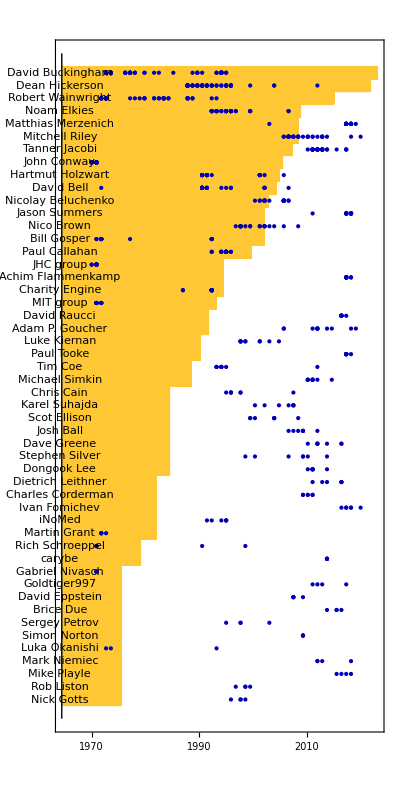

```mathematica
Show[BarChart[KeyValueMap[Labeled[#2, #1, Axis]&,Take[Sort[Counts[namesdiscoverers]],-50]],BarOrigin->Left,PlotRange->100,AspectRatio->2,PlotRangePadding->None, ScalingFunctions->"Log2"], Graphics[{ RGBColor[0, 0, 0.73], Point[{Rescale[ToExpression[#1],{1969,2025},{1.5,6}],51-#2}&@@@Select[DeleteCases[With[{w=Values[Values/@Select[, KeyExistsQ[#,"Discovered by"]&&StringQ[#[["Discovered by"]]]&][[All,{"Discovered by","Year of discovery"}]]]},
Catenate[MapIndexed[{#1,First[#2]/. _Missing->-Infinity}&,Values[ReverseSortBy[GroupBy[w,First->Last],Length]],{2}]]],{_Missing,_}],#[[2]]<=50&]]}],Axes-> True, Frame->(*False *){True, False, True, False}, FrameTicks-> {{None, None}, {Transpose[{Subdivide[1.5, 6, 5], Range[1970, 2020, 10]}], Table[{i, 2^i}, {i,2, 6}]}}]
```

#### Other

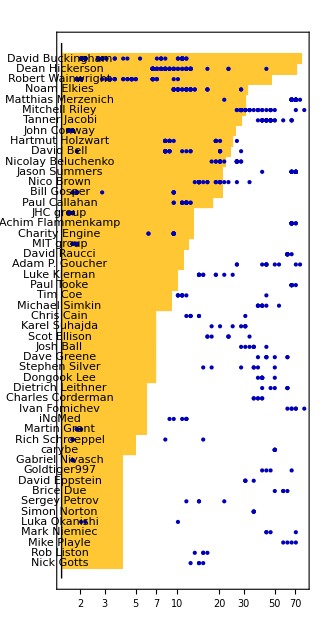

```mathematica
Show[BarChart[KeyValueMap[Labeled[#2, #1, Axis(*,Frame->True,FrameMargins->{{-5, 5}, {-5, 5}}*)]&,Take[Sort[Counts[namesdiscoverers]],-50]],BarOrigin->Left,PlotRange->100,AspectRatio->2,PlotRangePadding->None, ScalingFunctions->"Log"], Graphics[{ RGBColor[0, 0, 0.73], Point[{Rescale[ToExpression[#1],{1969,2025},{0.5,4.4}],51-#2}&@@@Select[DeleteCases[With[{w=Values[Values/@Select[, KeyExistsQ[#,"Discovered by"]&&StringQ[#[["Discovered by"]]]&][[All,{"Discovered by","Year of discovery"}]]]},
Catenate[MapIndexed[{#1,First[#2]/. _Missing->-Infinity}&,Values[ReverseSortBy[GroupBy[w,First->Last],Length]],{2}]]],{_Missing,_}],#[[2]]<=50&]]}],Axes-> True, Frame->(*False *){True, False, True, False}, FrameTicks-> {{None, None}, {Automatic(*Table[{i, Round[3.163^i]}, {i, {1.4, 2, 3.4, 4}}]*), Module[{vals =Table[i, {i, 0.5,4.47, .07}], years = Range[1969, 2025]},  Table[{vals[[i]],years[[i]]} ,{i,2, 56, 10}]]}}]
```

#### ListPlot version

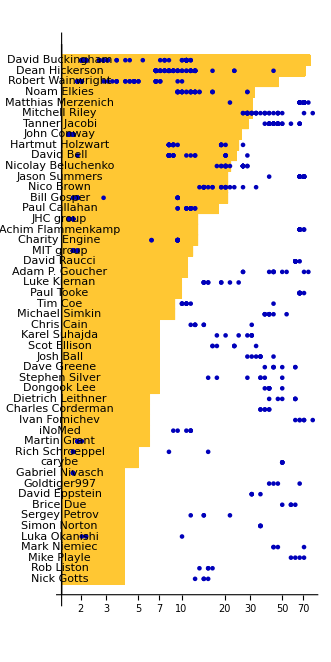

```mathematica
Show[BarChart[KeyValueMap[Labeled[#2, #1, Axis(*,Frame->True,FrameMargins->{{-5, 5}, {-5, 5}}*)]&,Take[Sort[Counts[namesdiscoverers]],-50]],BarOrigin->Left,PlotRange->100,AspectRatio->2,PlotRangePadding->None, ScalingFunctions->"Log"], ListPlot[{Rescale[ToExpression[#1],{1969,2025},{0.5,4.4}],51-#2}&@@@Select[DeleteCases[With[{w=Values[Values/@Select[, KeyExistsQ[#,"Discovered by"]&&StringQ[#[["Discovered by"]]]&][[All,{"Discovered by","Year of discovery"}]]]},
Catenate[MapIndexed[{#1,First[#2]/. _Missing->-Infinity}&,Values[ReverseSortBy[GroupBy[w,First->Last],Length]],{2}]]],{_Missing,_}],#[[2]]<=50&], PlotStyle->{RGBColor[0, 0, 0.73],PointSize[.01]}],Axes-> {True, False}, MultiaxisArrangement->All]
```

#### Columns

this isn’t terrible, but other one is better

```mathematica
(*See GoL-10-Data* for retrieval code*) 
namesdiscoverers = Select[, KeyExistsQ[#, "Discovered by"] && StringQ[#[["Discovered by"]] ]&][[All, "Discovered by"]];
```

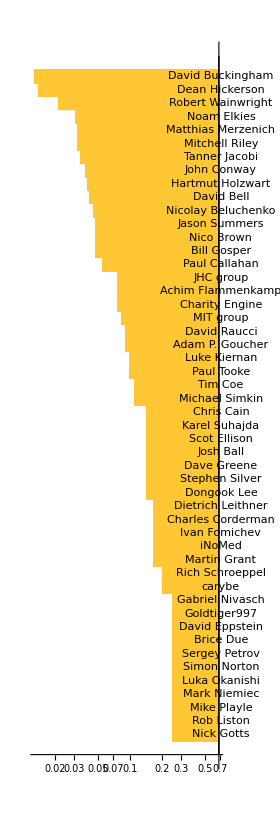
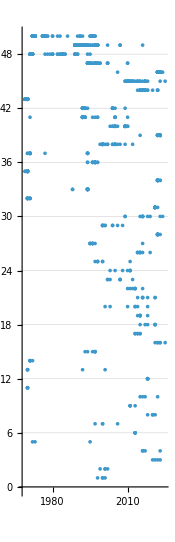

```mathematica
Row[{BarChart[Take[Sort[Counts[namesdiscoverers]],-50], BarOrigin->Right, ScalingFunctions->"Log", AspectRatio->3, ImageSize->280, PlotRangePadding->{Automatic, .8}, ChartLabels->(Style[Text[#],TextAlignment->Center]&)/@Keys[Take[Sort[Counts[namesdiscoverers]],-50]]], ListPlot[{ToExpression[#1],51-#2}&@@@Select[DeleteCases[With[{w=Values[Values/@Select[,KeyExistsQ[#,"Discovered by"]&&StringQ[#[["Discovered by"]]]&][[All,{"Discovered by","Year of discovery"}]]]},
Catenate[MapIndexed[Reverse@{First[#2], #1}&,Values[ReverseSortBy[GroupBy[w,First->Last],Length]],{2}]]],{_Missing,_}],#[[2]]<=50&],  AspectRatio->3.1, ImageSize->175,PlotRangePadding->{Automatic, {None, 1.8}}, PlotStyle-> PointSize[.015](*, Frame-> {False, False, True, False}, FrameTicks->Range[1969, 2025]*), Axes->{True, False}, GridLines->{None, Range[.5, 50.5, 1]}]}, Alignment->Top]
```

Centering text without spacing is a bit of a nightmare:

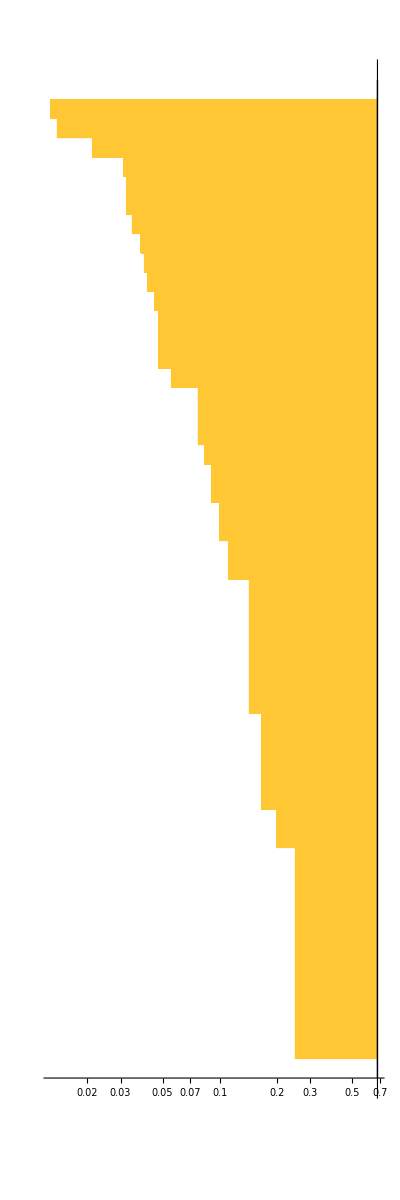
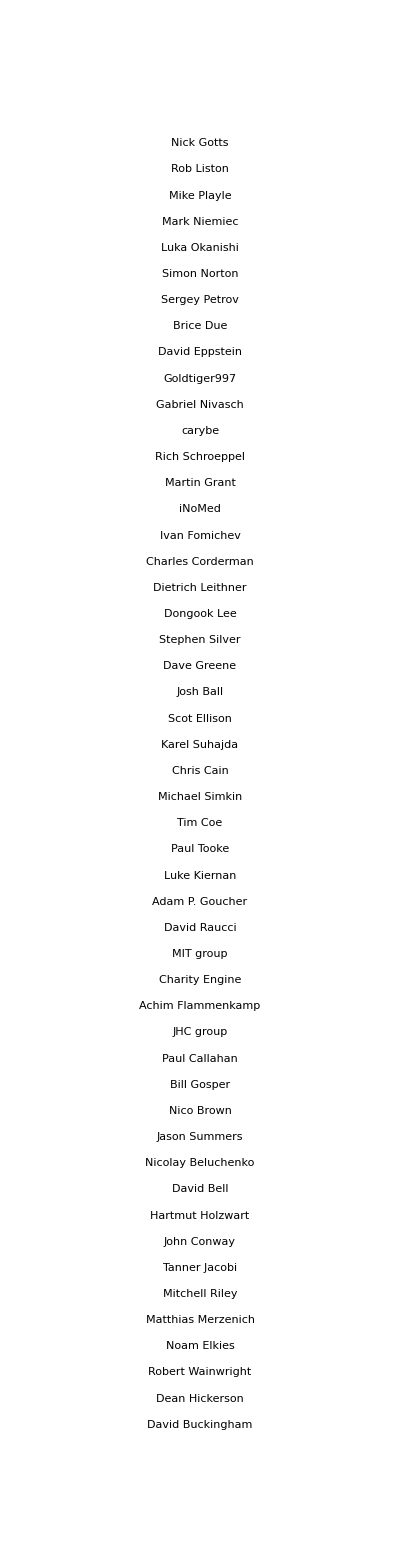
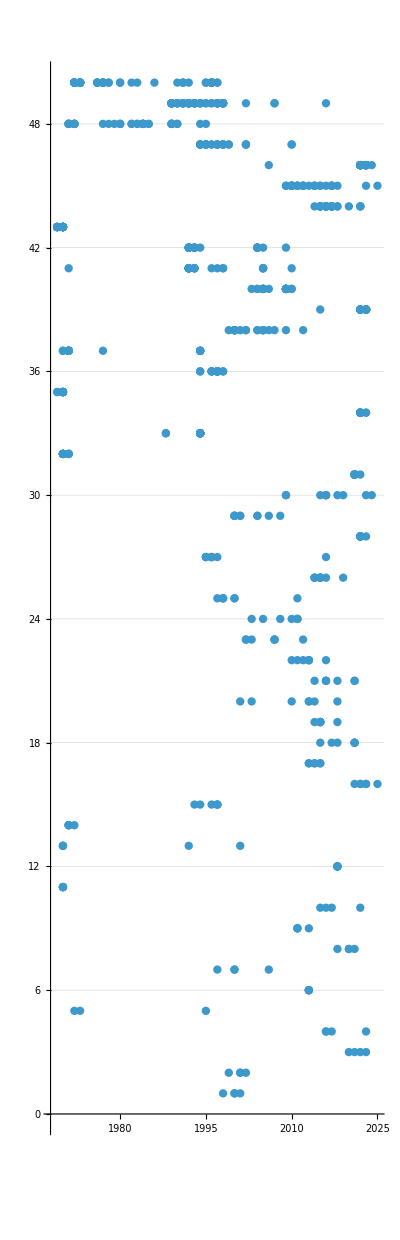

```mathematica
Row[{BarChart[Take[Sort[Counts[namesdiscoverers]],-50], BarOrigin->Right, ScalingFunctions->"Log", AspectRatio->3, ImageSize->280, PlotRangePadding->{Automatic, .8}(*, ChartLabels->(Style[Text[#],TextAlignment->Center]&)/@Keys[Take[Sort[Counts[namesdiscoverers]],-50]]*)],GraphicsColumn[Style[Text[#],Small]&/@ Keys[Take[Sort[Counts[namesdiscoverers]],-50]], ImageSize->195, AspectRatio->4, Spacings->.1], ListPlot[{ToExpression[#1],51-#2}&@@@Select[DeleteCases[With[{w=Values[Values/@Select[,KeyExistsQ[#,"Discovered by"]&&StringQ[#[["Discovered by"]]]&][[All,{"Discovered by","Year of discovery"}]]]},
Catenate[MapIndexed[Reverse@{First[#2], #1}&,Values[ReverseSortBy[GroupBy[w,First->Last],Length]],{2}]]],{_Missing,_}],#[[2]]<=50&],  AspectRatio->3.1, ImageSize->175,PlotRangePadding->{Automatic, {None, 1.8}}, PlotStyle-> PointSize[.015], Axes->{True, False}, GridLines->{None, Range[.5, 50.5, 1]}]}, Alignment->Top]
```

### Bubble chart

Also added into action items

```mathematica
osc=Select[Select[$LifeData,#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period<=100&];
```

```mathematica
aps = ParallelMap[MorphologicalComponents,SortBy[osc, #Year&][[All, "MatrixData"]]];
```

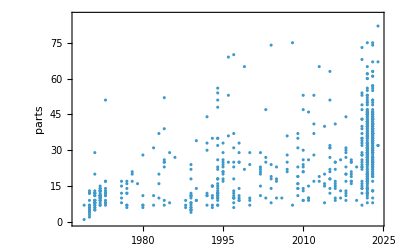

```mathematica
ListPlot[Transpose[Reverse@{Length/@ Values[aps], Values[SortBy[osc, #Year&]][[All, "Year"]]}], Frame-> True, FrameLabel->{None,"parts"}]
```

```mathematica
BubbleChart[KeyValueMap[Append[#1, #2]&,Counts[Transpose[Reverse@{(Round[#, 10]&/@(Length/@ Values[aps])), Values[SortBy[osc, #Year&]][[All, "Year"]]}]]], PlotRange->{{1969, 2025}, {-5, 100}}, ImageSize->Large, AspectRatio->.4, Frame-> True, FrameLabel->{None,"parts"}]
```

-Graphics-